## Preliminary

expanding the cosh functions comming from spin one gets

```mathematica
(e^(a*l[1])+e^(-a*l[1]))(e^(a*l[2])+e^(-a*l[2]))(e^(q*a-a*l[1]-a*l[2])+e^(-q*a+a*l[1]+a*l[2]))//Expand;
%*e^(I*b*q)//Expand
```

e^(-a q+ⅈ b q)+e^(a q+ⅈ b q)+e^(a q+ⅈ b q-2 a l[1])+e^(-a q+ⅈ b q+2 a l[1])+e^(a q+ⅈ b q-2 a l[2])+e^(a q+ⅈ b q-2 a l[1]-2 a l[2])+e^(-a q+ⅈ b q+2 a l[2])+e^(-a q+ⅈ b q+2 a l[1]+2 a l[2])

Sector 1:  , ,  :

```mathematica
{e^(a q+ⅈ b q),e^(a q+ⅈ b q-2 a l[1]),e^(a q+ⅈ b q-2 a l[2]),e^(a q+ⅈ b q-2 a l[1]-2 a l[2])};
```

Sector 2:  , ,  :

```mathematica
{e^(-a q+ⅈ b q),e^(-a q+ⅈ b q+2 a l[1]),e^(-a q+ⅈ b q+2 a l[2]),+e^(-a q+ⅈ b q+2 a l[1]+2 a l[2])};
```

the exponential factor I am working with has the following form: ). Since this integral is hard to solve using gang’s trick I will try here to expand the exponential in spin and solve order by order in spin. To do so and because I do not want to deal with exponential factors, I redefine . The first three terms are:

```mathematica
Series[Exp[a*l[1]+a*l[2]],{a,0,3}]
```

1+(l[1]+l[2]) a+1/2 (l[1]+l[2])^2 a^2+1/6 (l[1]+l[2])^3 a^3+O[a]^4

Then one notices that since the powers of dot products of l1 and l2 with a appear only in the numerator, all the terms of the expansion belong to the same sector: I(1,1,1,1,1,1,1,1,1,1,0,...) which has only one master integral.

## Fire up LiteRed

```mathematica
SetDirectory[NotebookDirectory[]]
<<LiteRed2`
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/Two_Loops

**************** LiteRed v2.024β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Mon 22 Apr 2024 14:04:05
Read from:/home/kpapad/.Mathematica/Applications/LiteRed2/LiteRed2024.m (CRC32:1463099024,{3930760867, 3144333369, 2439625558})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
ClearAll[repIBPVar]
repIBPVar={a_[i_]:> ToExpression[StringJoin[ToString[a],ToString[i]]]/;a=!=List&&a=!=c&&a=!=e&&a=!=g};
```

```mathematica
?LiteRed`*
```

## Solve the master integral

### basis for delta[bq - t]

```mathematica
SetDim[d];
Declare[{q,l1, l2,v1,v2,a,b},Vector,{y1,y2,y3,y4,y5,y6,y7,y8,t},Number]
SetConstraints[{v1,v2,a,b},sp[v1,v1]=1;sp[v2,v2]=1;sp[v1,v2]=y1;sp[a,a]=y2;sp[b,b]=-1;sp[b,a]=y4;sp[b,v1]=0;sp[b,v2]=0;
sp[a,v1]=0;
sp[a,v2]=0;
];
```

Executing
y4=0;

```mathematica
dotIBPlistCut={{
dot[b,q]-t, 
dot[v[2],l[1]],
dot[v[2],l[2]],
dot[q,v[1]],
dot[q,v[2]], 
dot[l[1],l[1]],
dot[l[2],l[2]], 
dot[q-l[1]-l[2], q-l[1]-l[2]],
dot[q,q],
dot[l[1]+l[2], l[1]+l[2]],
dot[l[1]+l[2],a],
dot[l[1],b],
dot[l[2],b], 
dot[q,a], 
dot[l[1],v[1]],
dot[l[2],v[1]],
dot[q,l[1]],
dot[a,l[1]]
}};
```

```mathematica
ds1=dotIBPlistCut[[1]]/.dot->sp/.repIBPVar
```

{-t+b·q,l1·v2,l2·v2,q·v1,q·v2,l1·l1,l2·l2,(-l1-l2+q)·(-l1-l2+q),q·q,(l1+l2)·(l1+l2),a·(l1+l2),b·l1,b·l2,a·q,l1·v1,l2·v1,l1·q,a·l1}

```mathematica
ds1//Length
```

18

#### don’t run for using

```mathematica
NewDsBasis[gb3,ds1,{l1, l2, q},SectorsPattern->{_,_,_,_,_,_,_,_,_,_,0,0,0,0,0,0,0,0},CutDs->{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0},Directory->"twoLoop",SolvejSector->True ]
```

NewDsBasis::ovrw: Warning: definitions for gb3 has been found. They may interfere with the upcoming definitions. Clearing definitions…

gb3 is valid basis. The definitions of the basis will be saved in "twoLoop" directory.
    Ds[gb3] — denominators,
    SPs[gb3] — scalar products involving loop momenta,
    LMs[gb3] — loop momenta,
    EMs[gb3] — external momenta,
    Parameters[gb3] — parameters (invariants, masses, dimension),
    Toj[gb3] — rules to transform scalar products to denominators,
    CutDs[gb3] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[gb3] — integration-by-part identities,
    LI[gb3] — Lorentz invariance identities.

Analyzing sectors…

Found 1020(4) zero(nonzero) sectors out of 1024.
    ZeroSectors[gb3] — zero sectors,
    NonZeroSectors[gb3] — nonzero sectors,
    SimpleSectors[gb3] — simple sectors (no nonzero subsectors),
    BasisSectors[gb3] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[gb3] — a rule to nullify all zero j[gb3…],
    CutDs[gb3] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 4 unique sectors.
    UniqueSectors[gb3] — unique sectors.
    MappedSectors[gb3] — mapped sectors.
    SR[gb3][…] — symmetry relations for j[gb3,…] from UniqueSectors[gb3].
    jSymmetries[gb3,…] — symmetry rules for the sector js[gb3,…] in UniqueSectors[gb3].
    jRules[gb3,…] — reduction rules for j[gb3,…] from MappedSectors[gb3].
    SectorsMappings[gb3] gives the list of mappings of all sectors from MappedSectors[gb3] to UniqueSectors[gb3].

Solving sectors…

About to solve 4 unique sectors of gb3 basis.

Sector js[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0]

Finished in 295 seconds.
    jRules[gb3, 1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[gb3] — list of master integrals appended with 1 integrals (j[gb3, 1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0]).

Sector js[gb3,1,1,1,1,1,1,1,1,0,1,0,0,0,0,0,0,0,0]

Finished in 30 seconds.
    jRules[gb3, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[gb3] — list of master integrals appended with 0 integrals.

Sector js[gb3,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0]

Finished in 63 seconds.
    jRules[gb3, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[gb3] — list of master integrals appended with 0 integrals.

Sector js[gb3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0]

Finished in 18 seconds.
    jRules[gb3, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[gb3] — list of master integrals appended with 0 integrals.

gb3

#### get the Master integrals and solve the des

```mathematica
Get["twoLoop/gb3"]
```

CheckDefinitions::warn: Some external definitions used in 'gb3' basis are missing. Probably, you should run ExecuteDefinitions[gb3].

twoLoop

I am working in the limit where y4->0

```mathematica
SetConstraints[{a,b},sp[a,b]=0];
```

```mathematica
MIs[gb3]
```

{j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0]}

```mathematica
1/((dot[b,q]-t)dot[v[2],l[1]]dot[v[2],l[2]]dot[v[1],q]dot[v[2],q]dot[l[1]+l[2],l[1]+l[2]]dot[l[1],l[1]]dot[l[2],l[2]]dot[q-l[1]-l[2], q-l[1]-l[2]]dot[q,q])/.repIBPVar/.dot->sp/.sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]]/.sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]]/.sp[-aa_,bb_]->-sp[aa,bb]/.sp[aa_,-bb_]->-sp[aa,bb]/.Toj[gb3]//FullSimplify
```

j[gb3,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0]

how many dependencies we have

```mathematica
Dinv[j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0],t]
Dinv[j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0],y1]
Dinv[j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0],y2] 
Dinv[j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0],y4]
```

j[gb3,2,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0]

-(y1 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/((-1+y1) (1+y1))+j[gb3,1,1,1,2,0,1,1,1,0,0,0,0,0,0,0,0,0,0]/((-1+y1) (1+y1))

0

0

t dependence

```mathematica
rhst=Dinv[j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0],t]//IBPReduce
```

((-11+3 d) j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/t

```mathematica
rhst=rhst/.j[___]->jj[0][t,y2]
```

((-11+3 d) jj[0][t,y2])/t

```mathematica
sol = DSolve[D[jj[0][t,y2],t]==rhst,jj[0][t,y2],t]//Flatten
```

{jj[0][t,y2]→t^(-11+3 d) C[1]}

```mathematica
solt=sol/.C[1]->f[y1]
```

{jj[0][t,y2]→t^(-11+3 d) f[y1]}

y1dependence

```mathematica
rhsy1=Dinv[j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0],y1]//IBPReduce
```

-(y1 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/((-1+y1) (1+y1))

```mathematica
rhsy1=rhsy1/.j[___]->jj[0][t,y2]/.solt
```

-(t^(-11+3 d) y1 f[y1])/((-1+y1) (1+y1))

```mathematica
soly1=DSolve[f'[y1]==-(y1 f[y1])/((-1+y1) (1+y1)),f[y1],y1]//Flatten
```

{f[y1]→C[1]/(√(1-y1^2))}

```mathematica
sol=solt/.soly1
```

{jj[0][t,y2]→(t^(-11+3 d) C[1])/(√(1-y1^2))}

```mathematica
sol=sol[[1]]/.jj[0][t,y2]->MIs[gb3][[1]]
```

j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0]→(t^(-11+3 d) C[1])/(√(1-y1^2))

```mathematica
MIs[gb3][[1]]
```

j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0]

```mathematica
t^(-11+3d)/.d->4-2eps//Expand
```

t^(1-6 eps)

## Perform the expansion

```mathematica
MIs[gb3]
```

{j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0]}

```mathematica
denom=(dot[b,q]-t)dot[v[2],l[1]]dot[v[2],l[2]]dot[v[1],q]dot[v[2],q]dot[l[1]+l[2],l[1]+l[2]]dot[l[1],l[1]]dot[l[2],l[2]]dot[q-l[1]-l[2], q-l[1]-l[2]]dot[q,q];
```

```mathematica
Series[ Exp[ x*a],{a,0,4}]//Normal
```

1+a x+(a^2 x^2)/2+(a^3 x^3)/6+(a^4 x^4)/24

```mathematica
integrand[nom_]:=nom/denom/.repIBPVar/.dot->sp/.sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]]/.sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]]/.sp[-aa_,bb_]->-sp[aa,bb]/.sp[aa_,-bb_]->-sp[aa,bb]//Expand
```

```mathematica
varx=sp[l1,a]+sp[l2,a];
```

```mathematica
terms[ord_]:=integrand[varx^ord]/Factorial[ord]/.Toj[gb3]//IBPReduce
```

```mathematica
integrand[varx^2]/Factorial[2]/.Toj[gb3]//IBPReduce;
%/.y4->0//Factor
```

((-11+3 d)^2 y2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(24 (-5+d)^2 (-2+d) t^2)

```mathematica
integrand[varx^4]/Factorial[4]/.Toj[gb3]//IBPReduce;
%/.y4->0//Factor
```

((-3+d) (-1+d) y2^2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(32 (-5+d)^2 d (-5+3 d))

```mathematica
terms[4]
```

((3 y2^2-4 d y2^2+d^2 y2^2) j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(32 (-5+d)^2 d (-5+3 d))

```mathematica
integrand[varx^6]/Factorial[6]/.Toj[gb3]//IBPReduce;
%/.y4->0//Factor
```

((-1+d) (1+d) t^2 y2^3 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(1728 (-5+d)^2 (-3+d) (2+d) (-1+3 d))

```mathematica
ord8Terms=terms[0]+terms[2]+terms[4]+terms[6]+terms[8]+terms[10]+terms[12]+terms[14];
Factor/@%
```

((-13+3 d) (-11+3 d)^2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(4 (-5+d)^2 (-4+d) t^4)+((-11+3 d)^2 y2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(24 (-5+d)^2 (-2+d) t^2)+((-3+d) (-1+d) y2^2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(32 (-5+d)^2 d (-5+3 d))+((-1+d) (1+d) t^2 y2^3 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(1728 (-5+d)^2 (-3+d) (2+d) (-1+3 d))+((-1+d) (3+d) t^4 y2^4 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(41472 (-5+d)^2 (-3+d) (4+d) (-7+3 d)^2)+((-1+d) (1+d) (3+d) (5+d) t^6 y2^5 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(138240 (-5+d)^2 (-3+d) (6+d) (-7+3 d)^2 (-5+3 d)^2 (7+3 d))+((1+d) (3+d) (5+d) (7+d) t^8 y2^6 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(14929920 (-5+d)^2 (-3+d) (-1+d) (8+d) (-7+3 d)^2 (-5+3 d)^2 (11+3 d))+((1+d) (3+d) (7+d) (9+d) t^10 y2^7 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(627056640 (-5+d)^2 (-3+d) (-1+d) (10+d) (-7+3 d)^2 (-5+3 d)^2 (-1+3 d)^2)

For general d is hard to identify a pattern to do the ressumation so I will work in dimensional regularization and keep the leading order terms

```mathematica
Series[terms[16]/.sol/.d->4-2eps,{eps,0,1}]
```

(t^13 y2^8 C[1])/(184492511723520 √(1-y1^2))-((C[1] (-41741627 t^13 y2^8+67026960 t^13 y2^8 Log[t])) eps)/(2060995367265317683200 √(1-y1^2))+O[eps]^2

```mathematica
184492511723520 //FactorInteger
```

{{2,21},{3,4},{5,1},{7,2},{11,1},{13,1},{31,1}}

```mathematica
ord8Terms/.sol;
%/.d->4-2eps;
ord8Expanded=Series[#,{eps,0,1}]&/@%
```

C[1]/(8 t^3 √(1-y1^2) eps)+((y2 C[1])/(48 t √(1-y1^2))+(3 t y2^2 C[1])/(896 √(1-y1^2))+(5 t^3 y2^3 C[1])/(38016 √(1-y1^2))+(7 t^5 y2^4 C[1])/(2764800 √(1-y1^2))+(t^7 y2^5 C[1])/(34048000 √(1-y1^2))+(11 t^9 y2^6 C[1])/(48074342400 √(1-y1^2))+(13 t^11 y2^7 C[1])/(10139505868800 √(1-y1^2))-(C[1] (5+3 Log[t]))/(4 t^3 √(1-y1^2)))+(-(y2 C[1] (5+2 Log[t]))/(16 t √(1-y1^2))-(C[1] (223 t y2^2+252 t y2^2 Log[t]))/(12544 √(1-y1^2))-(C[1] (361 t^3 y2^3+990 t^3 y2^3 Log[t]))/(1254528 √(1-y1^2))-(C[1] (127 t^5 y2^4+2520 t^5 y2^4 Log[t]))/(165888000 √(1-y1^2))-(C[1] (-6317 t^7 y2^5+35910 t^7 y2^5 Log[t]))/(203777280000 √(1-y1^2))-(C[1] (-67541 t^9 y2^6+191268 t^9 y2^6 Log[t]))/(139319444275200 √(1-y1^2))-(C[1] (-8989 t^11 y2^7+18018 t^11 y2^7 Log[t]))/(2342225855692800 √(1-y1^2))+(3 C[1] (10 Log[t]+3 Log[t]^2))/(4 t^3 √(1-y1^2))) eps+O[eps]^2

```mathematica
ord8Expanded[[3]][[2]]/.y2->x/t^2
```

(x C[1])/(48 t^3 √(1-y1^2))+(3 x^2 C[1])/(896 t^3 √(1-y1^2))+(5 x^3 C[1])/(38016 t^3 √(1-y1^2))+(7 x^4 C[1])/(2764800 t^3 √(1-y1^2))+(x^5 C[1])/(34048000 t^3 √(1-y1^2))+(11 x^6 C[1])/(48074342400 t^3 √(1-y1^2))+(13 x^7 C[1])/(10139505868800 t^3 √(1-y1^2))-(C[1] (5+3 Log[t]))/(4 t^3 √(1-y1^2))

Identify the t patern

```mathematica
FindSequenceFunction[{1/t,t,t^3,t^5,t^7,t^9,t^11}]
```

((t^2)^#1)/t^3&

Identify the pattern that the numbers in the numerator follow

```mathematica
FindSequenceFunction[{1^2,3^2,5^2,7^2,9^2,11^2,13^2}]
```

1-4 #1+4 #1^2&

Now for the numbers on the denominator, noting that they have contributions of n! from the expansion, I will factor them as Nd = n!*r, where the remainder r is easy to compute

```mathematica
Table[{denoms[[ii]]==Factorial[2*ii]*x},{ii,1,7}]//Flatten
```

{48==2 x,896==24 x,38016==720 x,2764800==40320 x,306432000==3628800 x,48074342400==479001600 x,10139505868800==87178291200 x}

```mathematica
Table[Solve[%241[[ii]],x],{ii,Length@%241}]
```

{{{x→24}},{{x→112/3}},{{x→264/5}},{{x→480/7}},{{x→760/9}},{{x→1104/11}},{{x→1512/13}}}

```mathematica
FindSequenceFunction[{24,112,264,480,760,1104,1512}]
```

8 (-#1+4 #1^2)&

do the resumation

```mathematica
summedRes=Sum[C[1]/(t^3 √(1-y1^2))*((1-4n+4 n^2)x^n)/(Factorial[2*n]*8(4 n^2-n)),{n,1,Infinity}]/.x->t^2 y2/.CoshIntegral[√(t^2 y2)]->CoshIntegral[t √y2]-Log[t √y2]+1/2 Log[t^2 y2]/.Log[√(t^2 y2)]->1/2 Log[t^2 y2]//FullSimplify
```

(C[1] (-3 CoshIntegral[t √y2]+t^2 y2 HypergeometricPFQ[{3/4},{3/2,7/4},(t^2 y2)/4]+3 (EulerGamma+Log[t √y2])))/(12 t^3 √(1-y1^2))

```mathematica
summedRes=summedRes//Expand
```

(EulerGamma C[1])/(4 t^3 √(1-y1^2))-(C[1] CoshIntegral[t √y2])/(4 t^3 √(1-y1^2))+(y2 C[1] HypergeometricPFQ[{3/4},{3/2,7/4},(t^2 y2)/4])/(12 t √(1-y1^2))+(C[1] Log[t √y2])/(4 t^3 √(1-y1^2))

## Do the t integration

Basically I have to integrate  summedRes. One notices that this integration corresponds to the furier transform of summedRes, whith the FT parameter evaluated at 1.

### Do the integrals that can be done this way

```mathematica
ft1 = FourierTransform[summedRes[[1]],t,s]/.s->1
```

-(ⅈ EulerGamma √(π/2) C[1])/(8 √(1-y1^2))

```mathematica
ft3=FourierTransform[summedRes[[3]],t,s]/.s->1
```

-(ⅈ √(π/2) y2 C[1] (-1-(-3 √(-1/y2)+2 (-1/y2)^(3/4)) (-1+UnitStep[1-Abs[y2]])+UnitStep[-1+Abs[y2]]))/(12 √(1-y1^2))

```mathematica
ft4=FourierTransform[summedRes[[4]],t,s]/.s->1
```

-(ⅈ √(π/2) C[1] Log[y2])/(16 √(1-y1^2))

```mathematica
FourierTransform[Exp[-s*t]CoshIntegral[t √y2],t,u]
```

$Aborted

### Do the hard integral

The evaluation of , is challenging. To proceed further we use the property  for real u and the integral can be written as:

#### Do the integral

```mathematica
int2=Integrate[Exp[-I*u*β]/u^3,u]
```

(ⅈ ⅇ^(-ⅈ u β) (ⅈ+u β))/(2 u^2)-1/2 β^2 ExpIntegralEi[-ⅈ u β]

```mathematica
upper=Limit[int2,u->+∞]
```

1/4 ⅈ π β^2 (1+(-1)^Floor[1/2-Arg[β]/π]+2 Floor[(π+2 Arg[β])/(4 π)]+2 Floor[1/2-Arg[β]/π]-2 Floor[3/4-Arg[β]/(2 π)])

```mathematica
upper=Assuming[{Element[β,Reals],β>0},Refine[upper]]
```

1/2 ⅈ π β^2

```mathematica
lower = int2/.u->λ
```

(ⅈ ⅇ^(-ⅈ β λ) (ⅈ+β λ))/(2 λ^2)-1/2 β^2 ExpIntegralEi[-ⅈ β λ]

the value at 0 is divergent so for now i use λ as a regulator

#### Do the integral

to do this integral I am integrating by parts twice

The first integration is

```mathematica
firstIBP1=Integrate[CoshIntegral[u]/u^3,u]*Sin[β*u] //Expand
```

-(Cosh[u] Sin[u β])/(4 u^2)+1/4 CoshIntegral[u] Sin[u β]-(CoshIntegral[u] Sin[u β])/(2 u^2)-(Sin[u β] Sinh[u])/(4 u)

```mathematica
Limit[firstIBP1,u->+∞]
```

ConditionalExpression[Indeterminate, β∈ℝ]

```mathematica
firstIBP2Integrand = Integrate[CoshIntegral[u]/u^3,u]*D[Sin[β*u],u]//Expand
```

-(β Cos[u β] Cosh[u])/(4 u^2)+1/4 β Cos[u β] CoshIntegral[u]-(β Cos[u β] CoshIntegral[u])/(2 u^2)-(β Cos[u β] Sinh[u])/(4 u)

```mathematica
firstIBP2Integrable = Integrate[firstIBP2Integrand[[{1,2,4}]],u]
```

-1/16 β (-(ⅇ^(u (-1-ⅈ β)) (1+ⅇ^(2 u)))/u+(-1-ⅈ β) ExpIntegralEi[u (-1-ⅈ β)]+(1-ⅈ β) ExpIntegralEi[u-ⅈ u β])-1/16 β (-ExpIntegralEi[-u-ⅈ u β]+ExpIntegralEi[u-ⅈ u β]-ExpIntegralEi[-u+ⅈ u β]+ExpIntegralEi[u+ⅈ u β])+1/16 ⅈ (-ExpIntegralEi[-u-ⅈ u β]-ExpIntegralEi[u-ⅈ u β]+ExpIntegralEi[-u+ⅈ u β]+ExpIntegralEi[u+ⅈ u β])-(β (-ⅇ^(ⅈ u (ⅈ+β)) (1+ⅇ^(2 u))+ⅈ u (ⅈ+β) ExpIntegralEi[ⅈ u (ⅈ+β)]+(u+ⅈ u β) ExpIntegralEi[u+ⅈ u β]))/(16 u)+1/4 CoshIntegral[u] Sin[u β]

now we have to integrate -(β Cos[u β] CoshIntegral[u])/(2 u^2). So we do again integration by parts

```mathematica
thridIBP1 = Integrate[CoshIntegral[u]/(2 u^2),u]Cos[u*β]//Expand
```

-(Cos[u β] Cosh[u])/(2 u)-(Cos[u β] CoshIntegral[u])/(2 u)+1/2 Cos[u β] SinhIntegral[u]

```mathematica
Limit[thridIBP1,u->+Infinity]
Limit[thridIBP1,u->0]
```

ConditionalExpression[Indeterminate, β∈ℝ]

Indeterminate

```mathematica
thirdIBP2Integrand=Integrate[CoshIntegral[u]/(2 u^2),u]*D[Cos[u*β],u]//Expand
```

(β Cosh[u] Sin[u β])/(2 u)+(β CoshIntegral[u] Sin[u β])/(2 u)-1/2 β Sin[u β] SinhIntegral[u]

```mathematica
thirdIBP2Integrable=Integrate[thirdIBP2Integrand[[{1,3}]],u]
```

1/8 (ExpIntegralEi[-u-ⅈ u β]-ExpIntegralEi[u-ⅈ u β]+ExpIntegralEi[-u+ⅈ u β]-ExpIntegralEi[u+ⅈ u β])-1/8 ⅈ β (-ExpIntegralEi[-u-ⅈ u β]-ExpIntegralEi[u-ⅈ u β]+ExpIntegralEi[-u+ⅈ u β]+ExpIntegralEi[u+ⅈ u β])+1/2 Cos[u β] SinhIntegral[u]

```mathematica
Integrate[CoshIntegral[u]/(2 u),u]D[Sin[u*β],u]//Expand
```

-1/4 u β Cos[u β] HypergeometricPFQ[{1,1,1},{2,2,2},-u]+1/4 u β Cos[u β] HypergeometricPFQ[{1,1,1},{2,2,2},u]+1/2 EulerGamma β Cos[u β] Log[u]+1/4 β Cos[u β] Log[u]^2

```mathematica
Plot[Re[NIntegrate[Exp[I*t] CoshIntegral[t]/t^3,{t,-x,x}]],{x,30,100}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {-3.13078×10^-56}. NIntegrate obtained 4.2925×10^176-6.80191×10^174 ⅈ and 4.29304×10^176 for the integral and error estimates.

$Aborted

```mathematica
HypergeometricPFQ[{1,1,1},{2,2,2},-u]+HypergeometricPFQ[{1,1,1},{2,2,2},u]
```

HypergeometricPFQ[{1,1,1},{2,2,2},-u]+HypergeometricPFQ[{1,1,1},{2,2,2},u]

```mathematica
Table[Pochhammer[1,ii],{ii,1,10}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
Integrate[ u*HypergeometricPFQ[{1,1,1},{2,2,2},-u],u]
```

-1+ⅇ^-u+u-EulerGamma u+u ExpIntegralEi[-u]+u^2 HypergeometricPFQ[{1,1,1},{2,2,2},-u]+1/2 u Log[-1/u]-1/2 u Log[-u]

```mathematica
Integrate[Exp[-u*s] CoshIntegral[u] Sin[u β],u]
```

-1/(4 (s^2+β^2))ⅈ (-((s-ⅈ β) (ExpIntegralEi[-u (-1+s+ⅈ β)]+ExpIntegralEi[-u (1+s+ⅈ β)]))+(s+ⅈ β) (ExpIntegralEi[-u (1+s-ⅈ β)]+ExpIntegralEi[u-s u+ⅈ u β])-4 ⅈ ⅇ^(-s u) CoshIntegral[u] (β Cos[u β]+s Sin[u β]))

```mathematica
%49//Expand
```

-(ⅇ^(-s u) β Cos[u β] CoshIntegral[u])/(s^2+β^2)-(ⅈ s ExpIntegralEi[-u (1+s-ⅈ β)])/(4 (s^2+β^2))+(β ExpIntegralEi[-u (1+s-ⅈ β)])/(4 (s^2+β^2))+(ⅈ s ExpIntegralEi[-u (-1+s+ⅈ β)])/(4 (s^2+β^2))+(β ExpIntegralEi[-u (-1+s+ⅈ β)])/(4 (s^2+β^2))+(ⅈ s ExpIntegralEi[-u (1+s+ⅈ β)])/(4 (s^2+β^2))+(β ExpIntegralEi[-u (1+s+ⅈ β)])/(4 (s^2+β^2))-(ⅈ s ExpIntegralEi[u-s u+ⅈ u β])/(4 (s^2+β^2))+(β ExpIntegralEi[u-s u+ⅈ u β])/(4 (s^2+β^2))-(ⅇ^(-s u) s CoshIntegral[u] Sin[u β])/(s^2+β^2)

```mathematica
Limit[%51[[1]],u->+Infinity]
```

lim_(u→∞) -(ⅇ^(-s u) β Cos[u β] CoshIntegral[u])/(s^2+β^2)

```mathematica
Limit[%49,u->+Infinity]
```

$Aborted

```mathematica
Assuming[{Element[s,Reals],√y2>0,s>0},Limit[ExpIntegralEi[t (ⅈ-s+√y2)],t->+Infinity]]
```

ExpIntegralEi[(ⅈ-s+√y2) ∞]

### tangential

```mathematica
denom3=(dot[b,q]-t)dot[v[2],l[1]]dot[v[2],l[2]]dot[v[1],q]dot[v[2],q](dot[l[1],l[1]])^2 dot[l[2],l[2]]dot[q-l[1]-l[2], q-l[1]-l[2]]dot[q,q];
```

```mathematica
integrand3[nom_]:=nom/denom3/.repIBPVar/.dot->sp/.sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]]/.sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]]/.sp[-aa_,bb_]->-sp[aa,bb]/.sp[aa_,-bb_]->-sp[aa,bb]//Expand
```

```mathematica
terms3[ord_]:=integrand3[varx^ord]/Factorial[ord]/.Toj[gb3]//Simplify//IBPReduce//Factor
```

```mathematica
terms3[0]+terms3[2]+terms3[4]+terms3[6];
%/.y4->0;
Factor/@%
```

-((-13+3 d) (-11+3 d)^2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(4 (-5+d)^2 t^4)-((-13+3 d) (-11+3 d) y2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(12 (-5+d)^2 t^2)-((-172+209 d-78 d^2+9 d^3) y2^2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(24 (-5+d)^2 (-7+3 d) (-5+3 d))-((60-259 d+239 d^2-81 d^3+9 d^4) t^2 y2^3 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(216 (-5+d)^2 (-3+d) (-7+3 d) (-5+3 d) (-1+3 d))

```mathematica
((-13+3 d) (-11+3 d)^2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(4 (-5+d)^2 (-4+d) t^4)+((-13+3 d) (-11+3 d) y2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(12 (-5+d)^2 (-4+d) t^2)+((-172+209 d-78 d^2+9 d^3) y2^2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(24 (-5+d)^2 (-4+d) (-7+3 d) (-5+3 d))+((60-259 d+239 d^2-81 d^3+9 d^4) t^2 y2^3 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(216 (-5+d)^2 (-4+d) (-3+d) (-7+3 d) (-5+3 d) (-1+3 d))
```

## Look at another branch

```mathematica
varx2=sp[l2,a];
```

```mathematica
Clear[terms]
```

```mathematica
terms2[ord_]:=integrand[varx2^ord]/Factorial[ord]/.Toj[gb3]//IBPReduce
```

```mathematica
terms2[4]
```

0

```mathematica
ord8Terms2=terms2[0]+terms2[2]+terms2[4]+terms2[6]+terms2[8]+terms2[10]+terms2[12]+terms2[14];
Factor/@%
```

((-13+3 d) (-11+3 d)^2 j[gb3,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0])/(4 (-5+d)^2 (-4+d) t^4)

```mathematica
ord8Terms2/.sol;
%/.d->4-2eps;
ord8Expanded2=Series[#,{eps,0,1}]&/@%
```

C[1]/(8 t^3 √(1-y1^2) eps)+((y2 C[1])/(48 t √(1-y1^2))+(3 t y2^2 C[1])/(896 √(1-y1^2))+(5 t^3 y2^3 C[1])/(38016 √(1-y1^2))+(7 t^5 y2^4 C[1])/(2764800 √(1-y1^2))+(t^7 y2^5 C[1])/(34048000 √(1-y1^2))+(11 t^9 y2^6 C[1])/(48074342400 √(1-y1^2))+(13 t^11 y2^7 C[1])/(10139505868800 √(1-y1^2))-(C[1] (5+3 Log[t]))/(4 t^3 √(1-y1^2)))+(-(y2 C[1] (5+2 Log[t]))/(16 t √(1-y1^2))-(C[1] (223 t y2^2+252 t y2^2 Log[t]))/(12544 √(1-y1^2))-(C[1] (361 t^3 y2^3+990 t^3 y2^3 Log[t]))/(1254528 √(1-y1^2))-(C[1] (127 t^5 y2^4+2520 t^5 y2^4 Log[t]))/(165888000 √(1-y1^2))-(C[1] (-6317 t^7 y2^5+35910 t^7 y2^5 Log[t]))/(203777280000 √(1-y1^2))-(C[1] (-67541 t^9 y2^6+191268 t^9 y2^6 Log[t]))/(139319444275200 √(1-y1^2))-(C[1] (-8989 t^11 y2^7+18018 t^11 y2^7 Log[t]))/(2342225855692800 √(1-y1^2))+(3 C[1] (10 Log[t]+3 Log[t]^2))/(4 t^3 √(1-y1^2))) eps+O[eps]^2

```mathematica
ord8Expanded
```

C[1]/(8 t^3 √(1-y1^2) eps)+((y2 C[1])/(48 t √(1-y1^2))+(3 t y2^2 C[1])/(896 √(1-y1^2))+(5 t^3 y2^3 C[1])/(38016 √(1-y1^2))+(7 t^5 y2^4 C[1])/(2764800 √(1-y1^2))+(t^7 y2^5 C[1])/(34048000 √(1-y1^2))+(11 t^9 y2^6 C[1])/(48074342400 √(1-y1^2))+(13 t^11 y2^7 C[1])/(10139505868800 √(1-y1^2))-(C[1] (5+3 Log[t]))/(4 t^3 √(1-y1^2)))+(-(y2 C[1] (5+2 Log[t]))/(16 t √(1-y1^2))-(C[1] (223 t y2^2+252 t y2^2 Log[t]))/(12544 √(1-y1^2))-(C[1] (361 t^3 y2^3+990 t^3 y2^3 Log[t]))/(1254528 √(1-y1^2))-(C[1] (127 t^5 y2^4+2520 t^5 y2^4 Log[t]))/(165888000 √(1-y1^2))-(C[1] (-6317 t^7 y2^5+35910 t^7 y2^5 Log[t]))/(203777280000 √(1-y1^2))-(C[1] (-67541 t^9 y2^6+191268 t^9 y2^6 Log[t]))/(139319444275200 √(1-y1^2))-(C[1] (-8989 t^11 y2^7+18018 t^11 y2^7 Log[t]))/(2342225855692800 √(1-y1^2))+(3 C[1] (10 Log[t]+3 Log[t]^2))/(4 t^3 √(1-y1^2))) eps+O[eps]^2

## Try doing the l1l2 integration first

### find the basis

```mathematica
SetDim[d];
Declare[{q,l1, l2,v1,v2,a,b},Vector,{y1,y2,y3,y4,y5,y6,y7,y8,yb,t},Number]
SetConstraints[{v1,v2,a,b,q},sp[v1,v1]=1;sp[v2,v2]=1;sp[v1,v2]=y1;sp[a,a]=y2;sp[b,b]=yb;
sp[b,a]=0;sp[b,v1]=0;sp[b,v2]=0;
sp[a,v1]=0;
sp[a,v2]=0;
sp[q,v1]=0;
sp[q,v2]=0;
sp[q,q]=y4;
sp[a,q]=y5;
sp[b,q]=y6;
];
```

Executing
a·a=y2;a·b=0;a·q=y5;a·v1=0;a·v2=0;b·b=yb;b·q=y6;b·v1=0;b·v2=0;q·q=y4;q·v1=0;q·v2=0;v1·v1=1;v1·v2=y1;v2·v2=1;

```mathematica
dotIBPlistCut={{
dot[v[2],l[1]],
dot[v[2],l[2]], 
dot[l[1],l[1]],
dot[l[2],l[2]], 
dot[q-l[1]-l[2], q-l[1]-l[2]],
dot[l[1]+l[2], l[1]+l[2]],
dot[l[1]+l[2],a],
dot[l[1],b],
dot[l[2],b], 
dot[l[1],v[1]],
dot[l[2],v[1]],
dot[q,l[1]],
dot[a,l[1]]
}};
```

```mathematica
ds1=dotIBPlistCut[[1]]/.dot->sp/.repIBPVar
```

{l1·v2,l2·v2,l1·l1,l2·l2,(-l1-l2+q)·(-l1-l2+q),(l1+l2)·(l1+l2),a·(l1+l2),b·l1,b·l2,l1·v1,l2·v1,l1·q,a·l1}

```mathematica
ds1//Length
```

13

```mathematica
Quit[]
```

### dont run for using

```mathematica
NewDsBasis[gb3aling,ds1,{l1, l2},SectorsPattern->{_,_,_,_,_,_,0,0,0,0,0,0,0},CutDs->{1,1,1,1,1,0,0,0,0,0,0,0,0},Directory->"twoLoop",SolvejSector->True ]
```

gb3aling is valid basis. The definitions of the basis will be saved in "twoLoop" directory.
    Ds[gb3aling] — denominators,
    SPs[gb3aling] — scalar products involving loop momenta,
    LMs[gb3aling] — loop momenta,
    EMs[gb3aling] — external momenta,
    Parameters[gb3aling] — parameters (invariants, masses, dimension),
    Toj[gb3aling] — rules to transform scalar products to denominators,
    CutDs[gb3aling] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[gb3aling] — integration-by-part identities,
    LI[gb3aling] — Lorentz invariance identities.

Analyzing sectors…

Found 62(2) zero(nonzero) sectors out of 64.
    ZeroSectors[gb3aling] — zero sectors,
    NonZeroSectors[gb3aling] — nonzero sectors,
    SimpleSectors[gb3aling] — simple sectors (no nonzero subsectors),
    BasisSectors[gb3aling] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[gb3aling] — a rule to nullify all zero j[gb3aling…],
    CutDs[gb3aling] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 2 unique sectors.
    UniqueSectors[gb3aling] — unique sectors.
    MappedSectors[gb3aling] — mapped sectors.
    SR[gb3aling][…] — symmetry relations for j[gb3aling,…] from UniqueSectors[gb3aling].
    jSymmetries[gb3aling,…] — symmetry rules for the sector js[gb3aling,…] in UniqueSectors[gb3aling].
    jRules[gb3aling,…] — reduction rules for j[gb3aling,…] from MappedSectors[gb3aling].
    SectorsMappings[gb3aling] gives the list of mappings of all sectors from MappedSectors[gb3aling] to UniqueSectors[gb3aling].

Solving sectors…

About to solve 2 unique sectors of gb3aling basis.

Sector js[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0]

Finished in 22 seconds.
    jRules[gb3aling, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[gb3aling] — list of master integrals appended with 1 integrals (j[gb3aling, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0]).

Sector js[gb3aling,1,1,1,1,1,1,0,0,0,0,0,0,0]

Finished in 2 seconds.
    jRules[gb3aling, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[gb3aling] — list of master integrals appended with 0 integrals.

gb3aling

```mathematica
MIs[gb3aling]
```

{j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0]}

### Solve the master integral

again I am working out the case where y3=0

```mathematica
Get["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/Two_Loops/twoLoop/gb3aling"]
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/Two_Loops/twoLoop

how many dependencies

```mathematica
MIs[gb3aling]
```

{j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0]}

```mathematica
Dinv[j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0],y1]
Dinv[j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0],y2]
Dinv[j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0],yb]
Dinv[j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0],y4]
Dinv[j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0],y5]
```

0

0

0

-(y2 yb j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))+(y2 yb j[gb3aling,1,1,1,1,2,-1,0,0,0,0,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))+(y5 yb j[gb3aling,1,1,1,1,2,0,-1,0,0,0,0,0,0])/(y2 y6^2-y2 y4 yb+y5^2 yb)+(y2 y6 j[gb3aling,1,1,1,1,2,0,0,-1,0,0,0,0,0])/(y2 y6^2-y2 y4 yb+y5^2 yb)+(y2 y6 j[gb3aling,1,1,1,1,2,0,0,0,-1,0,0,0,0])/(y2 y6^2-y2 y4 yb+y5^2 yb)-j[gb3aling,1,1,1,1,2,0,0,0,0,0,0,0,0]+(y2 y4 yb j[gb3aling,1,1,1,1,2,0,0,0,0,0,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))

0

```mathematica
rhsy4=Dinv[MIs[gb3aling][[1]],y4]//IBPReduce
```

((-4+d) j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0])/y4

```mathematica
rhsy4=rhsy4/.j[___]->jj[y4]
```

((-4+d) jj[y4])/y4

```mathematica
sol=DSolve[{D[jj[y4],y4]==rhsy4},jj[y4],y4]/.d->4-2eps
```

{{jj[y4]→y4^(-2 eps) C[1]}}

In the bibliography this integral evaluates to   (in the limit whre b->1).  I will mach the integration constant c1 to this value. There is goint to be a b dependency as well but since we will send b to 1 in the end it shouldn’t matter.

```mathematica
const=Solve[y4^(-2 eps) C[1]==(4 π^2)/eps(-y4)^(-2eps)2^(2eps),C[1]]//Flatten
```

{C[1]→(2^(2+2 eps) π^2 (-y4)^(-2 eps) y4^(2 eps))/eps}

```mathematica
const//PowerExpand
```

{C[1]→((-1)^(-2 eps) 2^(2+2 eps) π^2)/eps}

```mathematica
sol=sol/.const
```

{{jj[y4]→(2^(2+2 eps) π^2 (-y4)^(-2 eps))/eps}}

```mathematica
sol=sol/.jj[y4]->MIs[gb3aling][[1]]//Flatten
```

{j[gb3aling,1,1,1,1,1,0,0,0,0,0,0,0,0]→(2^(2+2 eps) π^2 (-y4)^(-2 eps))/eps}

### perform the expansion

y1=v1v2,  y2=a^2, y3=0, y4=q^2, y5=aq, y6=bq

```mathematica
denom=dot[v[2],l[1]]dot[v[2],l[2]]dot[l[1]+l[2],l[1]+l[2]]dot[l[1],l[1]]dot[l[2],l[2]]dot[q-l[1]-l[2], q-l[1]-l[2]];
```

```mathematica
integrand[nom_]:=nom/denom/.repIBPVar/.dot->sp/.sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]]/.sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]]/.sp[-aa_,bb_]->-sp[aa,bb]/.sp[aa_,-bb_]->-sp[aa,bb]//Expand
```

```mathematica
varx=sp[l1,a]+sp[l2,a];
```

```mathematica
integrand[varx]/.Toj[gb3aling]//Simplify
```

j[gb3aling,1,1,1,1,1,1,-1,0,0,0,0,0,0]

```mathematica
ClearAll[terms]
terms[ord_]:=integrand[varx^ord]/Factorial[ord]/.Toj[gb3aling]//Simplify//IBPReduce
```

```mathematica
ordTerms=Sum[terms[ii],{ii,0,18}];
Collect[#,{y2,y4,y5}]&/@%;
ordTerms=Factor/@%;
```

```mathematica
ordTerms=ordTerms/.d->4-2eps/.sol//PowerExpand;
SameQ[CoefficientList[ordTerms,y5][[2]],Coefficient[Collect[ordTerms,y5],y5,1]]
```

True

I will need feyncalc in order to define the derivative a.partial b and act with it on the integrated qs

```mathematica
<<FeynCalc`
```

Factor1::shdw: Symbol Factor1 appears in multiple contexts {FeynCalc`,LiteRed`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

Factor2::shdw: Symbol Factor2 appears in multiple contexts {FeynCalc`,LiteRed`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

Factor3::shdw: Symbol Factor3 appears in multiple contexts {FeynCalc`,LiteRed`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

MetricTensor::shdw: Symbol MetricTensor appears in multiple contexts {FeynCalc`,Vectors`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

```mathematica
ClearAll[diffopp]
diffopp[f_]:=Contract[FV[a,μ] FourDivergence[f,FV[b,μ]]]
diffopp[f_,0]:=f
diffopp[f_,1]:=I*diffopp[f]
diffopp[f_,n_]:=diffopp[f,n]=I*diffopp[diffopp[f,n-1]]
```

```mathematica
b2=FV[b,μ]FV[b,μ]//Contract
```

Pair[Momentum[b],Momentum[b]]

```mathematica
diffopp[f[b2],2]
```

ⅈ (2 ⅈ Pair[Momentum[a],Momentum[a]] f'[Pair[Momentum[b],Momentum[b]]]+4 ⅈ Pair[Momentum[a],Momentum[b]]^2 f''[Pair[Momentum[b],Momentum[b]]])

```mathematica
ClearAll[qIntegral]
qIntegral[pw_]:=((2Pi)^(d-2)4^pw Pi^((2-d)/2))/(√(y1^2-1)(b2)^((d-2+2pw)/2))*Gamma[(d-2)/2+pw]/Gamma[-pw]/.d->4-2eps
```

```mathematica
Coefficient[ordTerms,y5,0]
```

((-1)^(-2 eps) 2^(2+2 eps) (-11+3 (4-2 eps)) π^2 y4^(-1-2 eps))/((-1-2 eps) eps)+((-1)^(-2 eps) 2^(-1+2 eps) (3-2 eps) π^2 y2^2 y4^(1-2 eps))/(3 (-7+3 (4-2 eps)) (-5+3 (4-2 eps)) (-1-2 eps) eps)-((-1)^(-2 eps) 2^(-2+2 eps) (5-2 eps) π^2 y2^3 y4^(2-2 eps))/(27 (-7+3 (4-2 eps)) (-5+3 (4-2 eps)) (-1+3 (4-2 eps)) (-1-2 eps) eps)+((-1)^(-2 eps) 2^(-5+2 eps) (7-2 eps) π^2 y2^4 y4^(3-2 eps))/(81 (-7+3 (4-2 eps)) (-5+3 (4-2 eps)) (-1+3 (4-2 eps)) (1+3 (4-2 eps)) (-1-2 eps) eps)-((-1)^(-2 eps) 2^(-6+2 eps) (7-2 eps) (9-2 eps) π^2 y2^5 y4^(4-2 eps))/(405 (-7+3 (4-2 eps)) (-5+3 (4-2 eps)) (-1+3 (4-2 eps)) (1+3 (4-2 eps)) (5+3 (4-2 eps)) (7+3 (4-2 eps)) (-1-2 eps) eps)+((-1)^(-2 eps) 2^(-8+2 eps) (9-2 eps) (11-2 eps) π^2 y2^6 y4^(5-2 eps))/(3645 (-7+3 (4-2 eps)) (-5+3 (4-2 eps)) (-1+3 (4-2 eps)) (1+3 (4-2 eps)) (5+3 (4-2 eps)) (7+3 (4-2 eps)) (11+3 (4-2 eps)) (-1-2 eps) eps)-((-1)^(-2 eps) 2^(-9+2 eps) (11-2 eps) (13-2 eps) π^2 y2^7 y4^(6-2 eps))/(76545 (-7+3 (4-2 eps)) (-5+3 (4-2 eps)) (-1+3 (4-2 eps)) (1+3 (4-2 eps)) (5+3 (4-2 eps)) (7+3 (4-2 eps)) (11+3 (4-2 eps)) (13+3 (4-2 eps)) (-1-2 eps) eps)+((-1)^(-2 eps) 2^(-13+2 eps) (11-2 eps) (13-2 eps) (15-2 eps) π^2 y2^8 y4^(7-2 eps))/(76545 (-7+3 (4-2 eps)) (-5+3 (4-2 eps)) (-1+3 (4-2 eps)) (1+3 (4-2 eps)) (5+3 (4-2 eps)) (7+3 (4-2 eps)) (11+3 (4-2 eps)) (13+3 (4-2 eps)) (17+3 (4-2 eps)) (19+3 (4-2 eps)) (-1-2 eps) eps)-((-1)^(-2 eps) 2^(-14+2 eps) (13-2 eps) (15-2 eps) (17-2 eps) π^2 y2^9 y4^(8-2 eps))/(2066715 (-7+3 (4-2 eps)) (-5+3 (4-2 eps)) (-1+3 (4-2 eps)) (1+3 (4-2 eps)) (5+3 (4-2 eps)) (7+3 (4-2 eps)) (11+3 (4-2 eps)) (13+3 (4-2 eps)) (17+3 (4-2 eps)) (19+3 (4-2 eps)) (23+3 (4-2 eps)) (-1-2 eps) eps)-((-1)^(-2 eps) 2^(1+2 eps) π^2 y2 y4^(-2 eps))/(3 (-1-2 eps) eps)

since the computation is rather complex i am going to first pre calculate qIntegral and use a look up table.

```mathematica
powers=Cases[ordTerms,Power[y4,pw_]->pw,Infinity]//DeleteDuplicates
```

{-1-2 eps,1-2 eps,2-2 eps,3-2 eps,4-2 eps,5-2 eps,6-2 eps,7-2 eps,8-2 eps,-2 eps}

```mathematica
qIntegralTable=Association[#->qIntegral[#]&/@powers];
```

```mathematica
qIntegrated=Table[With[{coeff=Coefficient[ordTerms,y5,ii-1]},coeff/. Power[y4,pw_]:>diffopp[qIntegralTable[pw],ii-1]]/. Pair[Momentum[xx_],Momentum[yy_]]->sp[xx,yy],{ii,Length@CoefficientList[ordTerms,y5]}]//Total
```

```mathematica
FreeQ[qIntegrated,y4]
```

True

```mathematica
qIntegratedExpanded=Series[qIntegrated,{eps,0,2}]
```

```mathematica
order0eps=Collect[Coefficient[qIntegratedExpanded,eps,0],y2]
```

(524288 π^3 y2^9)/(984555 √(-1+y1^2) yb^9)+(4096 π^3 y2^8)/(6435 √(-1+y1^2) yb^8)+(16384 π^3 y2^7)/(21021 √(-1+y1^2) yb^7)+(2048 π^3 y2^6)/(2079 √(-1+y1^2) yb^6)+(2048 π^3 y2^5)/(1575 √(-1+y1^2) yb^5)+(64 π^3 y2^4)/(35 √(-1+y1^2) yb^4)+(128 π^3 y2^3)/(45 √(-1+y1^2) yb^3)+(16 π^3 y2^2)/(3 √(-1+y1^2) yb^2)+(16 π^3 y2)/(√(-1+y1^2) yb)+1/(241215975 √(-1+y1^2) yb^9)(5145940800 π^3 yb^9-12864852000 EulerGamma π^3 yb^9+4020266250 EulerGamma^2 π^3 yb^9+5145940800 ⅈ π^4 yb^9-3216213000 ⅈ EulerGamma π^4 yb^9-509233725 π^5 yb^9+10291881600 π^3 yb^9 Log[2]-6432426000 EulerGamma π^3 yb^9 Log[2]+2572970400 ⅈ π^4 yb^9 Log[2]+2572970400 π^3 yb^9 Log[2]^2+2572970400 π^3 yb^9 Log[π]-1608106500 EulerGamma π^3 yb^9 Log[π]+643242600 ⅈ π^4 yb^9 Log[π]+1286485200 π^3 yb^9 Log[2] Log[π]+160810650 π^3 yb^9 Log[π]^2-7718911200 π^3 yb^9 Log[yb]+4824319500 EulerGamma π^3 yb^9 Log[yb]-1929727800 ⅈ π^4 yb^9 Log[yb]-3859455600 π^3 yb^9 Log[2] Log[yb]-964863900 π^3 yb^9 Log[π] Log[yb]+1447295850 π^3 yb^9 Log[yb]^2)

```mathematica
y2ser=order0eps[[1;;9]];
y2ser=Table[y2ser[[9-i]],{i,0,8}]
```

{(16 π^3 y2)/(√(-1+y1^2) yb),(16 π^3 y2^2)/(3 √(-1+y1^2) yb^2),(128 π^3 y2^3)/(45 √(-1+y1^2) yb^3),(64 π^3 y2^4)/(35 √(-1+y1^2) yb^4),(2048 π^3 y2^5)/(1575 √(-1+y1^2) yb^5),(2048 π^3 y2^6)/(2079 √(-1+y1^2) yb^6),(16384 π^3 y2^7)/(21021 √(-1+y1^2) yb^7),(4096 π^3 y2^8)/(6435 √(-1+y1^2) yb^8),(524288 π^3 y2^9)/(984555 √(-1+y1^2) yb^9)}

```mathematica
Clear[fromder]
fromder[ii_]:=2^(-1+2 #1) Pochhammer[3/2,-1+#1]&[ii]
```

```mathematica
Table[y2ser[[ii]]/Factorial[2ii],{ii,Length@y2ser}]
```

{(8 π^3 y2)/(√(-1+y1^2) yb),(2 π^3 y2^2)/(9 √(-1+y1^2) yb^2),(8 π^3 y2^3)/(2025 √(-1+y1^2) yb^3),(π^3 y2^4)/(22050 √(-1+y1^2) yb^4),(8 π^3 y2^5)/(22325625 √(-1+y1^2) yb^5),(2 π^3 y2^6)/(972504225 √(-1+y1^2) yb^6),(8 π^3 y2^7)/(894811943025 √(-1+y1^2) yb^7),(π^3 y2^8)/(32870642805000 √(-1+y1^2) yb^8),(8 π^3 y2^9)/(96183609677780625 √(-1+y1^2) yb^9)}

```mathematica
Clear[numfac]
numfac[k_]:=FindSequenceFunction[{8,2,8,1,8,2,8,1,8}][k]//FullSimplify
```

```mathematica
FactorInteger[22050]
```

{{2,1},{3,2},{5,2},{7,2}}

```mathematica
denoms={1,9,2025,22050,22325625,972504225,894811943025,32870642805000 ,96183609677780625 };
```

```mathematica
Sqrt[denoms]
```

{1,3,45,105 √2,4725,31185,945945,4054050 √2,310134825}

```mathematica
denoms2={1,3,45,35,1575,2079,21021,6435,984555};
```

```mathematica
aux[n_]:=Factorial[2n+1]/(2^n Factorial[n])
```

```mathematica
Table[denoms[[i]]/aux[i]^2,{i,1,9}]
```

{1/9,1/25,9/49,2/81,25/121,9/169,49/225,8/289,81/361}

```mathematica
FindSequenceFunction[Denominator[8/(9*Range[50]^2)]/9]
```

-1/32 (-19+13 (-1)^#1+2 Cos[(π #1)/2]) #1^2&

```mathematica
densOfDenom[x_]:=FindSequenceFunction[{9,25,49,81}][x]//Simplify
```

```mathematica
numsOfDenom[x_]:=-1/32 (-19+13 (-1)^#1+2 Cos[(π #1)/2]) #1^2&[x]
```

```mathematica
SameQ[Table[aux[i]^2 numsOfDenom[i]/densOfDenom[i],{i,1,9}],denoms]
```

True

```mathematica
denomsFun[x_]:=aux[x]^2 numsOfDenom[x]/densOfDenom[x]
```

```mathematica
SameQ[Table[numfac[i]/denomsFun[i]*(Pi^3 y2^i)/(√(-1+y1^2) yb^i),{i,1,9}],%131]
```

True

```mathematica
termsFun[x_]:=(Factorial[2*x]numfac[x])/denomsFun[x]*(Pi^3 y2^x)/(√(-1+y1^2) yb^x)
```

```mathematica
SameQ[Table[termsFun[i],{i,1,9}],y2ser]
```

True

```mathematica
Clear[n]
termsFun[n]
```

-(2^(3+2 n) (1+2 n)^2 π^3 y2^n yb^-n (19-Cos[(n π)/2]-13 Cos[n π]-Cos[(3 n π)/2]) (n!)^2 (2 n)!)/(n^2 √(-1+y1^2) (-19+13 (-1)^n+2 Cos[(n π)/2]) ((1+2 n)!)^2)

```mathematica
termsFun[n]/.yb->1//FullSimplify
```

(8 π^(7/2) y2^n (-19+Cos[(n π)/2]+13 Cos[n π]+Cos[(3 n π)/2]) Gamma[n])/(n √(-1+y1^2) (-19+13 (-1)^n+2 Cos[(n π)/2]) Gamma[1/2+n])

```mathematica
SumConvergence[(8 π^(7/2) y2^n (-19+Cos[(n π)/2]+13 Cos[n π]+Cos[(3 n π)/2]) Gamma[n])/(n √(-1+y1^2) (-19+13 (-1)^n+2 Cos[(n π)/2]) Gamma[1/2+n]),n]
```

SumConvergence[(8 π^(7/2) y2^n (-19+Cos[(n π)/2]+13 Cos[n π]+Cos[(3 n π)/2]) Gamma[n])/(n √(-1+y1^2) (-19+13 (-1)^n+2 Cos[(n π)/2]) Gamma[1/2+n]),n]

```mathematica
Table[(8 π^(7/2) y2^n (-19+Cos[(n π)/2]+13 Cos[n π]+Cos[(3 n π)/2]) Gamma[n])/(n √(-1+y1^2) (-19+13 (-1)^n+2 Cos[(n π)/2]) Gamma[1/2+n])/.y2->-1/.y1->5/.n->ii//N,{ii,1,10}]
```

{-101.266,33.7554,-18.0029,11.5733,-8.22988,6.23476,-4.93299,4.02861,-3.37034,2.87366}

```mathematica
Table[102*(-1)^n/n,{n,1,10}]
```

{-102,51,-34,51/2,-102/5,17,-102/7,51/4,-34/3,51/5}

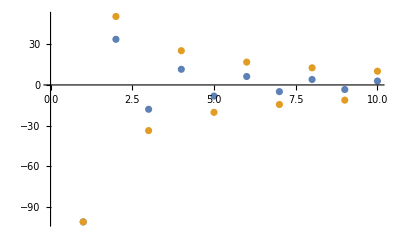

```mathematica
ListPlot[{%354,%365}]
```

```mathematica
Sum[termsFun[n]/.yb->1,{n,1,∞}]
```

$Aborted

```mathematica
{1,3,135,70*3,23625,93555,441441*15,16216200,2791213425}
```

{1,3,135,210,23625,93555,6621615,16216200,2791213425}

```mathematica
945*5
```

4725

{1/9,1,225,2450,2480625,108056025,99423549225,3652293645000,10687067741975625}

```mathematica
Table[numfac[ii] Factorial[2ii]/denoms[[ii]],{ii,1,8}]
```

{16,16/3,128/45,64/35,2048/1575,2048/2079,16384/21021,4096/6435}

```mathematica
prefac=284294494759275;
```

```mathematica
Simplify[Factor[#]]&/@order0eps
```

-(16 π^3 y2 (-2+yb))/(3 √(-1+y1^2) yb^3)-(16 π^3 y2^2 (24-8 yb+3 yb^2))/(105 √(-1+y1^2) yb^7)-(128 π^3 y2^3 (-160+48 yb-18 yb^2+5 yb^3))/(10395 √(-1+y1^2) yb^11)-(64 π^3 y2^4 (896-256 yb+96 yb^2-32 yb^3+7 yb^4))/(45045 √(-1+y1^2) yb^15)-(2048 π^3 y2^5 (-32256+8960 yb-3360 yb^2+1200 yb^3-350 yb^4+63 yb^5))/(72747675 √(-1+y1^2) yb^19)-(2048 π^3 y2^6 (67584-18432 yb+6912 yb^2-2560 yb^3+840 yb^4-216 yb^5+33 yb^6))/(200783583 √(-1+y1^2) yb^23)-(16384 π^3 y2^7 (-1171456+315392 yb-118272 yb^2+44800 yb^3-15680 yb^4+4704 yb^5-1078 yb^6+143 yb^7))/(35137127025 √(-1+y1^2) yb^27)-(4096 π^3 y2^8 (70287360-18743296 yb+7028736 yb^2-2703360 yb^3+985600 yb^4-322560 yb^5+88704 yb^6-18304 yb^7+2145 yb^8))/(644658718275 √(-1+y1^2) yb^31)-(524288 π^3 y2^9 (-28966912+7667712 yb-2875392 yb^2+1118208 yb^3-419328 yb^4+145152 yb^5-44352 yb^6+11232 yb^7-2106 yb^8+221 yb^9))/(40613499251325 √(-1+y1^2) yb^35)+1/(9 √(-1+y1^2))π^3 yb (-192-150 EulerGamma^2-192 ⅈ π+19 π^2-384 Log[2]-96 ⅈ π Log[2]-96 Log[2]^2-96 Log[π]-24 ⅈ π Log[π]-48 Log[2] Log[π]-6 Log[π]^2+60 EulerGamma (8+2 ⅈ π+Log[16 π])-60 (-8+5 EulerGamma-2 ⅈ π-Log[16 π]) Log[yb]-150 Log[yb]^2)

```mathematica
Gamma[(d-2)/2+pw]/Gamma[-pw]/.d->4-2eps/.pw->m-1-2eps//ExpandAll
```

Gamma[-3 eps+m]/Gamma[1+2 eps-m]

```mathematica
qIntegrated[[-1]]//FullForm
```

Times[-1,Power[-1,Times[-2,eps]],Power[2,Plus[2,Times[-4,eps]]],Plus[-11,Times[3,Plus[4,Times[-2,eps]]]],Power[Plus[-1,Times[-2,eps]],-1],Power[eps,-1],Power[Pi,Plus[4,Times[-2,eps],Times[Rational[1,2],Plus[-2,Times[2,eps]]]]],Power[Plus[-1,Power[y1,2]],Rational[-1,2]],Power[yb,Plus[1,Times[2,eps],Times[Rational[1,2],Plus[-2,Times[-2,Plus[-1,Times[-2,eps]]],Times[2,eps]]]]],Gamma[Plus[-1,Times[Rational[1,2],Plus[2,Times[-2,eps]]],Times[-2,eps]]],Power[Gamma[Plus[1,Times[2,eps]]],-1]]

```mathematica
Cases[qIntegrated,Gamma[aa_],Infinity]//DeleteDuplicates;
ExpandAll[#]&/@%//DeleteDuplicates
```

{Gamma[1-3 eps],Gamma[2 eps],Gamma[9-3 eps],Gamma[-8+2 eps],Gamma[8-3 eps],Gamma[-7+2 eps],Gamma[7-3 eps],Gamma[-6+2 eps],Gamma[6-3 eps],Gamma[-5+2 eps],Gamma[5-3 eps],Gamma[-4+2 eps],Gamma[4-3 eps],Gamma[-3+2 eps],Gamma[3-3 eps],Gamma[-2+2 eps],Gamma[2-3 eps],Gamma[-1+2 eps],Gamma[-3 eps],Gamma[1+2 eps]}

```mathematica
Assuming[m>=1,Series[Gamma[-3 eps+m]/Gamma[1+2 eps-m],{eps,0,0}]]//Normal
```

Gamma[m]/Gamma[1-m]

{2 eps,-2 eps,8 eps,-72 eps,1152 eps,-28800 eps,1036800 eps,-50803200 eps,3251404800 eps}

```mathematica
Series[yb^(aa+dd*eps),{eps,0,3}]
```

yb^aa+dd yb^aa Log[yb] eps+1/2 dd^2 yb^aa Log[yb]^2 eps^2+1/6 dd^3 yb^aa Log[yb]^3 eps^3+O[eps]^4

```mathematica
bpolys={ (-2+yb),(24-8 yb+3 yb^2),(-160+48 yb-18 yb^2+5 yb^3),(896-256 yb+96 yb^2-32 yb^3+7 yb^4), (-32256+8960 yb-3360 yb^2+1200 yb^3-350 yb^4+63 yb^5),(67584-18432 yb+6912 yb^2-2560 yb^3+840 yb^4-216 yb^5+33 yb^6),(-1171456+315392 yb-118272 yb^2+44800 yb^3-15680 yb^4+4704 yb^5-1078 yb^6+143 yb^7),(70287360-18743296 yb+7028736 yb^2-2703360 yb^3+985600 yb^4-322560 yb^5+88704 yb^6-18304 yb^7+2145 yb^8),(-28966912+7667712 yb-2875392 yb^2+1118208 yb^3-419328 yb^4+145152 yb^5-44352 yb^6+11232 yb^7-2106 yb^8+221 yb^9)};
```

```mathematica
bpolys1=bpolys/.yb->1
```

{-1,19,-125,711,-25743,54161,-941447,56605025,-23365565}

```mathematica
Table[PolynomialQuotient[bpolys[[n+1]],bpolys[[n]],yb],{n,1,8}]/.yb->1
```

{1,1/9,1/25,1/7,1/189,1/33,1/13,1/2475}

```mathematica
Table[PolynomialRemainder[bpolys[[n+1]],bpolys[[n]],yb],{n,1,8}]/.yb->1
```

{20,-1144/9,716,-180912/7,3420724/63,-31121912/33,56677444,-2315455136/99}

```mathematica
y2ser=order0eps[[1;;9]]
```

(16 π^3 y2)/(3 √(-1+y1^2))-(304 π^3 y2^2)/(105 √(-1+y1^2))+(3200 π^3 y2^3)/(2079 √(-1+y1^2))-(5056 π^3 y2^4)/(5005 √(-1+y1^2))+(17573888 π^3 y2^5)/(24249225 √(-1+y1^2))-(110921728 π^3 y2^6)/(200783583 √(-1+y1^2))+(1186512896 π^3 y2^7)/(2702855925 √(-1+y1^2))-(9274167296 π^3 y2^8)/(25786348731 √(-1+y1^2))+(144121004032 π^3 y2^9)/(477805873545 √(-1+y1^2))

```mathematica
Quit[]
```

```mathematica
y2ser=(16 π^3 y2)/(3 √(-1+y1^2))-(304 π^3 y2^2)/(105 √(-1+y1^2))+(3200 π^3 y2^3)/(2079 √(-1+y1^2))-(5056 π^3 y2^4)/(5005 √(-1+y1^2))+(17573888 π^3 y2^5)/(24249225 √(-1+y1^2))-(110921728 π^3 y2^6)/(200783583 √(-1+y1^2))+(1186512896 π^3 y2^7)/(2702855925 √(-1+y1^2))-(9274167296 π^3 y2^8)/(25786348731 √(-1+y1^2))+(144121004032 π^3 y2^9)/(477805873545 √(-1+y1^2));
```

```mathematica
Clear[f]
fromder[ii_]:=2^(-1+2 #1) Pochhammer[3/2,-1+#1]&[ii]
factors={16/3,-304/105,3200/2079,-5056/5005,17573888/24249225,-110921728/200783583,1186512896/2702855925,-9274167296/25786348731,144121004032/477805873545};
f[i_]:=factors[[i]]
```

```mathematica
Table[f[ii]/2^(2ii+2),{ii,1,8}]
```

{1/3,-19/420,25/4158,-79/80080,8581/48498450,-54161/1606268664,72419/10811423700,-2264201/1650326318784}

```mathematica
Quit[]
```

```mathematica
gammas=Table[Series[Gamma[-3 eps+m]/Gamma[1+2 eps-m]/.m->ii,{eps,0,1}]//Normal,{ii,1,9}]/.eps->1
```

{2,-2,8,-72,1152,-28800,1036800,-50803200,3251404800}

```mathematica
Table[f[ii]/gammas[[ii]],{ii,1,8}]
```

{8/3,152/105,400/2079,632/45045,137296/218243025,866576/45176306175,2317408/5473283248125,18113608/2558650452833475}

```mathematica
n=3;
(2^(2+2 eps) π^2 (-y4)^(-2 eps) yb^(2 eps))/eps*Sum[Power[y2,n-ii]*diffopp[qIntegral[(n-ii)-1-2eps],2ii]/.Pair[Momentum[xx_],Momentum[yy_]]->sp[xx,yy],{ii,0,n}]//ExpandAll
(*Collect[DeleteCases[DeleteCases[Series[%,{eps,0,1}][[3]][[2;;3]]//Expand,Log[aa_],Infinity],EulerGamma,Infinity]//Total,yb]*)
%85[[n]]//Expand
```

-(27 2^(6-4 eps) π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-5+5 eps) Gamma[1-3 eps])/(√(-1+y1^2) Gamma[2 eps])+(3 2^(7-4 eps) π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-5+5 eps) Gamma[1-3 eps])/(eps √(-1+y1^2) Gamma[2 eps])+(27 2^(6-4 eps) eps π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-5+5 eps) Gamma[1-3 eps])/(√(-1+y1^2) Gamma[2 eps])+(2^(8-4 eps) π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-3+5 eps) Gamma[3-3 eps])/(eps √(-1+y1^2) Gamma[-2+2 eps])+(3 2^(7-4 eps) π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-4+5 eps) Gamma[2-3 eps])/(√(-1+y1^2) Gamma[-1+2 eps])-(2^(8-4 eps) π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-4+5 eps) Gamma[2-3 eps])/(eps √(-1+y1^2) Gamma[-1+2 eps])+(45 2^(6-4 eps) π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-6+5 eps) Gamma[-3 eps])/(√(-1+y1^2) Gamma[1+2 eps])-(405 2^(5-4 eps) eps π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-6+5 eps) Gamma[-3 eps])/(√(-1+y1^2) Gamma[1+2 eps])+(405 2^(5-4 eps) eps^2 π^(3-eps) y2^3 (-y4)^(-2 eps) yb^(-6+5 eps) Gamma[-3 eps])/(√(-1+y1^2) Gamma[1+2 eps])

(4096 π^3 y2^3)/(2079 √(-1+y1^2) yb^11)-(2048 π^3 y2^3)/(3465 √(-1+y1^2) yb^10)+(256 π^3 y2^3)/(1155 √(-1+y1^2) yb^9)-(128 π^3 y2^3)/(2079 √(-1+y1^2) yb^8)

```mathematica
Cases[%694,2^xx_,Infinity]//DeleteDuplicates
```

{2^(6-4 eps),2^(7-4 eps),2^(8-4 eps),2^(5-4 eps)}

```mathematica
Do[Print[(%85[[n]])/Factorial[2n]//Expand],{n,1,7}]
```

(16 π^3 y2)/(3 √(-1+y1^2) yb^3)-(8 π^3 y2)/(3 √(-1+y1^2) yb^2)

-(16 π^3 y2^2)/(105 √(-1+y1^2) yb^7)+(16 π^3 y2^2)/(315 √(-1+y1^2) yb^6)-(2 π^3 y2^2)/(105 √(-1+y1^2) yb^5)

(256 π^3 y2^3)/(93555 √(-1+y1^2) yb^11)-(128 π^3 y2^3)/(155925 √(-1+y1^2) yb^10)+(16 π^3 y2^3)/(51975 √(-1+y1^2) yb^9)-(8 π^3 y2^3)/(93555 √(-1+y1^2) yb^8)

-(64 π^3 y2^4)/(2027025 √(-1+y1^2) yb^15)+(128 π^3 y2^4)/(14189175 √(-1+y1^2) yb^14)-(16 π^3 y2^4)/(4729725 √(-1+y1^2) yb^13)+(16 π^3 y2^4)/(14189175 √(-1+y1^2) yb^12)-(π^3 y2^4)/(4054050 √(-1+y1^2) yb^11)

(4096 π^3 y2^5)/(16368226875 √(-1+y1^2) yb^19)-(2048 π^3 y2^5)/(29462808375 √(-1+y1^2) yb^18)+(256 π^3 y2^5)/(9820936125 √(-1+y1^2) yb^17)-(128 π^3 y2^5)/(13749310575 √(-1+y1^2) yb^16)+(16 π^3 y2^5)/(5892561675 √(-1+y1^2) yb^15)-(8 π^3 y2^5)/(16368226875 √(-1+y1^2) yb^14)

-(4096 π^3 y2^6)/(2846107289025 √(-1+y1^2) yb^23)+(4096 π^3 y2^6)/(10435726726425 √(-1+y1^2) yb^22)-(512 π^3 y2^6)/(3478575575475 √(-1+y1^2) yb^21)+(1024 π^3 y2^6)/(18784308107565 √(-1+y1^2) yb^20)-(16 π^3 y2^6)/(894490862265 √(-1+y1^2) yb^19)+(16 π^3 y2^6)/(3478575575475 √(-1+y1^2) yb^18)-(2 π^3 y2^6)/(2846107289025 √(-1+y1^2) yb^17)

(65536 π^3 y2^7)/(10459444287166875 √(-1+y1^2) yb^27)-(32768 π^3 y2^7)/(19424682247595625 √(-1+y1^2) yb^26)+(4096 π^3 y2^7)/(6474894082531875 √(-1+y1^2) yb^25)-(2048 π^3 y2^7)/(8546860188942075 √(-1+y1^2) yb^24)+(512 π^3 y2^7)/(6104900134958625 √(-1+y1^2) yb^23)-(256 π^3 y2^7)/(10174833558264375 √(-1+y1^2) yb^22)+(16 π^3 y2^7)/(2774954606799375 √(-1+y1^2) yb^21)-(8 π^3 y2^7)/(10459444287166875 √(-1+y1^2) yb^20)

```mathematica
Table[(%85[[i]])/Factorial[2i],{i,1,9}]//Total
```

-(8 π^3 y2 (-2+yb))/(3 √(-1+y1^2) yb^3)-(2 π^3 y2^2 (24-8 yb+3 yb^2))/(315 √(-1+y1^2) yb^7)-(8 π^3 y2^3 (-160+48 yb-18 yb^2+5 yb^3))/(467775 √(-1+y1^2) yb^11)-(π^3 y2^4 (896-256 yb+96 yb^2-32 yb^3+7 yb^4))/(28378350 √(-1+y1^2) yb^15)-(8 π^3 y2^5 (-32256+8960 yb-3360 yb^2+1200 yb^3-350 yb^4+63 yb^5))/(1031198293125 √(-1+y1^2) yb^19)-(2 π^3 y2^6 (67584-18432 yb+6912 yb^2-2560 yb^3+840 yb^4-216 yb^5+33 yb^6))/(93921540537825 √(-1+y1^2) yb^23)-(8 π^3 y2^7 (-1171456+315392 yb-118272 yb^2+44800 yb^3-15680 yb^4+4704 yb^5-1078 yb^6+143 yb^7))/(1495700533064863125 √(-1+y1^2) yb^27)-(π^3 y2^8 (70287360-18743296 yb+7028736 yb^2-2703360 yb^3+985600 yb^4-322560 yb^5+88704 yb^6-18304 yb^7+2145 yb^8))/(3292983132796682325000 √(-1+y1^2) yb^31)-(8 π^3 y2^9 (-28966912+7667712 yb-2875392 yb^2+1118208 yb^3-419328 yb^4+145152 yb^5-44352 yb^6+11232 yb^7-2106 yb^8+221 yb^9))/(3967633052128402616334375 √(-1+y1^2) yb^35)

```mathematica
Quit[]
```

```mathematica
Do[Print[(%85[[n]])/Factorial[2n]//Expand],{n,1,7}]
```

(16 π^3 y2)/(3 √(-1+y1^2) yb^3)-(8 π^3 y2)/(3 √(-1+y1^2) yb^2)

-(16 π^3 y2^2)/(105 √(-1+y1^2) yb^7)+(16 π^3 y2^2)/(315 √(-1+y1^2) yb^6)-(2 π^3 y2^2)/(105 √(-1+y1^2) yb^5)

(256 π^3 y2^3)/(93555 √(-1+y1^2) yb^11)-(128 π^3 y2^3)/(155925 √(-1+y1^2) yb^10)+(16 π^3 y2^3)/(51975 √(-1+y1^2) yb^9)-(8 π^3 y2^3)/(93555 √(-1+y1^2) yb^8)

-(64 π^3 y2^4)/(2027025 √(-1+y1^2) yb^15)+(128 π^3 y2^4)/(14189175 √(-1+y1^2) yb^14)-(16 π^3 y2^4)/(4729725 √(-1+y1^2) yb^13)+(16 π^3 y2^4)/(14189175 √(-1+y1^2) yb^12)-(π^3 y2^4)/(4054050 √(-1+y1^2) yb^11)

(4096 π^3 y2^5)/(16368226875 √(-1+y1^2) yb^19)-(2048 π^3 y2^5)/(29462808375 √(-1+y1^2) yb^18)+(256 π^3 y2^5)/(9820936125 √(-1+y1^2) yb^17)-(128 π^3 y2^5)/(13749310575 √(-1+y1^2) yb^16)+(16 π^3 y2^5)/(5892561675 √(-1+y1^2) yb^15)-(8 π^3 y2^5)/(16368226875 √(-1+y1^2) yb^14)

-(4096 π^3 y2^6)/(2846107289025 √(-1+y1^2) yb^23)+(4096 π^3 y2^6)/(10435726726425 √(-1+y1^2) yb^22)-(512 π^3 y2^6)/(3478575575475 √(-1+y1^2) yb^21)+(1024 π^3 y2^6)/(18784308107565 √(-1+y1^2) yb^20)-(16 π^3 y2^6)/(894490862265 √(-1+y1^2) yb^19)+(16 π^3 y2^6)/(3478575575475 √(-1+y1^2) yb^18)-(2 π^3 y2^6)/(2846107289025 √(-1+y1^2) yb^17)

(65536 π^3 y2^7)/(10459444287166875 √(-1+y1^2) yb^27)-(32768 π^3 y2^7)/(19424682247595625 √(-1+y1^2) yb^26)+(4096 π^3 y2^7)/(6474894082531875 √(-1+y1^2) yb^25)-(2048 π^3 y2^7)/(8546860188942075 √(-1+y1^2) yb^24)+(512 π^3 y2^7)/(6104900134958625 √(-1+y1^2) yb^23)-(256 π^3 y2^7)/(10174833558264375 √(-1+y1^2) yb^22)+(16 π^3 y2^7)/(2774954606799375 √(-1+y1^2) yb^21)-(8 π^3 y2^7)/(10459444287166875 √(-1+y1^2) yb^20)

```mathematica
Series[Pi^3/Sqrt[y1^2-1]*Hypergeometric2F1[1,1/2,3/2,-y2],{y2,0,3}]
```

π^3/(√(-1+y1^2))-(π^3 y2)/(3 √(-1+y1^2))+(π^3 y2^2)/(5 √(-1+y1^2))-(π^3 y2^3)/(7 √(-1+y1^2))+O[y2]^(7/2)

```mathematica
denoms={3,315,467775,28378350 ,1031198293125 ,93921540537825,1495700533064863125,3292983132796682325000 ,3967633052128402616334375};
```

```mathematica
numfac[k_]:=FindSequenceFunction[{8,2,8,1,8,2,8,1,8}][k]//FullSimplify
```

```mathematica
Table[%85[[i]],{i,1,9}]/.yb->1
```

{(16 π^3 y2)/(3 √(-1+y1^2)),-(304 π^3 y2^2)/(105 √(-1+y1^2)),(3200 π^3 y2^3)/(2079 √(-1+y1^2)),-(5056 π^3 y2^4)/(5005 √(-1+y1^2)),(17573888 π^3 y2^5)/(24249225 √(-1+y1^2)),-(110921728 π^3 y2^6)/(200783583 √(-1+y1^2)),(1186512896 π^3 y2^7)/(2702855925 √(-1+y1^2)),-(9274167296 π^3 y2^8)/(25786348731 √(-1+y1^2)),(144121004032 π^3 y2^9)/(477805873545 √(-1+y1^2))}

```mathematica
Series[Hypergeometric2F1[1,7/4,11/4,y2/yb^4],{y2,0,3}]
```

1+(7 y2)/(11 yb^4)+(7 y2^2)/(15 yb^8)+(7 y2^3)/(19 yb^12)+O[y2]^4

```mathematica
{16,304,3200,5056,17573888,110921728,1186512896,9274167296,144121004032}
```

{16,304,3200,5056,17573888,110921728,1186512896,9274167296,144121004032}

```mathematica
nn=6;
Pochhammer[3/2,-1+nn]
```

10395/32

```mathematica
Qs=Table[PolynomialQuotient[bpolys[[i+1]],bpolys[[i]],yb]//Factor,{i,1,8}]/.yb->1
```

{1,1/9,1/25,1/7,1/189,1/33,1/13,1/2475}

```mathematica
Rs=Table[PolynomialRemainder[bpolys[[i+1]],bpolys[[i]],yb]//Factor,{i,1,8}]/.yb->1
```

{20,-1144/9,716,-180912/7,3420724/63,-31121912/33,56677444,-2315455136/99}

```mathematica
Table[Qs[[i]]*bpolys1[[i]]+Rs[[i]],{i,1,8}]
```

{19,-125,711,-25743,54161,-941447,56605025,-23365565}

```mathematica
FindSequenceFunction[{1,19,125,711}]
```

FindSequenceFunction[{1,19,125,711}]

```mathematica
Table[bpolys1[[ii]]*numfac[ii],{ii,1,9}]
```

{-8,38,-1000,711,-205944,108322,-7531576,56605025,-186924520}

```mathematica
FindSequenceFunction[{-2+3 yb,(-14+15 yb),(-34+35 yb),(-62+63 yb)}][8]//Simplify
```

-254+255 yb

```mathematica
FactorInteger[2475]
```

{{3,2},{5,2},{11,1}}

```mathematica
FindSequenceFunction[{1,9,25,7}]
```

FindSequenceFunction[{1,9,25,7}]

```mathematica
n=3;
{2^(2n+2),2^(n+2)}
```

{256,32}

```mathematica
FactorInteger[35]
```

{{5,1},{7,1}}

```mathematica
2^3
```

8

```mathematica
Do[Print[FactorInteger[Table[f[ii],{ii,1,9}]//Numerator][[ii]]],{ii,1,9}]
```

{{2,4}}

{{-1,1},{2,4},{19,1}}

{{2,7},{5,2}}

{{-1,1},{2,6},{79,1}}

{{2,11},{8581,1}}

{{-1,1},{2,11},{41,1},{1321,1}}

{{2,14},{139,1},{521,1}}

{{-1,1},{2,12},{2264201,1}}

{{2,19},{274889,1}}

19/2

$Aborted

```mathematica
Series[Cos[ArcTan[(3 √y2)/16]],{y2,0,9}]//Normal
```

1-(9 y2)/512+(243 y2^2)/524288-(3645 y2^3)/268435456+(229635 y2^4)/549755813888-(3720087 y2^5)/281474976710656+(122762871 y2^6)/288230376151711744-(2051893701 y2^7)/147573952589676412928+(277005649635 y2^8)/604462909807314587353088-(4709096043795 y2^9)/309485009821345068724781056

```mathematica
List@@%36/.y2->1
```

{1,-9/512,243/524288,-3645/268435456,229635/549755813888,-3720087/281474976710656,122762871/288230376151711744,-2051893701/147573952589676412928,277005649635/604462909807314587353088,-4709096043795/309485009821345068724781056}

```mathematica
FindGeneratingFunction[%42,y2]
```

16/(√(256+9 y2))

```mathematica
Cos[ArcTan[(3 √y2)/16]]//TrigExpand//FullSimplify
```

1/(√(1+(9 y2)/256))

```mathematica
ord0ineps=Coefficient[qintExpanded,eps,1]
```

-(16 π^3 y2)/(3 b^2 √(-1+y1^2))-(8 π^3 y2^2)/(35 b^4 √(-1+y1^2))-(128 π^3 y2^3)/(6237 b^6 √(-1+y1^2))-(16 π^3 y2^4)/(6435 b^8 √(-1+y1^2))-(2048 π^3 y2^5)/(5773625 b^10 √(-1+y1^2))-(1024 π^3 y2^6)/(18253053 b^12 √(-1+y1^2))-(16384 π^3 y2^7)/(1719999225 b^14 √(-1+y1^2))-(512 π^3 y2^8)/(300540195 b^16 √(-1+y1^2))-(524288 π^3 y2^9)/(1653943408425 b^18 √(-1+y1^2))+1/(9 √(-1+y1^2))(-384 π^3+960 EulerGamma π^3-1200 EulerGamma^2 π^3+250 EulerGamma^3 π^3-384 ⅈ π^4+960 ⅈ EulerGamma π^4-300 ⅈ EulerGamma^2 π^4+152 π^5-95 EulerGamma π^5+6 ⅈ π^6-768 π^3 Log[2]+1920 EulerGamma π^3 Log[2]-600 EulerGamma^2 π^3 Log[2]-768 ⅈ π^4 Log[2]+480 ⅈ EulerGamma π^4 Log[2]+76 π^5 Log[2]-768 π^3 Log[2]^2+480 EulerGamma π^3 Log[2]^2-192 ⅈ π^4 Log[2]^2-128 π^3 Log[2]^3+1152 π^3 Log[b]-2880 EulerGamma π^3 Log[b]+900 EulerGamma^2 π^3 Log[b]+1152 ⅈ π^4 Log[b]-720 ⅈ EulerGamma π^4 Log[b]-114 π^5 Log[b]+2304 π^3 Log[2] Log[b]-1440 EulerGamma π^3 Log[2] Log[b]+576 ⅈ π^4 Log[2] Log[b]+576 π^3 Log[2]^2 Log[b]-1728 π^3 Log[b]^2+1080 EulerGamma π^3 Log[b]^2-432 ⅈ π^4 Log[b]^2-864 π^3 Log[2] Log[b]^2+432 π^3 Log[b]^3-192 π^3 Log[π]+480 EulerGamma π^3 Log[π]-150 EulerGamma^2 π^3 Log[π]-192 ⅈ π^4 Log[π]+120 ⅈ EulerGamma π^4 Log[π]+19 π^5 Log[π]-384 π^3 Log[2] Log[π]+240 EulerGamma π^3 Log[2] Log[π]-96 ⅈ π^4 Log[2] Log[π]-96 π^3 Log[2]^2 Log[π]+576 π^3 Log[b] Log[π]-360 EulerGamma π^3 Log[b] Log[π]+144 ⅈ π^4 Log[b] Log[π]+288 π^3 Log[2] Log[b] Log[π]-216 π^3 Log[b]^2 Log[π]-48 π^3 Log[π]^2+30 EulerGamma π^3 Log[π]^2-12 ⅈ π^4 Log[π]^2-24 π^3 Log[2] Log[π]^2+36 π^3 Log[b] Log[π]^2-2 π^3 Log[π]^3-70 π^3 PolyGamma[2,1])

```mathematica
sery2=-(16 π^3 y2)/(3 b^2 √(-1+y1^2))-(8 π^3 y2^2)/(35 b^4 √(-1+y1^2))-(128 π^3 y2^3)/(6237 b^6 √(-1+y1^2))-(16 π^3 y2^4)/(6435 b^8 √(-1+y1^2))-(2048 π^3 y2^5)/(5773625 b^10 √(-1+y1^2))-(1024 π^3 y2^6)/(18253053 b^12 √(-1+y1^2))-(16384 π^3 y2^7)/(1719999225 b^14 √(-1+y1^2))-(512 π^3 y2^8)/(300540195 b^16 √(-1+y1^2))-(524288 π^3 y2^9)/(1653943408425 b^18 √(-1+y1^2));
```

```mathematica
factors={16/3,8/35,128/6237,16/6435,2048/5773625,1024/18253053,16384/1719999225,512/300540195,524288/1653943408425};
```

```mathematica
FactorInteger[Numerator[factorsodd]]
```

{{{2,4}},{{2,7}},{{2,11}},{{2,14}}}

```mathematica
FindSequenceFunction[{4,6,10,18}]
```

2+2^#1&

```mathematica
Table[Expand[sery2[[ii]]/Factorial[2*ii]],{ii,Length@sery2}]
```

{-(8 π^3 y2)/(3 √(-1+y1^2) b^2),-(π^3 y2^2)/(105 √(-1+y1^2) b^4),-(8 π^3 y2^3)/(280665 √(-1+y1^2) b^6),-(π^3 y2^4)/(16216200 √(-1+y1^2) b^8),-(8 π^3 y2^5)/(81841134375 √(-1+y1^2) b^10),-(π^3 y2^6)/(8538321867075 √(-1+y1^2) b^12),-(8 π^3 y2^7)/(73216110010168125 √(-1+y1^2) b^14),-(π^3 y2^8)/(12281522173600680000 √(-1+y1^2) b^16),-(8 π^3 y2^9)/(161577816602514133696875 √(-1+y1^2) b^18)}

```mathematica
num[n_]:=FindSequenceFunction[{8,1,8,1,8,1,8,1}][n]
```

```mathematica
num[9]//Simplify
```

8

```mathematica
Table[(Factorial[4*n]*n^3)/(2^(2*n+(3*(1+(-1)^n))/2)*Factorial[2*n]),{n,0,9}]
```

{0,3,105,280665,16216200,81841134375,8538321867075,73216110010168125,12281522173600680000,161577816602514133696875}

```mathematica
den[n_]:=(Factorial[4*n]*n^3)/(2^(2*n+(3*(1+(-1)^n))/2)*Factorial[2*n])
```

```mathematica
Clear[func,coeff]
coeff[n_]:=(Factorial[2n]*num[n])/den[n]*Pi^3/(√(-1+Power[y1,2])Power[b,2n])
```

```mathematica
Sum[coeff[ii]*y2^ii,{ii,1,Infinity}]
```

∑_(ii=1)^∞ (2^(-1+3/2 (1+(-1)^ii)+2 ii) (9-7 (-1)^ii) b^(-2 ii) π^3 y2^ii ((2 ii)!)^2)/(ii^3 √(-1+y1^2) (4 ii)!)

```mathematica
asym[n_]:=coeff[n]/.Factorial[xx_]->√(2Pi*xx)*(xx/E)^xx//PowerExpand//FullSimplify
```

```mathematica
Assuming[{Element[b,Reals],Element[n,Integers],n>0},Abs[(asym[n+1] y2^(n+1))/(asym[n] y2^n)]]
```

2^(-2-3 Re[(-1)^n]) Abs[((9+7 (-1)^n) b^(2 n-2 (1+n)) n^(5/2) y2)/((9-7 (-1)^n) (1+n)^(5/2))]

```mathematica
(asym[n+1] y2^(n+1))/(asym[n] y2^n)//Expand//FullSimplify
```

-(2^(-2-3 (-1)^n) (9+7 (-1)^n) (n/(1+n))^(5/2) y2)/((-9+7 (-1)^n) b^2)

```mathematica
asymptotic=Series[(coeff[n+1] y2^(n+1))/(coeff[n] y2^n),{n,Infinity,1}]//Normal//Expand//Simplify
```

-(2^(-3 (1+(-1)^n)) (9+7 (-1)^n) (-5+2 n) y2)/((-9+7 (-1)^n) b^2 n)

```mathematica
asymptotic=asymptotic/.(2^(-3 (1+(-1)^n)) (9+7 (-1)^n))/(-9+7 (-1)^n)->-1/8
```

((-5+2 n) y2)/(8 b^2 n)

```mathematica
Limit[Abs[((-5+2 n) y2)/(8 b^2 n)],n->Infinity,Assumptions->{Element[b,Reals],Element[y2,Reals],y2<0}]/.y2->-Subscript[ψ, 2]
```

ψ_2/(4 Abs[b^2])

```mathematica
coeff[n]
```

(2^(-1+3/2 (1+(-1)^n)+2 n) (9-7 (-1)^n) b^(-2 n) π^3 ((2 n)!)^2)/(n^3 √(-1+y1^2) (4 n)!)

```mathematica
Sum[(9-7 (-1)^n),n]
```

16 (1+Floor[1/2 (-2+n)])+2 (1+Floor[1/2 (-1+n)])

1/64

```mathematica
E^Interval[{0,Pi}]//Expand
```

Interval[{1,ⅇ^π}]

```mathematica
SumConvergence[coeff[n] y2^n,n]
```

Abs[b]>1/2 (Im[y2]^2+Re[y2]^2)^(1/4)

```mathematica
Assuming[%103,Sum[coeff[n]*y2^n,n]]
```

(π^3 (-7 [n]+9 [n]))/(√(-1+y1^2))

```mathematica
y2resumed[ord_]:=(π^3 (-7 [ord]+9 [ord]))/(√(-1+y1^2))//Expand
```

```mathematica
y2resumed[30]
```

(16 π^3 y2)/(3 b^2 √(-1+y1^2))+(8 π^3 y2^2)/(35 b^4 √(-1+y1^2))+(128 π^3 y2^3)/(6237 b^6 √(-1+y1^2))+(16 π^3 y2^4)/(6435 b^8 √(-1+y1^2))+(2048 π^3 y2^5)/(5773625 b^10 √(-1+y1^2))+(1024 π^3 y2^6)/(18253053 b^12 √(-1+y1^2))+(16384 π^3 y2^7)/(1719999225 b^14 √(-1+y1^2))+(512 π^3 y2^8)/(300540195 b^16 √(-1+y1^2))+(524288 π^3 y2^9)/(1653943408425 b^18 √(-1+y1^2))+(262144 π^3 y2^10)/(4307704025625 b^20 √(-1+y1^2))+(4194304 π^3 y2^11)/(350069465088915 b^22 √(-1+y1^2))+(524288 π^3 y2^12)/(217671324860925 b^24 √(-1+y1^2))+(67108864 π^3 y2^13)/(136191627110873061 b^26 √(-1+y1^2))+(33554432 π^3 y2^14)/(327937609507603865 b^28 √(-1+y1^2))+(536870912 π^3 y2^15)/(24946435173837956625 b^30 √(-1+y1^2))+(4194304 π^3 y2^16)/(916312070471295267 b^32 √(-1+y1^2))+(34359738368 π^3 y2^17)/(34947448191964238380905 b^34 √(-1+y1^2))+(17179869184 π^3 y2^18)/(80647910465453503009929 b^36 √(-1+y1^2))+(274877906944 π^3 y2^19)/(5909560628673384953900175 b^38 √(-1+y1^2))+(34359738368 π^3 y2^20)/(3359600272916755514425625 b^40 √(-1+y1^2))+(4398046511104 π^3 y2^21)/(1943548751601040423347553815 b^42 √(-1+y1^2))+(2199023255552 π^3 y2^22)/(4367095082877817116563519475 b^44 √(-1+y1^2))+(35184372088832 π^3 y2^23)/(312384264585095854370287377855 b^46 √(-1+y1^2))+(1099511627776 π^3 y2^24)/(43436702343597517631845820925 b^48 √(-1+y1^2))+(1125899906842624 π^3 y2^25)/(197053407315555065107055658703125 b^50 √(-1+y1^2))+(562949953421312 π^3 y2^26)/(434749458541588792282566654689349 b^52 √(-1+y1^2))+(9007199254740992 π^3 y2^27)/(30579735759183215613605086785599535 b^54 √(-1+y1^2))+(1125899906842624 π^3 y2^28)/(16746548174536890218824171579470489 b^56 √(-1+y1^2))+(144115188075855872 π^3 y2^29)/(9361137126343301781956652459560083005 b^58 √(-1+y1^2))

```mathematica
test=terms[0];
test=test/.sol/.y5->0//PowerExpand//Expand
```

-(11 (-1)^(-2 eps) 2^(2+2 eps) π^2 y4^(-1-2 eps))/((-5+d) eps)+(3 (-1)^(-2 eps) 2^(2+2 eps) d π^2 y4^(-1-2 eps))/((-5+d) eps)

```mathematica
test=test/.qIntegralRule/.d->4-2eps//PowerExpand
```

-(11 (-1)^(-2 eps) 2^(4+2 (-1-2 eps)) b^(-2-2 (-1-2 eps)+2 eps) π^(4-2 eps+1/2 (-2+2 eps)) Gamma[-1+1/2 (2-2 eps)-2 eps])/((-1-2 eps) eps √(-1+y1^2) Gamma[1+2 eps])+(3 (-1)^(-2 eps) 2^(4+2 (-1-2 eps)) b^(-2-2 (-1-2 eps)+2 eps) (4-2 eps) π^(4-2 eps+1/2 (-2+2 eps)) Gamma[-1+1/2 (2-2 eps)-2 eps])/((-1-2 eps) eps √(-1+y1^2) Gamma[1+2 eps])

```mathematica
Series[test,{eps,0,3}];
Coefficient[%,eps,1]//Expand
```

-(128 π^3)/(3 √(-1+y1^2))+(320 EulerGamma π^3)/(3 √(-1+y1^2))-(400 EulerGamma^2 π^3)/(3 √(-1+y1^2))+(250 EulerGamma^3 π^3)/(9 √(-1+y1^2))-(128 ⅈ π^4)/(3 √(-1+y1^2))+(320 ⅈ EulerGamma π^4)/(3 √(-1+y1^2))-(100 ⅈ EulerGamma^2 π^4)/(3 √(-1+y1^2))+(152 π^5)/(9 √(-1+y1^2))-(95 EulerGamma π^5)/(9 √(-1+y1^2))+(2 ⅈ π^6)/(3 √(-1+y1^2))-(256 π^3 Log[2])/(3 √(-1+y1^2))+(640 EulerGamma π^3 Log[2])/(3 √(-1+y1^2))-(200 EulerGamma^2 π^3 Log[2])/(3 √(-1+y1^2))-(256 ⅈ π^4 Log[2])/(3 √(-1+y1^2))+(160 ⅈ EulerGamma π^4 Log[2])/(3 √(-1+y1^2))+(76 π^5 Log[2])/(9 √(-1+y1^2))-(256 π^3 Log[2]^2)/(3 √(-1+y1^2))+(160 EulerGamma π^3 Log[2]^2)/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[2]^2)/(3 √(-1+y1^2))-(128 π^3 Log[2]^3)/(9 √(-1+y1^2))+(128 π^3 Log[b])/(√(-1+y1^2))-(320 EulerGamma π^3 Log[b])/(√(-1+y1^2))+(100 EulerGamma^2 π^3 Log[b])/(√(-1+y1^2))+(128 ⅈ π^4 Log[b])/(√(-1+y1^2))-(80 ⅈ EulerGamma π^4 Log[b])/(√(-1+y1^2))-(38 π^5 Log[b])/(3 √(-1+y1^2))+(256 π^3 Log[2] Log[b])/(√(-1+y1^2))-(160 EulerGamma π^3 Log[2] Log[b])/(√(-1+y1^2))+(64 ⅈ π^4 Log[2] Log[b])/(√(-1+y1^2))+(64 π^3 Log[2]^2 Log[b])/(√(-1+y1^2))-(192 π^3 Log[b]^2)/(√(-1+y1^2))+(120 EulerGamma π^3 Log[b]^2)/(√(-1+y1^2))-(48 ⅈ π^4 Log[b]^2)/(√(-1+y1^2))-(96 π^3 Log[2] Log[b]^2)/(√(-1+y1^2))+(48 π^3 Log[b]^3)/(√(-1+y1^2))-(64 π^3 Log[π])/(3 √(-1+y1^2))+(160 EulerGamma π^3 Log[π])/(3 √(-1+y1^2))-(50 EulerGamma^2 π^3 Log[π])/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[π])/(3 √(-1+y1^2))+(40 ⅈ EulerGamma π^4 Log[π])/(3 √(-1+y1^2))+(19 π^5 Log[π])/(9 √(-1+y1^2))-(128 π^3 Log[2] Log[π])/(3 √(-1+y1^2))+(80 EulerGamma π^3 Log[2] Log[π])/(3 √(-1+y1^2))-(32 ⅈ π^4 Log[2] Log[π])/(3 √(-1+y1^2))-(32 π^3 Log[2]^2 Log[π])/(3 √(-1+y1^2))+(64 π^3 Log[b] Log[π])/(√(-1+y1^2))-(40 EulerGamma π^3 Log[b] Log[π])/(√(-1+y1^2))+(16 ⅈ π^4 Log[b] Log[π])/(√(-1+y1^2))+(32 π^3 Log[2] Log[b] Log[π])/(√(-1+y1^2))-(24 π^3 Log[b]^2 Log[π])/(√(-1+y1^2))-(16 π^3 Log[π]^2)/(3 √(-1+y1^2))+(10 EulerGamma π^3 Log[π]^2)/(3 √(-1+y1^2))-(4 ⅈ π^4 Log[π]^2)/(3 √(-1+y1^2))-(8 π^3 Log[2] Log[π]^2)/(3 √(-1+y1^2))+(4 π^3 Log[b] Log[π]^2)/(√(-1+y1^2))-(2 π^3 Log[π]^3)/(9 √(-1+y1^2))-(70 π^3 PolyGamma[2,1])/(9 √(-1+y1^2))

```mathematica
ord0ineps[[10]]//Expand
```

-(128 π^3)/(3 √(-1+y1^2))+(320 EulerGamma π^3)/(3 √(-1+y1^2))-(400 EulerGamma^2 π^3)/(3 √(-1+y1^2))+(250 EulerGamma^3 π^3)/(9 √(-1+y1^2))-(128 ⅈ π^4)/(3 √(-1+y1^2))+(320 ⅈ EulerGamma π^4)/(3 √(-1+y1^2))-(100 ⅈ EulerGamma^2 π^4)/(3 √(-1+y1^2))+(152 π^5)/(9 √(-1+y1^2))-(95 EulerGamma π^5)/(9 √(-1+y1^2))+(2 ⅈ π^6)/(3 √(-1+y1^2))-(256 π^3 Log[2])/(3 √(-1+y1^2))+(640 EulerGamma π^3 Log[2])/(3 √(-1+y1^2))-(200 EulerGamma^2 π^3 Log[2])/(3 √(-1+y1^2))-(256 ⅈ π^4 Log[2])/(3 √(-1+y1^2))+(160 ⅈ EulerGamma π^4 Log[2])/(3 √(-1+y1^2))+(76 π^5 Log[2])/(9 √(-1+y1^2))-(256 π^3 Log[2]^2)/(3 √(-1+y1^2))+(160 EulerGamma π^3 Log[2]^2)/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[2]^2)/(3 √(-1+y1^2))-(128 π^3 Log[2]^3)/(9 √(-1+y1^2))+(128 π^3 Log[b])/(√(-1+y1^2))-(320 EulerGamma π^3 Log[b])/(√(-1+y1^2))+(100 EulerGamma^2 π^3 Log[b])/(√(-1+y1^2))+(128 ⅈ π^4 Log[b])/(√(-1+y1^2))-(80 ⅈ EulerGamma π^4 Log[b])/(√(-1+y1^2))-(38 π^5 Log[b])/(3 √(-1+y1^2))+(256 π^3 Log[2] Log[b])/(√(-1+y1^2))-(160 EulerGamma π^3 Log[2] Log[b])/(√(-1+y1^2))+(64 ⅈ π^4 Log[2] Log[b])/(√(-1+y1^2))+(64 π^3 Log[2]^2 Log[b])/(√(-1+y1^2))-(192 π^3 Log[b]^2)/(√(-1+y1^2))+(120 EulerGamma π^3 Log[b]^2)/(√(-1+y1^2))-(48 ⅈ π^4 Log[b]^2)/(√(-1+y1^2))-(96 π^3 Log[2] Log[b]^2)/(√(-1+y1^2))+(48 π^3 Log[b]^3)/(√(-1+y1^2))-(64 π^3 Log[π])/(3 √(-1+y1^2))+(160 EulerGamma π^3 Log[π])/(3 √(-1+y1^2))-(50 EulerGamma^2 π^3 Log[π])/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[π])/(3 √(-1+y1^2))+(40 ⅈ EulerGamma π^4 Log[π])/(3 √(-1+y1^2))+(19 π^5 Log[π])/(9 √(-1+y1^2))-(128 π^3 Log[2] Log[π])/(3 √(-1+y1^2))+(80 EulerGamma π^3 Log[2] Log[π])/(3 √(-1+y1^2))-(32 ⅈ π^4 Log[2] Log[π])/(3 √(-1+y1^2))-(32 π^3 Log[2]^2 Log[π])/(3 √(-1+y1^2))+(64 π^3 Log[b] Log[π])/(√(-1+y1^2))-(40 EulerGamma π^3 Log[b] Log[π])/(√(-1+y1^2))+(16 ⅈ π^4 Log[b] Log[π])/(√(-1+y1^2))+(32 π^3 Log[2] Log[b] Log[π])/(√(-1+y1^2))-(24 π^3 Log[b]^2 Log[π])/(√(-1+y1^2))-(16 π^3 Log[π]^2)/(3 √(-1+y1^2))+(10 EulerGamma π^3 Log[π]^2)/(3 √(-1+y1^2))-(4 ⅈ π^4 Log[π]^2)/(3 √(-1+y1^2))-(8 π^3 Log[2] Log[π]^2)/(3 √(-1+y1^2))+(4 π^3 Log[b] Log[π]^2)/(√(-1+y1^2))-(2 π^3 Log[π]^3)/(9 √(-1+y1^2))-(70 π^3 PolyGamma[2,1])/(9 √(-1+y1^2))

```mathematica
SameQ[%283,%325]
```

True

```mathematica
zeroContrib = ord0ineps[[10]]//Expand;
```

```mathematica
Collect[zeroContrib,EulerGamma]
```

-(128 π^3)/(3 √(-1+y1^2))+(250 EulerGamma^3 π^3)/(9 √(-1+y1^2))-(128 ⅈ π^4)/(3 √(-1+y1^2))+(152 π^5)/(9 √(-1+y1^2))+(2 ⅈ π^6)/(3 √(-1+y1^2))-(256 π^3 Log[2])/(3 √(-1+y1^2))-(256 ⅈ π^4 Log[2])/(3 √(-1+y1^2))+(76 π^5 Log[2])/(9 √(-1+y1^2))-(256 π^3 Log[2]^2)/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[2]^2)/(3 √(-1+y1^2))-(128 π^3 Log[2]^3)/(9 √(-1+y1^2))+(128 π^3 Log[b])/(√(-1+y1^2))+(128 ⅈ π^4 Log[b])/(√(-1+y1^2))-(38 π^5 Log[b])/(3 √(-1+y1^2))+(256 π^3 Log[2] Log[b])/(√(-1+y1^2))+(64 ⅈ π^4 Log[2] Log[b])/(√(-1+y1^2))+(64 π^3 Log[2]^2 Log[b])/(√(-1+y1^2))-(192 π^3 Log[b]^2)/(√(-1+y1^2))-(48 ⅈ π^4 Log[b]^2)/(√(-1+y1^2))-(96 π^3 Log[2] Log[b]^2)/(√(-1+y1^2))+(48 π^3 Log[b]^3)/(√(-1+y1^2))-(64 π^3 Log[π])/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[π])/(3 √(-1+y1^2))+(19 π^5 Log[π])/(9 √(-1+y1^2))-(128 π^3 Log[2] Log[π])/(3 √(-1+y1^2))-(32 ⅈ π^4 Log[2] Log[π])/(3 √(-1+y1^2))-(32 π^3 Log[2]^2 Log[π])/(3 √(-1+y1^2))+(64 π^3 Log[b] Log[π])/(√(-1+y1^2))+(16 ⅈ π^4 Log[b] Log[π])/(√(-1+y1^2))+(32 π^3 Log[2] Log[b] Log[π])/(√(-1+y1^2))-(24 π^3 Log[b]^2 Log[π])/(√(-1+y1^2))-(16 π^3 Log[π]^2)/(3 √(-1+y1^2))-(4 ⅈ π^4 Log[π]^2)/(3 √(-1+y1^2))-(8 π^3 Log[2] Log[π]^2)/(3 √(-1+y1^2))+(4 π^3 Log[b] Log[π]^2)/(√(-1+y1^2))-(2 π^3 Log[π]^3)/(9 √(-1+y1^2))+EulerGamma^2 (-(400 π^3)/(3 √(-1+y1^2))-(100 ⅈ π^4)/(3 √(-1+y1^2))-(200 π^3 Log[2])/(3 √(-1+y1^2))+(100 π^3 Log[b])/(√(-1+y1^2))-(50 π^3 Log[π])/(3 √(-1+y1^2)))+EulerGamma ((320 π^3)/(3 √(-1+y1^2))+(320 ⅈ π^4)/(3 √(-1+y1^2))-(95 π^5)/(9 √(-1+y1^2))+(640 π^3 Log[2])/(3 √(-1+y1^2))+(160 ⅈ π^4 Log[2])/(3 √(-1+y1^2))+(160 π^3 Log[2]^2)/(3 √(-1+y1^2))-(320 π^3 Log[b])/(√(-1+y1^2))-(80 ⅈ π^4 Log[b])/(√(-1+y1^2))-(160 π^3 Log[2] Log[b])/(√(-1+y1^2))+(120 π^3 Log[b]^2)/(√(-1+y1^2))+(160 π^3 Log[π])/(3 √(-1+y1^2))+(40 ⅈ π^4 Log[π])/(3 √(-1+y1^2))+(80 π^3 Log[2] Log[π])/(3 √(-1+y1^2))-(40 π^3 Log[b] Log[π])/(√(-1+y1^2))+(10 π^3 Log[π]^2)/(3 √(-1+y1^2)))-(70 π^3 PolyGamma[2,1])/(9 √(-1+y1^2))

```mathematica
ord0ineps[[10]]
```

1/(9 √(-1+y1^2))(-384 π^3+960 EulerGamma π^3-1200 EulerGamma^2 π^3+250 EulerGamma^3 π^3-384 ⅈ π^4+960 ⅈ EulerGamma π^4-300 ⅈ EulerGamma^2 π^4+152 π^5-95 EulerGamma π^5+6 ⅈ π^6-768 π^3 Log[2]+1920 EulerGamma π^3 Log[2]-600 EulerGamma^2 π^3 Log[2]-768 ⅈ π^4 Log[2]+480 ⅈ EulerGamma π^4 Log[2]+76 π^5 Log[2]-768 π^3 Log[2]^2+480 EulerGamma π^3 Log[2]^2-192 ⅈ π^4 Log[2]^2-128 π^3 Log[2]^3+1152 π^3 Log[b]-2880 EulerGamma π^3 Log[b]+900 EulerGamma^2 π^3 Log[b]+1152 ⅈ π^4 Log[b]-720 ⅈ EulerGamma π^4 Log[b]-114 π^5 Log[b]+2304 π^3 Log[2] Log[b]-1440 EulerGamma π^3 Log[2] Log[b]+576 ⅈ π^4 Log[2] Log[b]+576 π^3 Log[2]^2 Log[b]-1728 π^3 Log[b]^2+1080 EulerGamma π^3 Log[b]^2-432 ⅈ π^4 Log[b]^2-864 π^3 Log[2] Log[b]^2+432 π^3 Log[b]^3-192 π^3 Log[π]+480 EulerGamma π^3 Log[π]-150 EulerGamma^2 π^3 Log[π]-192 ⅈ π^4 Log[π]+120 ⅈ EulerGamma π^4 Log[π]+19 π^5 Log[π]-384 π^3 Log[2] Log[π]+240 EulerGamma π^3 Log[2] Log[π]-96 ⅈ π^4 Log[2] Log[π]-96 π^3 Log[2]^2 Log[π]+576 π^3 Log[b] Log[π]-360 EulerGamma π^3 Log[b] Log[π]+144 ⅈ π^4 Log[b] Log[π]+288 π^3 Log[2] Log[b] Log[π]-216 π^3 Log[b]^2 Log[π]-48 π^3 Log[π]^2+30 EulerGamma π^3 Log[π]^2-12 ⅈ π^4 Log[π]^2-24 π^3 Log[2] Log[π]^2+36 π^3 Log[b] Log[π]^2-2 π^3 Log[π]^3-70 π^3 PolyGamma[2,1])

```mathematica
finalResOrd1Eps =c[1]/(9 √(-1+y1^2))+Sum[coeff[n] y2^n,{n,1,Infinity}]
```

c[1]/(9 √(-1+y1^2))+∑_(n=1)^∞ (2^(-1+3/2 (1+(-1)^n)+2 n) (9-7 (-1)^n) b^(-2 n) π^3 y2^n ((2 n)!)^2)/(n^3 √(-1+y1^2) (4 n)!)

```mathematica
Sum[(2^(-1+3/2 (1+(-1)^n)+2 n) (9-7 (-1)^n)  π^3  ((2 n)!)^2)/(n^3 √(-1+y1^2) (4 n)!),{n,1,Infinity}]
```

∑_(n=1)^∞ (2^(-1+3/2 (1+(-1)^n)+2 n) (9-7 (-1)^n) π^3 ((2 n)!)^2)/(n^3 √(-1+y1^2) (4 n)!)

```mathematica
(2^(-1+3/2 (1+(-1)^n)+2 n)     ((2 n)!)^2)/(n^3  (4 n)!)/.n->10//N
```

3.04273×10^-8

### Try and resum the result

```mathematica
coeff[n]//PowerExpand//FunctionExpand//FullSimplify
```

-(2^(1/2 (3+3 (-1)^n-4 n)) (-9+7 (-1)^n) b^(-2 n) π^(7/2) Gamma[2 n])/(n^2 √(-1+y1^2) Gamma[1/2+2 n])

```mathematica
Clear[func]
func[n_,x_]:=Sum[coeff[m]*x^m,{m,1,n}]
```

```mathematica
D[func[p,x],x]
```

$Aborted

```mathematica
D[func[Infinity,x],x]
```

∑_(m=1)^∞ (2^(-1+3/2 (1+(-1)^m)+2 m) (9-7 (-1)^m) b^(-2 m) π^3 x^(-1+m) ((2 m)!)^2)/(m^2 √(-1+y1^2) (4 m)!)

```mathematica
D[[1+mm],x]
```

$Aborted

```mathematica
D[func[n,x],x]
```

(2^(-1+3/2 (1+(-1)^n)+2 n) (9-7 (-1)^n) b^(-2 n) π^3 x^(-1+n) ((2 n)!)^2)/(n^2 √(-1+y1^2) (4 n)!)

```mathematica
func[n,x]*n/x
```

(2^(-1+3/2 (1+(-1)^n)+2 n) (9-7 (-1)^n) b^(-2 n) π^3 x^(-1+n) ((2 n)!)^2)/(n^2 √(-1+y1^2) (4 n)!)

```mathematica
SameQ[%86,%88]
```

True

```mathematica
DSolve[D[f[n,x],x]==n/x f[n,x],f[n,x],x]
```

{{f[n,x]→x^n C[1]}}

```mathematica
Series[Exp[x],{x,0,3}]
```

1+x+x^2/2+x^3/6+O[x]^4

## Other stuff

```mathematica
Clear[ii]
qintegrated=Total[Table[Expand[Power[(-I*Subscript[y, 3])/b,ii-1]D[CoefficientList[ordTerms,y5][[ii]]/.qIntegralRule,{b,ii-1}]],{ii,1,10}]]
```

```mathematica
qintegrated/.Subscript[y, 3]->0
```

((-1)^(-2 eps) 2^(1+d-2 eps) (b^2)^(1-d/2+2 eps) π^(1+d/2) y2 Gamma[1/2 (-2+d)-2 eps])/(3 (-5+d) (-2+d) eps √(-1+y1^2) Gamma[2 eps])-((-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(1-d/2+2 eps) d π^(1+d/2) y2 Gamma[1/2 (-2+d)-2 eps])/(3 (-5+d) (-2+d) eps √(-1+y1^2) Gamma[2 eps])-(11 (-1)^(-2 eps) 2^(1+d-2 eps) (b^2)^(-d/2+2 eps) π^(1+d/2) y2^8 Gamma[7+1/2 (-2+d)-2 eps])/(1215 b^12 (-5+d) (12+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) (17+3 d) (19+3 d) eps √(-1+y1^2) Gamma[-7+2 eps])-(263 (-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(-d/2+2 eps) d π^(1+d/2) y2^8 Gamma[7+1/2 (-2+d)-2 eps])/(76545 b^12 (-5+d) (12+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) (17+3 d) (19+3 d) eps √(-1+y1^2) Gamma[-7+2 eps])+(131 (-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(-d/2+2 eps) d^2 π^(1+d/2) y2^8 Gamma[7+1/2 (-2+d)-2 eps])/(76545 b^12 (-5+d) (12+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) (17+3 d) (19+3 d) eps √(-1+y1^2) Gamma[-7+2 eps])+(23 (-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(-d/2+2 eps) d^3 π^(1+d/2) y2^8 Gamma[7+1/2 (-2+d)-2 eps])/(76545 b^12 (-5+d) (12+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) (17+3 d) (19+3 d) eps √(-1+y1^2) Gamma[-7+2 eps])+((-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(-d/2+2 eps) d^4 π^(1+d/2) y2^8 Gamma[7+1/2 (-2+d)-2 eps])/(76545 b^12 (-5+d) (12+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) (17+3 d) (19+3 d) eps √(-1+y1^2) Gamma[-7+2 eps])+((-1)^(-2 eps) 2^(3+d-2 eps) (b^2)^(-d/2+2 eps) π^(1+d/2) y2^7 Gamma[6+1/2 (-2+d)-2 eps])/(1215 b^10 (-5+d) (10+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) eps √(-1+y1^2) Gamma[-6+2 eps])+((-1)^(-2 eps) 2^(1+d-2 eps) (b^2)^(-d/2+2 eps) d π^(1+d/2) y2^7 Gamma[6+1/2 (-2+d)-2 eps])/(76545 b^10 (-5+d) (10+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) eps √(-1+y1^2) Gamma[-6+2 eps])-((-1)^(-2 eps) 2^(3+d-2 eps) (b^2)^(-d/2+2 eps) d^2 π^(1+d/2) y2^7 Gamma[6+1/2 (-2+d)-2 eps])/(25515 b^10 (-5+d) (10+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) eps √(-1+y1^2) Gamma[-6+2 eps])-((-1)^(-2 eps) 2^(1+d-2 eps) (b^2)^(-d/2+2 eps) d^3 π^(1+d/2) y2^7 Gamma[6+1/2 (-2+d)-2 eps])/(76545 b^10 (-5+d) (10+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) (13+3 d) eps √(-1+y1^2) Gamma[-6+2 eps])-(7 (-1)^(-2 eps) 2^(2+d-2 eps) (b^2)^(-d/2+2 eps) π^(1+d/2) y2^6 Gamma[5+1/2 (-2+d)-2 eps])/(729 b^8 (-5+d) (8+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) eps √(-1+y1^2) Gamma[-5+2 eps])-(13 (-1)^(-2 eps) 2^(d-2 eps) (b^2)^(-d/2+2 eps) d π^(1+d/2) y2^6 Gamma[5+1/2 (-2+d)-2 eps])/(3645 b^8 (-5+d) (8+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) eps √(-1+y1^2) Gamma[-5+2 eps])+((-1)^(-2 eps) 2^(3+d-2 eps) (b^2)^(-d/2+2 eps) d^2 π^(1+d/2) y2^6 Gamma[5+1/2 (-2+d)-2 eps])/(3645 b^8 (-5+d) (8+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) eps √(-1+y1^2) Gamma[-5+2 eps])+((-1)^(-2 eps) 2^(d-2 eps) (b^2)^(-d/2+2 eps) d^3 π^(1+d/2) y2^6 Gamma[5+1/2 (-2+d)-2 eps])/(3645 b^8 (-5+d) (8+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) (11+3 d) eps √(-1+y1^2) Gamma[-5+2 eps])+((-1)^(-2 eps) 2^(2+d-2 eps) (b^2)^(-d/2+2 eps) π^(1+d/2) y2^5 Gamma[4+1/2 (-2+d)-2 eps])/(27 b^6 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) eps √(-1+y1^2) Gamma[-4+2 eps])+(17 (-1)^(-2 eps) 2^(d-2 eps) (b^2)^(-d/2+2 eps) d π^(1+d/2) y2^5 Gamma[4+1/2 (-2+d)-2 eps])/(405 b^6 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) eps √(-1+y1^2) Gamma[-4+2 eps])-((-1)^(-2 eps) 2^(2+d-2 eps) (b^2)^(-d/2+2 eps) d^2 π^(1+d/2) y2^5 Gamma[4+1/2 (-2+d)-2 eps])/(405 b^6 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) eps √(-1+y1^2) Gamma[-4+2 eps])-((-1)^(-2 eps) 2^(d-2 eps) (b^2)^(-d/2+2 eps) d^3 π^(1+d/2) y2^5 Gamma[4+1/2 (-2+d)-2 eps])/(405 b^6 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d) eps √(-1+y1^2) Gamma[-4+2 eps])-((-1)^(-2 eps) 2^(1+d-2 eps) (b^2)^(-d/2+2 eps) π^(1+d/2) y2^4 Gamma[3+1/2 (-2+d)-2 eps])/(27 b^4 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) eps √(-1+y1^2) Gamma[-3+2 eps])-((-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(-d/2+2 eps) d π^(1+d/2) y2^4 Gamma[3+1/2 (-2+d)-2 eps])/(81 b^4 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) eps √(-1+y1^2) Gamma[-3+2 eps])+((-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(-d/2+2 eps) d^2 π^(1+d/2) y2^4 Gamma[3+1/2 (-2+d)-2 eps])/(81 b^4 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) eps √(-1+y1^2) Gamma[-3+2 eps])+((-1)^(-2 eps) 2^(2+d-2 eps) (b^2)^(-1-d/2+2 eps) π^(1+d/2) y2^3 Gamma[2+1/2 (-2+d)-2 eps])/(27 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d) eps √(-1+y1^2) Gamma[-2+2 eps])+((-1)^(-2 eps) 2^(d-2 eps) (b^2)^(-1-d/2+2 eps) d π^(1+d/2) y2^3 Gamma[2+1/2 (-2+d)-2 eps])/(9 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d) eps √(-1+y1^2) Gamma[-2+2 eps])-((-1)^(-2 eps) 2^(d-2 eps) (b^2)^(-1-d/2+2 eps) d^2 π^(1+d/2) y2^3 Gamma[2+1/2 (-2+d)-2 eps])/(27 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d) eps √(-1+y1^2) Gamma[-2+2 eps])-(5 (-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(-d/2+2 eps) π^(1+d/2) y2^2 Gamma[1+1/2 (-2+d)-2 eps])/(3 (-5+d) (-7+3 d) (-5+3 d) eps √(-1+y1^2) Gamma[-1+2 eps])+((-1)^(-2 eps) 2^(1+d-2 eps) (b^2)^(-d/2+2 eps) π^(1+d/2) y2^2 Gamma[1+1/2 (-2+d)-2 eps])/(3 (-5+d) d (-7+3 d) (-5+3 d) eps √(-1+y1^2) Gamma[-1+2 eps])+((-1)^(-2 eps) 2^(-1+d-2 eps) (b^2)^(-d/2+2 eps) d π^(1+d/2) y2^2 Gamma[1+1/2 (-2+d)-2 eps])/(3 (-5+d) (-7+3 d) (-5+3 d) eps √(-1+y1^2) Gamma[-1+2 eps])-(11 (-1)^(-2 eps) 2^(-2+d-2 eps) b^4 (b^2)^(-d/2+2 eps) π^(1+d/2) Gamma[-1+1/2 (-2+d)-2 eps])/((-5+d) eps √(-1+y1^2) Gamma[1+2 eps])+(3 (-1)^(-2 eps) 2^(-2+d-2 eps) b^4 (b^2)^(-d/2+2 eps) d π^(1+d/2) Gamma[-1+1/2 (-2+d)-2 eps])/((-5+d) eps √(-1+y1^2) Gamma[1+2 eps])

```mathematica
qintegrated/.Subscript[y, 3]->0/.d->4-2eps//Expand;
expanded=Series[#,{eps,0,2}]&/@%
```

(4 π^3)/(3 √(-1+y1^2) eps^2)+(-(8 π^3)/(√(-1+y1^2))+((20 EulerGamma π^3)/3+1/3 (-π^3 (8+8 ⅈ π+16 Log[2]-12 Log[b^2])-4 π^3 Log[π]))/(√(-1+y1^2)))/eps+((8 (2 π^3-5 EulerGamma π^3+2 ⅈ π^4+4 π^3 Log[2]-3 π^3 Log[b^2]+π^3 Log[π]))/(√(-1+y1^2))+1/(9 √(-1+y1^2))(48 π^3-120 EulerGamma π^3+150 EulerGamma^2 π^3+48 ⅈ π^4-120 ⅈ EulerGamma π^4-19 π^5+96 π^3 Log[2]-240 EulerGamma π^3 Log[2]+96 ⅈ π^4 Log[2]+96 π^3 Log[2]^2-72 π^3 Log[b^2]+180 EulerGamma π^3 Log[b^2]-72 ⅈ π^4 Log[b^2]-144 π^3 Log[2] Log[b^2]+54 π^3 Log[b^2]^2+24 π^3 Log[π]-60 EulerGamma π^3 Log[π]+24 ⅈ π^4 Log[π]+48 π^3 Log[2] Log[π]-36 π^3 Log[b^2] Log[π]+6 π^3 Log[π]^2))+(-(16 π^3 y2)/(3 b^2 √(-1+y1^2))-(32 π^3 y2^2)/(105 b^4 √(-1+y1^2))-(128 π^3 y2^3)/(6237 b^6 √(-1+y1^2))-(16 π^3 y2^4)/(6435 b^8 √(-1+y1^2))-(2048 π^3 y2^5)/(5773625 b^10 √(-1+y1^2))-(1024 π^3 y2^6)/(18253053 b^12 √(-1+y1^2))-(16384 π^3 y2^7)/(1719999225 b^14 √(-1+y1^2))-(512 π^3 y2^8)/(300540195 b^16 √(-1+y1^2))+(8 y2^2 (-311 π^3+350 EulerGamma π^3-140 ⅈ π^4-280 π^3 Log[2]+210 π^3 Log[b^2]-70 π^3 Log[π]))/(3675 b^4 √(-1+y1^2))+(16 y2^2 (173 π^3-175 EulerGamma π^3+70 ⅈ π^4+140 π^3 Log[2]-105 π^3 Log[b^2]+35 π^3 Log[π]))/(3675 b^4 √(-1+y1^2))+1/(3 √(-1+y1^2))2 (-48 π^3+120 EulerGamma π^3-150 EulerGamma^2 π^3-48 ⅈ π^4+120 ⅈ EulerGamma π^4+19 π^5-96 π^3 Log[2]+240 EulerGamma π^3 Log[2]-96 ⅈ π^4 Log[2]-96 π^3 Log[2]^2+72 π^3 Log[b^2]-180 EulerGamma π^3 Log[b^2]+72 ⅈ π^4 Log[b^2]+144 π^3 Log[2] Log[b^2]-54 π^3 Log[b^2]^2-24 π^3 Log[π]+60 EulerGamma π^3 Log[π]-24 ⅈ π^4 Log[π]-48 π^3 Log[2] Log[π]+36 π^3 Log[b^2] Log[π]-6 π^3 Log[π]^2)+1/(9 √(-1+y1^2))(-96 π^3+240 EulerGamma π^3-300 EulerGamma^2 π^3+250 EulerGamma^3 π^3-96 ⅈ π^4+240 ⅈ EulerGamma π^4-300 ⅈ EulerGamma^2 π^4+38 π^5-95 EulerGamma π^5+6 ⅈ π^6-192 π^3 Log[2]+480 EulerGamma π^3 Log[2]-600 EulerGamma^2 π^3 Log[2]-192 ⅈ π^4 Log[2]+480 ⅈ EulerGamma π^4 Log[2]+76 π^5 Log[2]-192 π^3 Log[2]^2+480 EulerGamma π^3 Log[2]^2-192 ⅈ π^4 Log[2]^2-128 π^3 Log[2]^3+144 π^3 Log[b^2]-360 EulerGamma π^3 Log[b^2]+450 EulerGamma^2 π^3 Log[b^2]+144 ⅈ π^4 Log[b^2]-360 ⅈ EulerGamma π^4 Log[b^2]-57 π^5 Log[b^2]+288 π^3 Log[2] Log[b^2]-720 EulerGamma π^3 Log[2] Log[b^2]+288 ⅈ π^4 Log[2] Log[b^2]+288 π^3 Log[2]^2 Log[b^2]-108 π^3 Log[b^2]^2+270 EulerGamma π^3 Log[b^2]^2-108 ⅈ π^4 Log[b^2]^2-216 π^3 Log[2] Log[b^2]^2+54 π^3 Log[b^2]^3-48 π^3 Log[π]+120 EulerGamma π^3 Log[π]-150 EulerGamma^2 π^3 Log[π]-48 ⅈ π^4 Log[π]+120 ⅈ EulerGamma π^4 Log[π]+19 π^5 Log[π]-96 π^3 Log[2] Log[π]+240 EulerGamma π^3 Log[2] Log[π]-96 ⅈ π^4 Log[2] Log[π]-96 π^3 Log[2]^2 Log[π]+72 π^3 Log[b^2] Log[π]-180 EulerGamma π^3 Log[b^2] Log[π]+72 ⅈ π^4 Log[b^2] Log[π]+144 π^3 Log[2] Log[b^2] Log[π]-54 π^3 Log[b^2]^2 Log[π]-12 π^3 Log[π]^2+30 EulerGamma π^3 Log[π]^2-12 ⅈ π^4 Log[π]^2-24 π^3 Log[2] Log[π]^2+18 π^3 Log[b^2] Log[π]^2-2 π^3 Log[π]^3-70 π^3 PolyGamma[2,1])) eps+((256 π^3 y2^3)/(31185 b^6 √(-1+y1^2))+(32 π^3 y2^4)/(45045 b^8 √(-1+y1^2))+(65536 π^3 y2^5)/(363738375 b^10 √(-1+y1^2))+(40960 π^3 y2^6)/(1807052247 b^12 √(-1+y1^2))+(262144 π^3 y2^7)/(81986629725 b^14 √(-1+y1^2))+(515072 π^3 y2^8)/(644658718275 b^16 √(-1+y1^2))+(16 y2 (π^3-5 EulerGamma π^3+2 ⅈ π^4+4 π^3 Log[2]-3 π^3 Log[b^2]+π^3 Log[π]))/(3 b^2 √(-1+y1^2))+(32 y2^2 (173 π^3-175 EulerGamma π^3+70 ⅈ π^4+140 π^3 Log[2]-105 π^3 Log[b^2]+35 π^3 Log[π]))/(3675 b^4 √(-1+y1^2))+(64 y2^3 (15163 π^3-11550 EulerGamma π^3+4620 ⅈ π^4+9240 π^3 Log[2]-6930 π^3 Log[b^2]+2310 π^3 Log[π]))/(7203735 b^6 √(-1+y1^2))+(4 y2^4 (471623 π^3-300300 EulerGamma π^3+120120 ⅈ π^4+240240 π^3 Log[2]-180180 π^3 Log[b^2]+60060 π^3 Log[π]))/(96621525 b^8 √(-1+y1^2))+(512 y2^5 (164580463 π^3-96996900 EulerGamma π^3+38798760 ⅈ π^4+77597520 π^3 Log[2]-58198140 π^3 Log[b^2]+19399380 π^3 Log[π]))/(28001186338125 b^10 √(-1+y1^2))+(4096 y2^7 (1048898407 π^3-531173500 EulerGamma π^3+212469400 ⅈ π^4+424938800 π^3 Log[2]-318704100 π^3 Log[b^2]+106234700 π^3 Log[π]))/(45680900417026875 b^14 √(-1+y1^2))+(256 y2^6 (1376670989 π^3-743642900 EulerGamma π^3+297457160 ⅈ π^4+594914320 π^3 Log[2]-446185740 π^3 Log[b^2]+148728580 π^3 Log[π]))/(678687663338685 b^12 √(-1+y1^2))+(64 y2^8 (13644938664327 π^3-6685349671000 EulerGamma π^3+2674139868400 ⅈ π^4+5348279736800 π^3 Log[2]-4011209802600 π^3 Log[b^2]+1337069934200 π^3 Log[π]))/(50230407344138146125 b^16 √(-1+y1^2))+1/(385875 b^4 √(-1+y1^2))4 y2^2 (-129408 π^3+363300 EulerGamma π^3-183750 EulerGamma^2 π^3-145320 ⅈ π^4+147000 ⅈ EulerGamma π^4+23275 π^5-290640 π^3 Log[2]+294000 EulerGamma π^3 Log[2]-117600 ⅈ π^4 Log[2]-117600 π^3 Log[2]^2+217980 π^3 Log[b^2]-220500 EulerGamma π^3 Log[b^2]+88200 ⅈ π^4 Log[b^2]+176400 π^3 Log[2] Log[b^2]-66150 π^3 Log[b^2]^2-72660 π^3 Log[π]+73500 EulerGamma π^3 Log[π]-29400 ⅈ π^4 Log[π]-58800 π^3 Log[2] Log[π]+44100 π^3 Log[b^2] Log[π]-7350 π^3 Log[π]^2)-1/(385875 b^4 √(-1+y1^2))4 y2^2 (-96753 π^3+326550 EulerGamma π^3-183750 EulerGamma^2 π^3-130620 ⅈ π^4+147000 ⅈ EulerGamma π^4+23275 π^5-261240 π^3 Log[2]+294000 EulerGamma π^3 Log[2]-117600 ⅈ π^4 Log[2]-117600 π^3 Log[2]^2+195930 π^3 Log[b^2]-220500 EulerGamma π^3 Log[b^2]+88200 ⅈ π^4 Log[b^2]+176400 π^3 Log[2] Log[b^2]-66150 π^3 Log[b^2]^2-65310 π^3 Log[π]+73500 EulerGamma π^3 Log[π]-29400 ⅈ π^4 Log[π]-58800 π^3 Log[2] Log[π]+44100 π^3 Log[b^2] Log[π]-7350 π^3 Log[π]^2)+1/(3 √(-1+y1^2))2 (96 π^3-240 EulerGamma π^3+300 EulerGamma^2 π^3-250 EulerGamma^3 π^3+96 ⅈ π^4-240 ⅈ EulerGamma π^4+300 ⅈ EulerGamma^2 π^4-38 π^5+95 EulerGamma π^5-6 ⅈ π^6+192 π^3 Log[2]-480 EulerGamma π^3 Log[2]+600 EulerGamma^2 π^3 Log[2]+192 ⅈ π^4 Log[2]-480 ⅈ EulerGamma π^4 Log[2]-76 π^5 Log[2]+192 π^3 Log[2]^2-480 EulerGamma π^3 Log[2]^2+192 ⅈ π^4 Log[2]^2+128 π^3 Log[2]^3-144 π^3 Log[b^2]+360 EulerGamma π^3 Log[b^2]-450 EulerGamma^2 π^3 Log[b^2]-144 ⅈ π^4 Log[b^2]+360 ⅈ EulerGamma π^4 Log[b^2]+57 π^5 Log[b^2]-288 π^3 Log[2] Log[b^2]+720 EulerGamma π^3 Log[2] Log[b^2]-288 ⅈ π^4 Log[2] Log[b^2]-288 π^3 Log[2]^2 Log[b^2]+108 π^3 Log[b^2]^2-270 EulerGamma π^3 Log[b^2]^2+108 ⅈ π^4 Log[b^2]^2+216 π^3 Log[2] Log[b^2]^2-54 π^3 Log[b^2]^3+48 π^3 Log[π]-120 EulerGamma π^3 Log[π]+150 EulerGamma^2 π^3 Log[π]+48 ⅈ π^4 Log[π]-120 ⅈ EulerGamma π^4 Log[π]-19 π^5 Log[π]+96 π^3 Log[2] Log[π]-240 EulerGamma π^3 Log[2] Log[π]+96 ⅈ π^4 Log[2] Log[π]+96 π^3 Log[2]^2 Log[π]-72 π^3 Log[b^2] Log[π]+180 EulerGamma π^3 Log[b^2] Log[π]-72 ⅈ π^4 Log[b^2] Log[π]-144 π^3 Log[2] Log[b^2] Log[π]+54 π^3 Log[b^2]^2 Log[π]+12 π^3 Log[π]^2-30 EulerGamma π^3 Log[π]^2+12 ⅈ π^4 Log[π]^2+24 π^3 Log[2] Log[π]^2-18 π^3 Log[b^2] Log[π]^2+2 π^3 Log[π]^3+70 π^3 PolyGamma[2,1])+1/(216 √(-1+y1^2))(4608 π^3-11520 EulerGamma π^3+14400 EulerGamma^2 π^3-12000 EulerGamma^3 π^3+7500 EulerGamma^4 π^3+4608 ⅈ π^4-11520 ⅈ EulerGamma π^4+14400 ⅈ EulerGamma^2 π^4-12000 ⅈ EulerGamma^3 π^4-1824 π^5+4560 EulerGamma π^5-5700 EulerGamma^2 π^5-288 ⅈ π^6+720 ⅈ EulerGamma π^6+29 π^7+9216 π^3 Log[2]-23040 EulerGamma π^3 Log[2]+28800 EulerGamma^2 π^3 Log[2]-24000 EulerGamma^3 π^3 Log[2]+9216 ⅈ π^4 Log[2]-23040 ⅈ EulerGamma π^4 Log[2]+28800 ⅈ EulerGamma^2 π^4 Log[2]-3648 π^5 Log[2]+9120 EulerGamma π^5 Log[2]-576 ⅈ π^6 Log[2]+9216 π^3 Log[2]^2-23040 EulerGamma π^3 Log[2]^2+28800 EulerGamma^2 π^3 Log[2]^2+9216 ⅈ π^4 Log[2]^2-23040 ⅈ EulerGamma π^4 Log[2]^2-3648 π^5 Log[2]^2+6144 π^3 Log[2]^3-15360 EulerGamma π^3 Log[2]^3+6144 ⅈ π^4 Log[2]^3+3072 π^3 Log[2]^4-6912 π^3 Log[b^2]+17280 EulerGamma π^3 Log[b^2]-21600 EulerGamma^2 π^3 Log[b^2]+18000 EulerGamma^3 π^3 Log[b^2]-6912 ⅈ π^4 Log[b^2]+17280 ⅈ EulerGamma π^4 Log[b^2]-21600 ⅈ EulerGamma^2 π^4 Log[b^2]+2736 π^5 Log[b^2]-6840 EulerGamma π^5 Log[b^2]+432 ⅈ π^6 Log[b^2]-13824 π^3 Log[2] Log[b^2]+34560 EulerGamma π^3 Log[2] Log[b^2]-43200 EulerGamma^2 π^3 Log[2] Log[b^2]-13824 ⅈ π^4 Log[2] Log[b^2]+34560 ⅈ EulerGamma π^4 Log[2] Log[b^2]+5472 π^5 Log[2] Log[b^2]-13824 π^3 Log[2]^2 Log[b^2]+34560 EulerGamma π^3 Log[2]^2 Log[b^2]-13824 ⅈ π^4 Log[2]^2 Log[b^2]-9216 π^3 Log[2]^3 Log[b^2]+5184 π^3 Log[b^2]^2-12960 EulerGamma π^3 Log[b^2]^2+16200 EulerGamma^2 π^3 Log[b^2]^2+5184 ⅈ π^4 Log[b^2]^2-12960 ⅈ EulerGamma π^4 Log[b^2]^2-2052 π^5 Log[b^2]^2+10368 π^3 Log[2] Log[b^2]^2-25920 EulerGamma π^3 Log[2] Log[b^2]^2+10368 ⅈ π^4 Log[2] Log[b^2]^2+10368 π^3 Log[2]^2 Log[b^2]^2-2592 π^3 Log[b^2]^3+6480 EulerGamma π^3 Log[b^2]^3-2592 ⅈ π^4 Log[b^2]^3-5184 π^3 Log[2] Log[b^2]^3+972 π^3 Log[b^2]^4+2304 π^3 Log[π]-5760 EulerGamma π^3 Log[π]+7200 EulerGamma^2 π^3 Log[π]-6000 EulerGamma^3 π^3 Log[π]+2304 ⅈ π^4 Log[π]-5760 ⅈ EulerGamma π^4 Log[π]+7200 ⅈ EulerGamma^2 π^4 Log[π]-912 π^5 Log[π]+2280 EulerGamma π^5 Log[π]-144 ⅈ π^6 Log[π]+4608 π^3 Log[2] Log[π]-11520 EulerGamma π^3 Log[2] Log[π]+14400 EulerGamma^2 π^3 Log[2] Log[π]+4608 ⅈ π^4 Log[2] Log[π]-11520 ⅈ EulerGamma π^4 Log[2] Log[π]-1824 π^5 Log[2] Log[π]+4608 π^3 Log[2]^2 Log[π]-11520 EulerGamma π^3 Log[2]^2 Log[π]+4608 ⅈ π^4 Log[2]^2 Log[π]+3072 π^3 Log[2]^3 Log[π]-3456 π^3 Log[b^2] Log[π]+8640 EulerGamma π^3 Log[b^2] Log[π]-10800 EulerGamma^2 π^3 Log[b^2] Log[π]-3456 ⅈ π^4 Log[b^2] Log[π]+8640 ⅈ EulerGamma π^4 Log[b^2] Log[π]+1368 π^5 Log[b^2] Log[π]-6912 π^3 Log[2] Log[b^2] Log[π]+17280 EulerGamma π^3 Log[2] Log[b^2] Log[π]-6912 ⅈ π^4 Log[2] Log[b^2] Log[π]-6912 π^3 Log[2]^2 Log[b^2] Log[π]+2592 π^3 Log[b^2]^2 Log[π]-6480 EulerGamma π^3 Log[b^2]^2 Log[π]+2592 ⅈ π^4 Log[b^2]^2 Log[π]+5184 π^3 Log[2] Log[b^2]^2 Log[π]-1296 π^3 Log[b^2]^3 Log[π]+576 π^3 Log[π]^2-1440 EulerGamma π^3 Log[π]^2+1800 EulerGamma^2 π^3 Log[π]^2+576 ⅈ π^4 Log[π]^2-1440 ⅈ EulerGamma π^4 Log[π]^2-228 π^5 Log[π]^2+1152 π^3 Log[2] Log[π]^2-2880 EulerGamma π^3 Log[2] Log[π]^2+1152 ⅈ π^4 Log[2] Log[π]^2+1152 π^3 Log[2]^2 Log[π]^2-864 π^3 Log[b^2] Log[π]^2+2160 EulerGamma π^3 Log[b^2] Log[π]^2-864 ⅈ π^4 Log[b^2] Log[π]^2-1728 π^3 Log[2] Log[b^2] Log[π]^2+648 π^3 Log[b^2]^2 Log[π]^2+96 π^3 Log[π]^3-240 EulerGamma π^3 Log[π]^3+96 ⅈ π^4 Log[π]^3+192 π^3 Log[2] Log[π]^3-144 π^3 Log[b^2] Log[π]^3+12 π^3 Log[π]^4+3360 π^3 PolyGamma[2,1]-8400 EulerGamma π^3 PolyGamma[2,1]+3360 ⅈ π^4 PolyGamma[2,1]+6720 π^3 Log[2] PolyGamma[2,1]-5040 π^3 Log[b^2] PolyGamma[2,1]+1680 π^3 Log[π] PolyGamma[2,1])) eps^2+O[eps]^3

```mathematica
eps0ord=Coefficient[expanded,eps,1]//Expand
```

-(128 π^3)/(3 √(-1+y1^2))+(320 EulerGamma π^3)/(3 √(-1+y1^2))-(400 EulerGamma^2 π^3)/(3 √(-1+y1^2))+(250 EulerGamma^3 π^3)/(9 √(-1+y1^2))-(128 ⅈ π^4)/(3 √(-1+y1^2))+(320 ⅈ EulerGamma π^4)/(3 √(-1+y1^2))-(100 ⅈ EulerGamma^2 π^4)/(3 √(-1+y1^2))+(152 π^5)/(9 √(-1+y1^2))-(95 EulerGamma π^5)/(9 √(-1+y1^2))+(2 ⅈ π^6)/(3 √(-1+y1^2))-(16 π^3 y2)/(3 b^2 √(-1+y1^2))-(8 π^3 y2^2)/(35 b^4 √(-1+y1^2))-(128 π^3 y2^3)/(6237 b^6 √(-1+y1^2))-(16 π^3 y2^4)/(6435 b^8 √(-1+y1^2))-(2048 π^3 y2^5)/(5773625 b^10 √(-1+y1^2))-(1024 π^3 y2^6)/(18253053 b^12 √(-1+y1^2))-(16384 π^3 y2^7)/(1719999225 b^14 √(-1+y1^2))-(512 π^3 y2^8)/(300540195 b^16 √(-1+y1^2))-(256 π^3 Log[2])/(3 √(-1+y1^2))+(640 EulerGamma π^3 Log[2])/(3 √(-1+y1^2))-(200 EulerGamma^2 π^3 Log[2])/(3 √(-1+y1^2))-(256 ⅈ π^4 Log[2])/(3 √(-1+y1^2))+(160 ⅈ EulerGamma π^4 Log[2])/(3 √(-1+y1^2))+(76 π^5 Log[2])/(9 √(-1+y1^2))-(256 π^3 Log[2]^2)/(3 √(-1+y1^2))+(160 EulerGamma π^3 Log[2]^2)/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[2]^2)/(3 √(-1+y1^2))-(128 π^3 Log[2]^3)/(9 √(-1+y1^2))+(64 π^3 Log[b^2])/(√(-1+y1^2))-(160 EulerGamma π^3 Log[b^2])/(√(-1+y1^2))+(50 EulerGamma^2 π^3 Log[b^2])/(√(-1+y1^2))+(64 ⅈ π^4 Log[b^2])/(√(-1+y1^2))-(40 ⅈ EulerGamma π^4 Log[b^2])/(√(-1+y1^2))-(19 π^5 Log[b^2])/(3 √(-1+y1^2))+(128 π^3 Log[2] Log[b^2])/(√(-1+y1^2))-(80 EulerGamma π^3 Log[2] Log[b^2])/(√(-1+y1^2))+(32 ⅈ π^4 Log[2] Log[b^2])/(√(-1+y1^2))+(32 π^3 Log[2]^2 Log[b^2])/(√(-1+y1^2))-(48 π^3 Log[b^2]^2)/(√(-1+y1^2))+(30 EulerGamma π^3 Log[b^2]^2)/(√(-1+y1^2))-(12 ⅈ π^4 Log[b^2]^2)/(√(-1+y1^2))-(24 π^3 Log[2] Log[b^2]^2)/(√(-1+y1^2))+(6 π^3 Log[b^2]^3)/(√(-1+y1^2))-(64 π^3 Log[π])/(3 √(-1+y1^2))+(160 EulerGamma π^3 Log[π])/(3 √(-1+y1^2))-(50 EulerGamma^2 π^3 Log[π])/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[π])/(3 √(-1+y1^2))+(40 ⅈ EulerGamma π^4 Log[π])/(3 √(-1+y1^2))+(19 π^5 Log[π])/(9 √(-1+y1^2))-(128 π^3 Log[2] Log[π])/(3 √(-1+y1^2))+(80 EulerGamma π^3 Log[2] Log[π])/(3 √(-1+y1^2))-(32 ⅈ π^4 Log[2] Log[π])/(3 √(-1+y1^2))-(32 π^3 Log[2]^2 Log[π])/(3 √(-1+y1^2))+(32 π^3 Log[b^2] Log[π])/(√(-1+y1^2))-(20 EulerGamma π^3 Log[b^2] Log[π])/(√(-1+y1^2))+(8 ⅈ π^4 Log[b^2] Log[π])/(√(-1+y1^2))+(16 π^3 Log[2] Log[b^2] Log[π])/(√(-1+y1^2))-(6 π^3 Log[b^2]^2 Log[π])/(√(-1+y1^2))-(16 π^3 Log[π]^2)/(3 √(-1+y1^2))+(10 EulerGamma π^3 Log[π]^2)/(3 √(-1+y1^2))-(4 ⅈ π^4 Log[π]^2)/(3 √(-1+y1^2))-(8 π^3 Log[2] Log[π]^2)/(3 √(-1+y1^2))+(2 π^3 Log[b^2] Log[π]^2)/(√(-1+y1^2))-(2 π^3 Log[π]^3)/(9 √(-1+y1^2))-(70 π^3 PolyGamma[2,1])/(9 √(-1+y1^2))

```mathematica
Collect[eps0ord,y2]
```

-(128 π^3)/(3 √(-1+y1^2))+(320 EulerGamma π^3)/(3 √(-1+y1^2))-(400 EulerGamma^2 π^3)/(3 √(-1+y1^2))+(250 EulerGamma^3 π^3)/(9 √(-1+y1^2))-(128 ⅈ π^4)/(3 √(-1+y1^2))+(320 ⅈ EulerGamma π^4)/(3 √(-1+y1^2))-(100 ⅈ EulerGamma^2 π^4)/(3 √(-1+y1^2))+(152 π^5)/(9 √(-1+y1^2))-(95 EulerGamma π^5)/(9 √(-1+y1^2))+(2 ⅈ π^6)/(3 √(-1+y1^2))-(16 π^3 y2)/(3 b^2 √(-1+y1^2))-(8 π^3 y2^2)/(35 b^4 √(-1+y1^2))-(128 π^3 y2^3)/(6237 b^6 √(-1+y1^2))-(16 π^3 y2^4)/(6435 b^8 √(-1+y1^2))-(2048 π^3 y2^5)/(5773625 b^10 √(-1+y1^2))-(1024 π^3 y2^6)/(18253053 b^12 √(-1+y1^2))-(16384 π^3 y2^7)/(1719999225 b^14 √(-1+y1^2))-(512 π^3 y2^8)/(300540195 b^16 √(-1+y1^2))-(256 π^3 Log[2])/(3 √(-1+y1^2))+(640 EulerGamma π^3 Log[2])/(3 √(-1+y1^2))-(200 EulerGamma^2 π^3 Log[2])/(3 √(-1+y1^2))-(256 ⅈ π^4 Log[2])/(3 √(-1+y1^2))+(160 ⅈ EulerGamma π^4 Log[2])/(3 √(-1+y1^2))+(76 π^5 Log[2])/(9 √(-1+y1^2))-(256 π^3 Log[2]^2)/(3 √(-1+y1^2))+(160 EulerGamma π^3 Log[2]^2)/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[2]^2)/(3 √(-1+y1^2))-(128 π^3 Log[2]^3)/(9 √(-1+y1^2))+(64 π^3 Log[b^2])/(√(-1+y1^2))-(160 EulerGamma π^3 Log[b^2])/(√(-1+y1^2))+(50 EulerGamma^2 π^3 Log[b^2])/(√(-1+y1^2))+(64 ⅈ π^4 Log[b^2])/(√(-1+y1^2))-(40 ⅈ EulerGamma π^4 Log[b^2])/(√(-1+y1^2))-(19 π^5 Log[b^2])/(3 √(-1+y1^2))+(128 π^3 Log[2] Log[b^2])/(√(-1+y1^2))-(80 EulerGamma π^3 Log[2] Log[b^2])/(√(-1+y1^2))+(32 ⅈ π^4 Log[2] Log[b^2])/(√(-1+y1^2))+(32 π^3 Log[2]^2 Log[b^2])/(√(-1+y1^2))-(48 π^3 Log[b^2]^2)/(√(-1+y1^2))+(30 EulerGamma π^3 Log[b^2]^2)/(√(-1+y1^2))-(12 ⅈ π^4 Log[b^2]^2)/(√(-1+y1^2))-(24 π^3 Log[2] Log[b^2]^2)/(√(-1+y1^2))+(6 π^3 Log[b^2]^3)/(√(-1+y1^2))-(64 π^3 Log[π])/(3 √(-1+y1^2))+(160 EulerGamma π^3 Log[π])/(3 √(-1+y1^2))-(50 EulerGamma^2 π^3 Log[π])/(3 √(-1+y1^2))-(64 ⅈ π^4 Log[π])/(3 √(-1+y1^2))+(40 ⅈ EulerGamma π^4 Log[π])/(3 √(-1+y1^2))+(19 π^5 Log[π])/(9 √(-1+y1^2))-(128 π^3 Log[2] Log[π])/(3 √(-1+y1^2))+(80 EulerGamma π^3 Log[2] Log[π])/(3 √(-1+y1^2))-(32 ⅈ π^4 Log[2] Log[π])/(3 √(-1+y1^2))-(32 π^3 Log[2]^2 Log[π])/(3 √(-1+y1^2))+(32 π^3 Log[b^2] Log[π])/(√(-1+y1^2))-(20 EulerGamma π^3 Log[b^2] Log[π])/(√(-1+y1^2))+(8 ⅈ π^4 Log[b^2] Log[π])/(√(-1+y1^2))+(16 π^3 Log[2] Log[b^2] Log[π])/(√(-1+y1^2))-(6 π^3 Log[b^2]^2 Log[π])/(√(-1+y1^2))-(16 π^3 Log[π]^2)/(3 √(-1+y1^2))+(10 EulerGamma π^3 Log[π]^2)/(3 √(-1+y1^2))-(4 ⅈ π^4 Log[π]^2)/(3 √(-1+y1^2))-(8 π^3 Log[2] Log[π]^2)/(3 √(-1+y1^2))+(2 π^3 Log[b^2] Log[π]^2)/(√(-1+y1^2))-(2 π^3 Log[π]^3)/(9 √(-1+y1^2))-(70 π^3 PolyGamma[2,1])/(9 √(-1+y1^2))

```mathematica
y2ser1=(16 π^3 y2)/(3 b^2 √(-1+y1^2))-(8 π^3 y2^2)/(35 b^4 √(-1+y1^2))-(128 π^3 y2^3)/(6237 b^6 √(-1+y1^2))-(16 π^3 y2^4)/(6435 b^8 √(-1+y1^2))-(2048 π^3 y2^5)/(5773625 b^10 √(-1+y1^2))-(1024 π^3 y2^6)/(18253053 b^12 √(-1+y1^2))-(16384 π^3 y2^7)/(1719999225 b^14 √(-1+y1^2))-(512 π^3 y2^8)/(300540195 b^16 √(-1+y1^2))
```

(16 π^3 y2)/(3 √(-1+y1^2) b^2)-(8 π^3 y2^2)/(35 √(-1+y1^2) b^4)-(128 π^3 y2^3)/(6237 √(-1+y1^2) b^6)-(16 π^3 y2^4)/(6435 √(-1+y1^2) b^8)-(2048 π^3 y2^5)/(5773625 √(-1+y1^2) b^10)-(1024 π^3 y2^6)/(18253053 √(-1+y1^2) b^12)-(16384 π^3 y2^7)/(1719999225 √(-1+y1^2) b^14)-(512 π^3 y2^8)/(300540195 √(-1+y1^2) b^16)

```mathematica
n=16;
n*Expand[y2ser1/n]
```

16 ((π^3 y2)/(3 √(-1+y1^2) b^2)-(π^3 y2^2)/(70 √(-1+y1^2) b^4)-(8 π^3 y2^3)/(6237 √(-1+y1^2) b^6)-(π^3 y2^4)/(6435 √(-1+y1^2) b^8)-(128 π^3 y2^5)/(5773625 √(-1+y1^2) b^10)-(64 π^3 y2^6)/(18253053 √(-1+y1^2) b^12)-(1024 π^3 y2^7)/(1719999225 √(-1+y1^2) b^14)-(32 π^3 y2^8)/(300540195 √(-1+y1^2) b^16))

```mathematica
y2ser1[[3]]//Factor
```

-(128 π^3 y2^3)/(6237 √(-1+y1^2) b^6)

```mathematica
Table[Collect[CoefficientList[%35,y5][[ii]],j[gb3alt,1,1,1,1,1,0,0,0,0,0,0,0,0]],{ii,Length@CoefficientList[%35,y5]}]/.j[gb3alt,1,1,1,1,1,0,0,0,0,0,0,0,0]->jj[y4];
Table[jj[y4]/y4*Expand[%[[ii]]*y4/jj[y4]],{ii,Length@%}]
```

{1/y4(-11/(-5+d)+(3 d)/(-5+d)+(2 y2 y4)/(3 (-5+d) (-2+d))-(d y2 y4)/(6 (-5+d) (-2+d))-(5 y2^2 y4^2)/(24 (-5+d) (-7+3 d) (-5+3 d))+(y2^2 y4^2)/(6 (-5+d) d (-7+3 d) (-5+3 d))+(d y2^2 y4^2)/(24 (-5+d) (-7+3 d) (-5+3 d))+(y2^3 y4^3)/(108 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+(d y2^3 y4^3)/(144 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))-(d^2 y2^3 y4^3)/(432 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))-(y2^4 y4^4)/(864 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(d y2^4 y4^4)/(10368 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(d^2 y2^4 y4^4)/(10368 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(y2^5 y4^5)/(1728 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(17 d y2^5 y4^5)/(103680 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(d^2 y2^5 y4^5)/(25920 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(d^3 y2^5 y4^5)/(103680 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))) jj[y4],1/y4(-4/(-5+d)+d/(-5+d)+(2 y2 y4)/(3 (-5+d) (-7+3 d))-(d y2 y4)/(6 (-5+d) (-7+3 d))-(y2^2 y4^2)/(18 (-5+d) (-7+3 d) (-5+3 d))+(d y2^2 y4^2)/(72 (-5+d) (-7+3 d) (-5+3 d))+(y2^3 y4^3)/(108 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(d y2^3 y4^3)/(144 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(d^2 y2^3 y4^3)/(432 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(y2^4 y4^4)/(864 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(d y2^4 y4^4)/(10368 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(d^2 y2^4 y4^4)/(10368 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))) jj[y4],1/y4(2/(3 (-5+d) (-2+d))-(5 d)/(6 (-5+d) (-2+d))+d^2/(6 (-5+d) (-2+d))+(y2 y4)/(12 (-5+d) (-7+3 d) (-5+3 d))-(y2 y4)/(3 (-5+d) d (-7+3 d) (-5+3 d))+(d y2 y4)/(3 (-5+d) (-7+3 d) (-5+3 d))-(d^2 y2 y4)/(12 (-5+d) (-7+3 d) (-5+3 d))-(y2^2 y4^2)/(12 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))-(13 d y2^2 y4^2)/(144 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+(d^3 y2^2 y4^2)/(144 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+(5 y2^3 y4^3)/(216 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(17 d y2^3 y4^3)/(2592 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(d^2 y2^3 y4^3)/(648 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(d^3 y2^3 y4^3)/(2592 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(35 y2^4 y4^4)/(1728 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(179 d y2^4 y4^4)/(20736 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(11 d^2 y2^4 y4^4)/(20736 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(11 d^3 y2^4 y4^4)/(20736 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(d^4 y2^4 y4^4)/(20736 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))) jj[y4],1/y4(-2/(9 (-5+d) (-7+3 d))-d/(6 (-5+d) (-7+3 d))+d^2/(18 (-5+d) (-7+3 d))+(y2 y4)/(9 (-5+d) (-7+3 d) (-5+3 d))+(d y2 y4)/(108 (-5+d) (-7+3 d) (-5+3 d))-(d^2 y2 y4)/(108 (-5+d) (-7+3 d) (-5+3 d))-(5 y2^2 y4^2)/(108 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(19 d y2^2 y4^2)/(432 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(d^2 y2^2 y4^2)/(216 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(d^3 y2^2 y4^2)/(432 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(7 y2^3 y4^3)/(648 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(19 d y2^3 y4^3)/(7776 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(d^2 y2^3 y4^3)/(1296 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(d^3 y2^3 y4^3)/(7776 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))) jj[y4],1/y4(1/(72 (-5+d) (-7+3 d) (-5+3 d))+1/(6 (-5+d) d (-7+3 d) (-5+3 d))-(13 d)/(72 (-5+d) (-7+3 d) (-5+3 d))-d^2/(72 (-5+d) (-7+3 d) (-5+3 d))+d^3/(72 (-5+d) (-7+3 d) (-5+3 d))+(5 y2 y4)/(36 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+(77 d y2 y4)/(432 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+(13 d^2 y2 y4)/(432 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))-(5 d^3 y2 y4)/(432 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))-(d^4 y2 y4)/(432 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))-(35 y2^2 y4^2)/(432 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(179 d y2^2 y4^2)/(5184 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(11 d^2 y2^2 y4^2)/(5184 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(11 d^3 y2^2 y4^2)/(5184 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(d^4 y2^2 y4^2)/(5184 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(35 y2^3 y4^3)/(288 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(677 d y2^3 y4^3)/(10368 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(5 d^2 y2^3 y4^3)/(1944 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(55 d^3 y2^3 y4^3)/(15552 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(5 d^4 y2^3 y4^3)/(7776 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(d^5 y2^3 y4^3)/(31104 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))) jj[y4],1/y4(-1/(18 (-5+d) (-7+3 d) (-5+3 d))-(17 d)/(1080 (-5+d) (-7+3 d) (-5+3 d))+d^2/(270 (-5+d) (-7+3 d) (-5+3 d))+d^3/(1080 (-5+d) (-7+3 d) (-5+3 d))+(7 y2 y4)/(108 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(17 d y2 y4)/(240 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(d^2 y2 y4)/(432 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(d^3 y2 y4)/(240 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(d^4 y2 y4)/(2160 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(7 y2^2 y4^2)/(240 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(17 d y2^2 y4^2)/(1728 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(7 d^2 y2^2 y4^2)/(5184 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(d^3 y2^2 y4^2)/(1728 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(d^4 y2^2 y4^2)/(25920 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))) jj[y4],1/y4(-7/(108 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))-(599 d)/(6480 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))-(7 d^2)/(270 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+(11 d^3)/(3240 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+d^4/(540 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+d^5/(6480 (-5+d) (2+d) (-7+3 d) (-5+3 d) (-1+3 d))+(7 y2 y4)/(72 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(677 d y2 y4)/(12960 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(d^2 y2 y4)/(486 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(11 d^3 y2 y4)/(3888 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(d^4 y2 y4)/(1944 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(d^5 y2 y4)/(38880 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(77 y2^2 y4^2)/(288 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(8707 d y2^2 y4^2)/(51840 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(2911 d^2 y2^2 y4^2)/(155520 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(113 d^3 y2^2 y4^2)/(15552 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(11 d^4 y2^2 y4^2)/(5184 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(31 d^5 y2^2 y4^2)/(155520 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(d^6 y2^2 y4^2)/(155520 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))) jj[y4],1/y4(-1/(36 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(1517 d)/(45360 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(11 d^2)/(2520 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(19 d^3)/(11340 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+d^4/(2520 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+d^5/(45360 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(11 y2 y4)/(360 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(1187 d y2 y4)/(90720 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(13 d^2 y2 y4)/(27216 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(5 d^3 y2 y4)/(6804 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(13 d^4 y2 y4)/(136080 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(d^5 y2 y4)/(272160 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))) jj[y4],1/y4(-11/(288 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(8707 d)/(362880 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))-(2911 d^2)/(1088640 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(113 d^3)/(108864 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(11 d^4)/(36288 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(31 d^5)/(1088640 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+d^6/(1088640 (-5+d) (4+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d))+(143 y2 y4)/(576 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(127051 d y2 y4)/(725760 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(15991 d^2 y2 y4)/(544320 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(11779 d^3 y2 y4)/(2177280 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(271 d^4 y2 y4)/(108864 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(733 d^5 y2 y4)/(2177280 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(11 d^6 y2 y4)/(544320 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(d^7 y2 y4)/(2177280 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))) jj[y4],1/y4(-143/(12960 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(18203 d)/(3265920 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))-(1871 d^2)/(9797760 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(13 d^3)/(46656 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(269 d^4)/(4898880 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+(13 d^5)/(3265920 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))+d^6/(9797760 (-5+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d))) jj[y4],1/y4(-143/(1728 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(139063 d)/(2177280 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))-(148957 d^2)/(10886400 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(16103 d^3)/(13996800 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(13297 d^4)/(13996800 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(469 d^5)/(2799360 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(199 d^6)/(13996800 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+(59 d^7)/(97977600 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))+d^8/(97977600 (-5+d) (6+d) (-7+3 d) (-5+3 d) (-1+3 d) (1+3 d) (5+3 d) (7+3 d))) jj[y4]}

```mathematica
ord8Terms/.sol;
%/.d->4-2eps;
ord8Expanded=Series[#,{eps,0,1}]&/@%
```

-(4 π^2)/(y4 eps)+((8 π^2 y5)/y4-(2 π^2 (y2 y4-3 y5^2))/(3 y4)-(2 π^2 (6 y2 y4 y5-10 y5^3))/(45 y4)+(π^2 (18 y2^2 y4^2-180 y2 y4 y5^2+210 y5^4))/(2520 y4)+(π^2 (30 y2^2 y4^2 y5-140 y2 y4 y5^3+126 y5^5))/(9450 y4)+(π^2 (-150 y2^3 y4^3+3150 y2^2 y4^2 y5^2-9450 y2 y4 y5^4+6930 y5^6))/(3742200 y4)+(π^2 (-1050 y2^3 y4^3 y5+9450 y2^2 y4^2 y5^3-20790 y2 y4 y5^5+12870 y5^7))/(56756700 y4)+(π^2 (1470 y2^4 y4^4-52920 y2^3 y4^3 y5^2+291060 y2^2 y4^2 y5^4-504504 y2 y4 y5^6+270270 y5^8))/(10897286400 y4)+(π^2 (13230 y2^4 y4^4 y5-194040 y2^3 y4^3 y5^3+756756 y2^2 y4^2 y5^5-1081080 y2 y4 y5^7+510510 y5^9))/(208410602400 y4)+(π^2 (-119070 y2^5 y4^5+6548850 y2^4 y4^4 y5^2-56756700 y2^3 y4^3 y5^4+170270100 y2^2 y4^2 y5^6-206756550 y2 y4 y5^8+87297210 y5^10))/(395980144560000 y4)+(π^2 (-187110 y2^5 y4^5 y5+4054050 y2^4 y4^4 y5^3-24324300 y2^3 y4^3 y5^5+59073300 y2^2 y4^2 y5^7-62355150 y2 y4 y5^9+23808330 y5^11))/(1306734477048000 y4)+(π^2 (2058210 y2^6 y4^6-160540380 y2^5 y4^5 y5^2+2006754750 y2^4 y4^4 y5^4-9097288200 y2^3 y4^3 y5^6+18519479550 y2^2 y4^2 y5^8-17284847580 y2 y4 y5^10+6023507490 y5^12))/(4327904587982976000 y4)+(π^2 (26756730 y2^6 y4^6 y5-802701900 y2^5 y4^5 y5^3+6822966150 y2^4 y4^4 y5^5-24692639400 y2^3 y4^3 y5^7+43212118950 y2^2 y4^2 y5^9-36141044940 y2 y4 y5^11+11583668250 y5^13))/(117214082591205600000 y4)+1/(68921880563628892800000 y4)π^2 (-38648610 y2^7 y4^7+4058104050 y2^6 y4^6 y5^2-68987768850 y2^5 y4^5 y5^4+436922536050 y2^4 y4^4 y5^6-1310767608150 y2^3 y4^3 y5^8+2009843665830 y2^2 y4^2 y5^10-1522608837750 y2 y4 y5^12+451763061750 y5^14)+1/(2141501288941326312000000 y4)π^2 (-579729150 y2^7 y4^7 y5+22995922950 y2^6 y4^6 y5^3-262153521630 y2^5 y4^5 y5^5+1310767608150 y2^4 y4^4 y5^7-3349739443050 y2^3 y4^3 y5^9+4567826513250 y2^2 y4^2 y5^11-3162341432250 y2 y4 y5^13+873408586050 y5^15)+1/(16994954229038365612032000000 y4)π^2 (8695937250 y2^8 y4^8-1182647466000 y2^7 y4^7 y5^2+26215352163000 y2^6 y4^6 y5^4-220208958169200 y2^5 y4^5 y5^6+904429649623500 y2^4 y4^4 y5^8-2009843665830000 y2^3 y4^3 y5^10+2466626317155000 y2^2 y4^2 y5^12-1572135454890000 y2 y4 y5^14+406134992513250 y5^16)+1/(54171416605059790388352000000 y4)π^2 (13439175750 y2^8 y4^8 y5-680918238000 y2^7 y4^7 y5^3+10009498098600 y2^6 y4^6 y5^5-65776701790800 y2^5 y4^5 y5^7+228391325662500 y2^4 y4^4 y5^9-448477512210000 y2^3 y4^3 y5^11+500224917465000 y2^2 y4^2 y5^13-295370903646000 y2 y4 y5^15+71670881031750 y5^17)+1/(614303864301378023003911680000000 y4)π^2 (-228465987750 y2^9 y4^9+39067683905250 y2^8 y4^8 y5^2-1093895149347000 y2^7 y4^7 y5^4+11741141269657800 y2^6 y4^6 y5^6-62898971087452500 y2^5 y4^5 y5^8+188696913262357500 y2^4 y4^4 y5^10-331649120279295000 y2^3 y4^3 y5^12+338938111933785000 y2^2 y4^2 y5^14-186415961563581750 y2 y4 y5^16+42644174213891250 y5^18)-(8 π^2 (-4+Log[2]-Log[-y4]))/y4)+(1/(71217810538875 y4)π^2 (1/8625705559511040000(92489096700 y2^9 y4^9-19928023315200 y2^8 y4^8 y5^2+662165143239600 y2^7 y4^7 y5^4-8128208010162240 y2^6 y4^6 y5^6+48575889170008200 y2^5 y4^5 y5^8-159705216640569600 y2^4 y4^4 y5^10+303566370248559600 y2^3 y4^3 y5^12-332105133569140800 y2^2 y4^2 y5^14+193955760527486940 y2 y4 y5^16-46805774781628800 y5^18)+(228465987750 y2^9 y4^9-39067683905250 y2^8 y4^8 y5^2+1093895149347000 y2^7 y4^7 y5^4-11741141269657800 y2^6 y4^6 y5^6+62898971087452500 y2^5 y4^5 y5^8-188696913262357500 y2^4 y4^4 y5^10+331649120279295000 y2^3 y4^3 y5^12-338938111933785000 y2^2 y4^2 y5^14+186415961563581750 y2 y4 y5^16-42644174213891250 y5^18) (-1/77631350035599360000+1/18 (1/262065707103200000+1/35 (-3/212219739956224000+1/31 (-3/6404133671936000+1/29 (-3/190372582400000+1/25 (-3/7005711032320+1/23 (-3/251622891520+1/19 (-3/11849277440+1/17 (-3/533012480+1/13 (-3/34693120+1/11 (-3/2007040+1/7 (-3/204800-Log[2]/40960)))))))))))+Log[-y4]/4312852779755520000))+1/(155158628625 y4)π^2 (1/109532769009664000(-4078374300 y2^8 y4^8+693793900800 y2^7 y4^7 y5^2-18138608888400 y2^6 y4^6 y5^4+173336596392960 y2^5 y4^5 y5^6-790564220245800 y2^4 y4^4 y5^8+1917596871590400 y2^3 y4^3 y5^10-2536127402936400 y2^2 y4^2 y5^12+1724855985043200 y2 y4 y5^14-471790053717660 y5^16)+(-8695937250 y2^8 y4^8+1182647466000 y2^7 y4^7 y5^2-26215352163000 y2^6 y4^6 y5^4+220208958169200 y2^5 y4^5 y5^6-904429649623500 y2^4 y4^4 y5^8+2009843665830000 y2^3 y4^3 y5^10-2466626317155000 y2^2 y4^2 y5^12+1572135454890000 y2 y4 y5^14-406134992513250 y5^16) (-1/876262152077312000+1/16 (1/3789638213504000+1/31 (-3/3202066835968000+1/29 (-3/95186291200000+1/25 (-3/3502855516160+1/23 (-3/125811445760+1/19 (-3/5924638720+1/17 (-3/266506240+1/13 (-3/17346560+1/11 (-3/1003520+1/7 (-3/102400-Log[2]/20480))))))))))+Log[-y4]/54766384504832000))+1/(7913090059875 y4)π^2 (1/6845798063104000(-3859455600 y2^8 y4^8 y5+267221354400 y2^7 y4^7 y5^3-4881439442880 y2^6 y4^6 y5^5+37797743823840 y2^5 y4^5 y5^7-149513472108000 y2^4 y4^4 y5^9+326810647144800 y2^3 y4^3 y5^11-399017838139200 y2^2 y4^2 y5^13+254666720328480 y2 y4 y5^15-66137820427440 y5^17)+(-13439175750 y2^8 y4^8 y5+680918238000 y2^7 y4^7 y5^3-10009498098600 y2^6 y4^6 y5^5+65776701790800 y2^5 y4^5 y5^7-228391325662500 y2^4 y4^4 y5^9+448477512210000 y2^3 y4^3 y5^11-500224917465000 y2^2 y4^2 y5^13+295370903646000 y2 y4 y5^15-71670881031750 y5^17) (1/3789638213504000+1/31 (-3/3202066835968000+1/29 (-3/95186291200000+1/25 (-3/3502855516160+1/23 (-3/125811445760+1/19 (-3/5924638720+1/17 (-3/266506240+1/13 (-3/17346560+1/11 (-3/1003520+1/7 (-3/102400-Log[2]/20480)))))))))+Log[-y4]/3422899031552000))+1/(155158628625 y4)π^2 (1/13802012224000(194594400 y2^7 y4^7 y5-10424313900 y2^6 y4^6 y5^3+146432286000 y2^5 y4^5 y5^5-856996440300 y2^4 y4^4 y5^7+2481383704800 y2^3 y4^3 y5^9-3749131173060 y2^2 y4^2 y5^11+2829799864080 y2 y4 y5^13-841798846884 y5^15)+(579729150 y2^7 y4^7 y5-22995922950 y2^6 y4^6 y5^3+262153521630 y2^5 y4^5 y5^5-1310767608150 y2^4 y4^4 y5^7+3349739443050 y2^3 y4^3 y5^9-4567826513250 y2^2 y4^2 y5^11+3162341432250 y2 y4 y5^13-873408586050 y5^15) (1/7697276048000+1/29 (-3/5949143200000+1/25 (-3/218928469760+1/23 (-3/7863215360+1/19 (-3/370289920+1/17 (-3/16656640+1/13 (-3/1084160+1/11 (-3/62720+1/7 (-3/6400-Log[2]/1280))))))))+Log[-y4]/6901006112000))+1/(10343908575 y4)π^2 (1/6663040384000(12972960 y2^7 y4^7-1903241340 y2^6 y4^6 y5^2+40471310880 y2^5 y4^5 y5^4-302310148140 y2^4 y4^4 y5^6+1031765454720 y2^3 y4^3 y5^8-1756809378324 y2^2 y4^2 y5^10+1452724902720 y2 y4 y5^12-464492198340 y5^14)+(38648610 y2^7 y4^7-4058104050 y2^6 y4^6 y5^2+68987768850 y2^5 y4^5 y5^4-436922536050 y2^4 y4^4 y5^6+1310767608150 y2^3 y4^3 y5^8-2009843665830 y2^2 y4^2 y5^10+1522608837750 y2 y4 y5^12-451763061750 y5^14) (-1/46641282688000+1/14 (1/270415600000+1/25 (-3/218928469760+1/23 (-3/7863215360+1/19 (-3/370289920+1/17 (-3/16656640+1/13 (-3/1084160+1/11 (-3/62720+1/7 (-3/6400-Log[2]/1280))))))))+Log[-y4]/3331520192000))+1/(492567075 y4)π^2 ((-10810800 y2^6 y4^6 y5+431350920 y2^5 y4^5 y5^3-4469184720 y2^4 y4^4 y5^5+18773417520 y2^3 y4^3 y5^7-36968920560 y2^2 y4^2 y5^9+34062160392 y2 y4 y5^11-11844052560 y5^13)/237965728000+(-26756730 y2^6 y4^6 y5+802701900 y2^5 y4^5 y5^3-6822966150 y2^4 y4^4 y5^5+24692639400 y2^3 y4^3 y5^7-43212118950 y2^2 y4^2 y5^9+36141044940 y2 y4 y5^11-11583668250 y5^13) (1/135207800000+1/25 (-3/109464234880+1/23 (-3/3931607680+1/19 (-3/185144960+1/17 (-3/8328320+1/13 (-3/542080+1/11 (-3/31360+1/7 (-3/3200-Log[2]/640)))))))+Log[-y4]/118982864000))+1/(37889775 y4)π^2 ((-831600 y2^6 y4^6+89563320 y2^5 y4^5 y5^2-1387108800 y2^4 y4^4 y5^4+7358495760 y2^3 y4^3 y5^6-16929213840 y2^2 y4^2 y5^8+17446775544 y2 y4 y5^10-6603720192 y5^12)/114223549440+(-2058210 y2^6 y4^6+160540380 y2^5 y4^5 y5^2-2006754750 y2^4 y4^4 y5^4+9097288200 y2^3 y4^3 y5^6-18519479550 y2^2 y4^2 y5^8+17284847580 y2 y4 y5^10-6023507490 y5^12) (-1/685341296640+1/12 (1/5473211744+1/23 (-3/3931607680+1/19 (-3/185144960+1/17 (-3/8328320+1/13 (-3/542080+1/11 (-3/31360+1/7 (-3/3200-Log[2]/640)))))))+Log[-y4]/57111774720))+1/(382725 y4)π^2 ((60480 y2^5 y4^5-4517100 y2^4 y4^4 y5^2+47880000 y2^3 y4^3 y5^4-166342680 y2^2 y4^2 y5^6+226311840 y2 y4 y5^8-104743068 y5^10)/1034633600+(119070 y2^5 y4^5-6548850 y2^4 y4^4 y5^2+56756700 y2^3 y4^3 y5^4-170270100 y2^2 y4^2 y5^6+206756550 y2 y4 y5^8-87297210 y5^10) (-1/5173168000+1/10 (1/61431370+1/19 (-3/46286240+1/17 (-3/2082080+1/13 (-3/135520+1/11 (-3/7840+1/7 (-3/800-Log[2]/160))))))+Log[-y4]/517316800))+1/(12629925 y4)π^2 ((41580 y2^5 y4^5 y5-1524600 y2^4 y4^4 y5^3+12390840 y2^3 y4^3 y5^5-37041840 y2^2 y4^2 y5^7+45663420 y2 y4 y5^9-19702584 y5^11)/103463360+(187110 y2^5 y4^5 y5-4054050 y2^4 y4^4 y5^3+24324300 y2^3 y4^3 y5^5-59073300 y2^2 y4^2 y5^7+62355150 y2 y4 y5^9-23808330 y5^11) (1/61431370+1/19 (-3/46286240+1/17 (-3/2082080+1/13 (-3/135520+1/11 (-3/7840+1/7 (-3/800-Log[2]/160)))))+Log[-y4]/51731680))+1/(76545 y4)π^2 ((-3780 y2^4 y4^4 y5+90720 y2^3 y4^3 y5^3-470232 y2^2 y4^2 y5^5+815904 y2 y4 y5^7-445348 y5^9)/2722720+(-13230 y2^4 y4^4 y5+194040 y2^3 y4^3 y5^3-756756 y2^2 y4^2 y5^5+1081080 y2 y4 y5^7-510510 y5^9) (1/1653080+1/17 (-3/1041040+1/13 (-3/67760+1/11 (-3/3920+1/7 (-3/400-Log[2]/80))))+Log[-y4]/1361360))+1/(8505 y4)π^2 ((-420 y2^4 y4^4+26880 y2^3 y4^3 y5^2-200760 y2^2 y4^2 y5^4+425600 y2 y4 y5^6-264036 y5^8)/1281280+(-1470 y2^4 y4^4+52920 y2^3 y4^3 y5^2-291060 y2^2 y4^2 y5^4+504504 y2 y4 y5^6-270270 y5^8) (-1/5125120+1/8 (1/104104+1/13 (-3/67760+1/11 (-3/3920+1/7 (-3/400-Log[2]/80))))+Log[-y4]/640640))+(π^2 ((420 y2^3 y4^3 y5-5880 y2^2 y4^2 y5^3+16716 y2 y4 y5^5-12328 y5^7)/20020+(1050 y2^3 y4^3 y5-9450 y2^2 y4^2 y5^3+20790 y2 y4 y5^5-12870 y5^7) (1/13013+1/13 (-3/8470+1/11 (-3/490+1/7 (-3/50-Log[2]/10)))+Log[-y4]/10010)))/(2835 y4)+(π^2 ((60 y2^3 y4^3-2160 y2^2 y4^2 y5^2+8580 y2 y4 y5^4-7552 y5^6)/9240+(150 y2^3 y4^3-3150 y2^2 y4^2 y5^2+9450 y2 y4 y5^4-6930 y5^6) (-1/27720+1/6 (4/4235+1/11 (-3/490+1/7 (-3/50-Log[2]/10)))+Log[-y4]/4620)))/(405 y4)+(π^2 (1/70 (40 y2 y4 y5^3-64 y5^5)+(-30 y2^2 y4^2 y5+140 y2 y4 y5^3-126 y5^5) (4/245+1/7 (-3/25-Log[2]/5)+Log[-y4]/35)))/(135 y4)+(π^2 (-(8 y5^3)/5+(6 y2 y4 y5-10 y5^3) (8/25-(4 Log[2])/5+(4 Log[-y4])/5)))/(9 y4)+(16 π^2 y5 (-1+Log[2]-Log[-y4]))/y4+(π^2 (-69 y2^2 y4^2+3210 y2 y4 y5^2-5845 y5^4+1260 y2^2 y4^2 Log[2]-12600 y2 y4 y5^2 Log[2]+14700 y5^4 Log[2]-1260 y2^2 y4^2 Log[-y4]+12600 y2 y4 y5^2 Log[-y4]-14700 y5^4 Log[-y4]))/(88200 y4)-(8 π^2 (8-8 Log[2]+Log[2]^2+8 Log[-y4]-2 Log[2] Log[-y4]+Log[-y4]^2))/y4+(π^2 (-4 y5^2+(2 y2 y4-6 y5^2) (-1+1/2 (4-4 Log[2])+2 Log[-y4])))/(3 y4)) eps+O[eps]^2

```mathematica
ord0eps=Coefficient[ord8Expanded,eps,0]
```

(8 π^2 y5)/y4-(2 π^2 (y2 y4-3 y5^2))/(3 y4)-(2 π^2 (6 y2 y4 y5-10 y5^3))/(45 y4)+(π^2 (18 y2^2 y4^2-180 y2 y4 y5^2+210 y5^4))/(2520 y4)+(π^2 (30 y2^2 y4^2 y5-140 y2 y4 y5^3+126 y5^5))/(9450 y4)+(π^2 (-150 y2^3 y4^3+3150 y2^2 y4^2 y5^2-9450 y2 y4 y5^4+6930 y5^6))/(3742200 y4)+(π^2 (-1050 y2^3 y4^3 y5+9450 y2^2 y4^2 y5^3-20790 y2 y4 y5^5+12870 y5^7))/(56756700 y4)+(π^2 (1470 y2^4 y4^4-52920 y2^3 y4^3 y5^2+291060 y2^2 y4^2 y5^4-504504 y2 y4 y5^6+270270 y5^8))/(10897286400 y4)+(π^2 (13230 y2^4 y4^4 y5-194040 y2^3 y4^3 y5^3+756756 y2^2 y4^2 y5^5-1081080 y2 y4 y5^7+510510 y5^9))/(208410602400 y4)+(π^2 (-119070 y2^5 y4^5+6548850 y2^4 y4^4 y5^2-56756700 y2^3 y4^3 y5^4+170270100 y2^2 y4^2 y5^6-206756550 y2 y4 y5^8+87297210 y5^10))/(395980144560000 y4)+(π^2 (-187110 y2^5 y4^5 y5+4054050 y2^4 y4^4 y5^3-24324300 y2^3 y4^3 y5^5+59073300 y2^2 y4^2 y5^7-62355150 y2 y4 y5^9+23808330 y5^11))/(1306734477048000 y4)+(π^2 (2058210 y2^6 y4^6-160540380 y2^5 y4^5 y5^2+2006754750 y2^4 y4^4 y5^4-9097288200 y2^3 y4^3 y5^6+18519479550 y2^2 y4^2 y5^8-17284847580 y2 y4 y5^10+6023507490 y5^12))/(4327904587982976000 y4)+(π^2 (26756730 y2^6 y4^6 y5-802701900 y2^5 y4^5 y5^3+6822966150 y2^4 y4^4 y5^5-24692639400 y2^3 y4^3 y5^7+43212118950 y2^2 y4^2 y5^9-36141044940 y2 y4 y5^11+11583668250 y5^13))/(117214082591205600000 y4)+1/(68921880563628892800000 y4)π^2 (-38648610 y2^7 y4^7+4058104050 y2^6 y4^6 y5^2-68987768850 y2^5 y4^5 y5^4+436922536050 y2^4 y4^4 y5^6-1310767608150 y2^3 y4^3 y5^8+2009843665830 y2^2 y4^2 y5^10-1522608837750 y2 y4 y5^12+451763061750 y5^14)+1/(2141501288941326312000000 y4)π^2 (-579729150 y2^7 y4^7 y5+22995922950 y2^6 y4^6 y5^3-262153521630 y2^5 y4^5 y5^5+1310767608150 y2^4 y4^4 y5^7-3349739443050 y2^3 y4^3 y5^9+4567826513250 y2^2 y4^2 y5^11-3162341432250 y2 y4 y5^13+873408586050 y5^15)+1/(16994954229038365612032000000 y4)π^2 (8695937250 y2^8 y4^8-1182647466000 y2^7 y4^7 y5^2+26215352163000 y2^6 y4^6 y5^4-220208958169200 y2^5 y4^5 y5^6+904429649623500 y2^4 y4^4 y5^8-2009843665830000 y2^3 y4^3 y5^10+2466626317155000 y2^2 y4^2 y5^12-1572135454890000 y2 y4 y5^14+406134992513250 y5^16)+1/(54171416605059790388352000000 y4)π^2 (13439175750 y2^8 y4^8 y5-680918238000 y2^7 y4^7 y5^3+10009498098600 y2^6 y4^6 y5^5-65776701790800 y2^5 y4^5 y5^7+228391325662500 y2^4 y4^4 y5^9-448477512210000 y2^3 y4^3 y5^11+500224917465000 y2^2 y4^2 y5^13-295370903646000 y2 y4 y5^15+71670881031750 y5^17)+1/(614303864301378023003911680000000 y4)π^2 (-228465987750 y2^9 y4^9+39067683905250 y2^8 y4^8 y5^2-1093895149347000 y2^7 y4^7 y5^4+11741141269657800 y2^6 y4^6 y5^6-62898971087452500 y2^5 y4^5 y5^8+188696913262357500 y2^4 y4^4 y5^10-331649120279295000 y2^3 y4^3 y5^12+338938111933785000 y2^2 y4^2 y5^14-186415961563581750 y2 y4 y5^16+42644174213891250 y5^18)-(8 π^2 (-4+Log[2]-Log[-y4]))/y4

```mathematica
ord0eps=Factor/@ord0eps
```

(8 π^2 y5)/y4-(4 π^2 y5 (3 y2 y4-5 y5^2))/(45 y4)-(2 π^2 (y2 y4-3 y5^2))/(3 y4)+(π^2 (3 y2^2 y4^2-30 y2 y4 y5^2+35 y5^4))/(420 y4)+(π^2 y5 (15 y2^2 y4^2-70 y2 y4 y5^2+63 y5^4))/(4725 y4)-(π^2 y5 (35 y2^3 y4^3-315 y2^2 y4^2 y5^2+693 y2 y4 y5^4-429 y5^6))/(1891890 y4)-(π^2 (5 y2^3 y4^3-105 y2^2 y4^2 y5^2+315 y2 y4 y5^4-231 y5^6))/(124740 y4)+(π^2 (35 y2^4 y4^4-1260 y2^3 y4^3 y5^2+6930 y2^2 y4^2 y5^4-12012 y2 y4 y5^6+6435 y5^8))/(259459200 y4)+(π^2 y5 (315 y2^4 y4^4-4620 y2^3 y4^3 y5^2+18018 y2^2 y4^2 y5^4-25740 y2 y4 y5^6+12155 y5^8))/(4962157200 y4)-(π^2 y5 (693 y2^5 y4^5-15015 y2^4 y4^4 y5^2+90090 y2^3 y4^3 y5^4-218790 y2^2 y4^2 y5^6+230945 y2 y4 y5^8-88179 y5^10))/(4839757322400 y4)-(π^2 (63 y2^5 y4^5-3465 y2^4 y4^4 y5^2+30030 y2^3 y4^3 y5^4-90090 y2^2 y4^2 y5^6+109395 y2 y4 y5^8-46189 y5^10))/(209513304000 y4)+(π^2 (231 y2^6 y4^6-18018 y2^5 y4^5 y5^2+225225 y2^4 y4^4 y5^4-1021020 y2^3 y4^3 y5^6+2078505 y2^2 y4^2 y5^8-1939938 y2 y4 y5^10+676039 y5^12))/(485735643993600 y4)+(π^2 y5 (3003 y2^6 y4^6-90090 y2^5 y4^5 y5^2+765765 y2^4 y4^4 y5^4-2771340 y2^3 y4^3 y5^6+4849845 y2^2 y4^2 y5^8-4056234 y2 y4 y5^10+1300075 y5^12))/(13155340358160000 y4)-(π^2 y5 (6435 y2^7 y4^7-255255 y2^6 y4^6 y5^2+2909907 y2^5 y4^5 y5^4-14549535 y2^4 y4^4 y5^6+37182145 y2^3 y4^3 y5^8-50702925 y2^2 y4^2 y5^10+35102025 y2 y4 y5^12-9694845 y5^14))/(23770688077936800000 y4)-(π^2 (429 y2^7 y4^7-45045 y2^6 y4^6 y5^2+765765 y2^5 y4^5 y5^4-4849845 y2^4 y4^4 y5^6+14549535 y2^3 y4^3 y5^8-22309287 y2^2 y4^2 y5^10+16900975 y2 y4 y5^12-5014575 y5^14))/(765033639289920000 y4)+1/(12576278705767096320000 y4)π^2 (6435 y2^8 y4^8-875160 y2^7 y4^7 y5^2+19399380 y2^6 y4^6 y5^4-162954792 y2^5 y4^5 y5^6+669278610 y2^4 y4^4 y5^8-1487285800 y2^3 y4^3 y5^10+1825305300 y2^2 y4^2 y5^12-1163381400 y2 y4 y5^14+300540195 y5^16)+1/(440955772120958814720000 y4)π^2 y5 (109395 y2^8 y4^8-5542680 y2^7 y4^7 y5^2+81477396 y2^6 y4^6 y5^4-535422888 y2^5 y4^5 y5^6+1859107250 y2^4 y4^4 y5^8-3650610600 y2^3 y4^3 y5^10+4071834900 y2^2 y4^2 y5^12-2404321560 y2 y4 y5^14+583401555 y5^16)-1/(32682604286612241561600000 y4)π^2 (12155 y2^9 y4^9-2078505 y2^8 y4^8 y5^2+58198140 y2^7 y4^7 y5^4-624660036 y2^6 y4^6 y5^6+3346393050 y2^5 y4^5 y5^8-10039179150 y2^4 y4^4 y5^10+17644617900 y2^3 y4^3 y5^12-18032411700 y2^2 y4^2 y5^14+9917826435 y2 y4 y5^16-2268783825 y5^18)-(8 π^2 (-4+Log[2]-Log[-y4]))/y4

```mathematica
ord0eps/.y2->x/y4;
Times[#,y4/(4 Pi^2)]&/@%;
Power[y5,Exponent[#,y5]] Expand[#/Power[y5,Exponent[#,y5]]]&/@%
```

8+2 y5+(1/2-x/(6 y5^2)) y5^2+(1/9-x/(15 y5^2)) y5^3+(1/48+x^2/(560 y5^4)-x/(56 y5^2)) y5^4+(1/300+x^2/(1260 y5^4)-x/(270 y5^2)) y5^5+(1/2160-x^3/(99792 y5^6)+x^2/(4752 y5^4)-x/(1584 y5^2)) y5^6+(1/17640-x^3/(216216 y5^6)+x^2/(24024 y5^4)-x/(10920 y5^2)) y5^7+(1/161280+x^4/(29652480 y5^8)-x^3/(823680 y5^6)+x^2/(149760 y5^4)-x/(86400 y5^2)) y5^8+(1/1632960+x^4/(63011520 y5^8)-x^3/(4296240 y5^6)+x^2/(1101600 y5^4)-x/(771120 y5^2)) y5^9+(1/18144000-x^5/(13302432000 y5^10)+x^4/(241862400 y5^8)-x^3/(27907200 y5^6)+x^2/(9302400 y5^4)-x/(7660800 y5^2)) y5^10+(1/219542400-x^5/(27935107200 y5^10)+x^4/(1289312640 y5^8)-x^3/(214885440 y5^6)+x^2/(88482240 y5^4)-x/(83825280 y5^2)) y5^11+(1/2874009600+x^6/(8411006822400 y5^12)-x^5/(107833420800 y5^10)+x^4/(8626673664 y5^8)-x^3/(1902942720 y5^6)+x^2/(934778880 y5^4)-x/(1001548800 y5^2)) y5^12+(1/40475635200+x^6/(17522930880000 y5^12)-x^5/(584097696000 y5^10)+x^4/(68717376000 y5^8)-x^3/(18987696000 y5^6)+x^2/(10850112000 y5^4)-x/(12972960000 y5^2)) y5^13+(1/610248038400-x^7/(7133180785920000 y5^14)+x^6/(67935055104000 y5^12)-x^5/(3996179712000 y5^10)+x^4/(630975744000 y5^8)-x^3/(210325248000 y5^6)+x^2/(137168640000 y5^4)-x/(181062604800 y5^2)) y5^14+(1/9807557760000-x^7/(14775874485120000 y5^14)+x^6/(372501037440000 y5^12)-x^5/(32675529600000 y5^10)+x^4/(6535105920000 y5^8)-x^3/(2557215360000 y5^6)+x^2/(1875291264000 y5^4)-x/(2708754048000 y5^2)) y5^15+(1/167382319104000+x^8/(7817422660927488000 y5^16)-x^7/(57481048977408000 y5^14)+x^6/(2593130029056000 y5^12)-x^5/(308705955840000 y5^10)+x^4/(75163189248000 y5^8)-x^3/(33823435161600 y5^6)+x^2/(27559836057600 y5^4)-x/(43240432435200 y5^2)) y5^16+(1/3023343138816000+x^8/(16123434238162944000 y5^16)-x^7/(318225675753216000 y5^14)+x^6/(21648005153280000 y5^12)-x^5/(3294261653760000 y5^10)+x^4/(948747356282880 y5^8)-x^3/(483158375884800 y5^6)+x^2/(433176474931200 y5^4)-x/(733605320448000 y5^2)) y5^17+(1/57621363351552000-x^9/(10755279074162810880000 y5^18)+x^8/(62896368854753280000 y5^16)-x^7/(2246298887669760000 y5^14)+x^6/(209282505062400000 y5^12)-x^5/(39066067611648000 y5^10)+x^4/(13022022537216000 y5^8)-x^3/(7409081788416000 y5^6)+x^2/(7249746696192000 y5^4)-x/(13181357629440000 y5^2)) y5^18-2 Log[2]+2 Log[-y4]

```mathematica
%242/.x->u*y5^2;
series=%[[2;;-3]];
(*Exponent[#,y5]Expand[#/Exponent[#,y5]]&/@series;*)
Collect[#,y5]&/@%
```

2 y5+(1/2-u/6) y5^2+(1/9-u/15) y5^3+(1/48-u/56+u^2/560) y5^4+(1/300-u/270+u^2/1260) y5^5+(1/2160-u/1584+u^2/4752-u^3/99792) y5^6+(1/17640-u/10920+u^2/24024-u^3/216216) y5^7+(1/161280-u/86400+u^2/149760-u^3/823680+u^4/29652480) y5^8+(1/1632960-u/771120+u^2/1101600-u^3/4296240+u^4/63011520) y5^9+(1/18144000-u/7660800+u^2/9302400-u^3/27907200+u^4/241862400-u^5/13302432000) y5^10+(1/219542400-u/83825280+u^2/88482240-u^3/214885440+u^4/1289312640-u^5/27935107200) y5^11+(1/2874009600-u/1001548800+u^2/934778880-u^3/1902942720+u^4/8626673664-u^5/107833420800+u^6/8411006822400) y5^12+(1/40475635200-u/12972960000+u^2/10850112000-u^3/18987696000+u^4/68717376000-u^5/584097696000+u^6/17522930880000) y5^13+(1/610248038400-u/181062604800+u^2/137168640000-u^3/210325248000+u^4/630975744000-u^5/3996179712000+u^6/67935055104000-u^7/7133180785920000) y5^14+(1/9807557760000-u/2708754048000+u^2/1875291264000-u^3/2557215360000+u^4/6535105920000-u^5/32675529600000+u^6/372501037440000-u^7/14775874485120000) y5^15+(1/167382319104000-u/43240432435200+u^2/27559836057600-u^3/33823435161600+u^4/75163189248000-u^5/308705955840000+u^6/2593130029056000-u^7/57481048977408000+u^8/7817422660927488000) y5^16+(1/3023343138816000-u/733605320448000+u^2/433176474931200-u^3/483158375884800+u^4/948747356282880-u^5/3294261653760000+u^6/21648005153280000-u^7/318225675753216000+u^8/16123434238162944000) y5^17+(1/57621363351552000-u/13181357629440000+u^2/7249746696192000-u^3/7409081788416000+u^4/13022022537216000-u^5/39066067611648000+u^6/209282505062400000-u^7/2246298887669760000+u^8/62896368854753280000-u^9/10755279074162810880000) y5^18

```mathematica
Table[Coefficient[%287,y5^ii],{ii,Length@%287}]//Simplify
```

{2,(3-u)/6,1/45 (5-3 u),(35-30 u+3 u^2)/1680,(63-70 u+15 u^2)/18900,(231-315 u+105 u^2-5 u^3)/498960,(429-693 u+315 u^2-35 u^3)/7567560,(6435-12012 u+6930 u^2-1260 u^3+35 u^4)/1037836800,(12155-25740 u+18018 u^2-4620 u^3+315 u^4)/19848628800,(46189-109395 u+90090 u^2-30030 u^3+3465 u^4-63 u^5)/838053216000,(88179-230945 u+218790 u^2-90090 u^3+15015 u^4-693 u^5)/19359029289600,(676039-1939938 u+2078505 u^2-1021020 u^3+225225 u^4-18018 u^5+231 u^6)/1942942575974400,(1300075-4056234 u+4849845 u^2-2771340 u^3+765765 u^4-90090 u^5+3003 u^6)/52621361432640000,(5014575-16900975 u+22309287 u^2-14549535 u^3+4849845 u^4-765765 u^5+45045 u^6-429 u^7)/3060134557159680000,(9694845-35102025 u+50702925 u^2-37182145 u^3+14549535 u^4-2909907 u^5+255255 u^6-6435 u^7)/95082752311747200000,(300540195-1163381400 u+1825305300 u^2-1487285800 u^3+669278610 u^4-162954792 u^5+19399380 u^6-875160 u^7+6435 u^8)/50305114823068385280000,(583401555-2404321560 u+4071834900 u^2-3650610600 u^3+1859107250 u^4-535422888 u^5+81477396 u^6-5542680 u^7+109395 u^8)/1763823088483835258880000,(2268783825-9917826435 u+18032411700 u^2-17644617900 u^3+10039179150 u^4-3346393050 u^5+624660036 u^6-58198140 u^7+2078505 u^8-12155 u^9)/130730417146448966246400000}

```mathematica
Table[PolynomialQuotientRemainder[Coefficient[%287,y5^ii],Coefficient[%287,y5^(ii-1)],u],{ii,2,19}]//Simplify
```

{{(3-u)/12,0},{2/5,-4/45},{1/112 (25-3 u),-1/252},{4/9,(4 (-7+5 u))/4725},{-(5 (-49+3 u))/1188,(-9+7 u)/40095},{6/13,(-99+126 u-35 u^2)/630630},{-7/960 (-27+u),(-143+198 u-63 u^2)/28828800},{8/17,(-715+1287 u-693 u^2+105 u^3)/310134825},{-(3 (-121+3 u))/1900,(-1105+2145 u-1287 u^2+231 u^3)/17856247500},{10/21,(-20995+48620 u-38610 u^2+12012 u^3-1155 u^4)/967951464480},{-(11 (-169+3 u))/9936,(-33915+83980 u-72930 u^2+25740 u^3-3003 u^4)/67255704552960},{12/25,(-156009+440895 u-461890 u^2+218790 u^3-45045 u^4+3003 u^5)/1096278363180000},{-(13 (-75+u))/5292,(-260015+780045 u-881790 u^2+461890 u^3-109395 u^4+9009 u^5)/89253924583824000},{14/29,(-2340135+7800450 u-10140585 u^2+6466460 u^3-2078505 u^4+306306 u^5-15015 u^6)/3395812582562400000},{-(5 (-289+3 u))/7936,(-3991995+14040810 u-19501125 u^2+13520780 u^3-4849845 u^4+831402 u^5-51051 u^6)/317049043002531840000},{16/33,(-17678835+67863915 u-105306075 u^2+84504875 u^3-37182145 u^4+8729721 u^5-969969 u^6+36465 u^7)/6889933939389981480000},{-(17 (-361+3 u))/34020,(-30705345+123751845 u-203591745 u^2+175510125 u^3-84504875 u^4+22309287 u^5-2909907 u^6+138567 u^7)/725682825442870495200000},{0,0}}

```mathematica
diffPow=FindSequenceFunction[Table[%379[[2kk+1]][[1]],{kk,0,8}]][n]
```

(-1-2 n+4 n^2+8 n^3+3 u-6 n u)/(12 n^2 (-1+4 n))

```mathematica
samPow=FindSequenceFunction[Table[%379[[2kk]][[1]],{kk,1,8}]][n]
```

(2 n)/(1+4 n)

```mathematica
Series[Hypergeometric2F1[u/2,u/2,u,y5],{y5,0,3}]
```

1+(u y5)/4+(u (2+u)^2 y5^2)/(32 (1+u))+(u (2+u) (4+u)^2 y5^3)/(384 (1+u))+O[y5]^4

```mathematica
RSolve[Quotient[P[2n+1,u]/P[2n,u],u]==(2 n)/(1+4 n),P[n,u],n]
Q[P[2n,u]/P[2n-1,u]]==(-1-2 n+4 n^2+8 n^3+3 u-6 n u)/(12 n^2 (-1+4 n))
```

RSolve[Quotient[P[1+2 n,u]/P[2 n,u],u]==(2 n)/(1+4 n),P[n,u],n]

Q[P[2 n,u]/P[-1+2 n,u]]==(-1-2 n+4 n^2+8 n^3+3 u-6 n u)/(12 n^2 (-1+4 n))

```mathematica
Table[%379[[2kk+1]][[2]]//Simplify,{kk,0,8}]
```

{0,-1/252,(-9+7 u)/40095,(-143+198 u-63 u^2)/28828800,(-1105+2145 u-1287 u^2+231 u^3)/17856247500,(-33915+83980 u-72930 u^2+25740 u^3-3003 u^4)/67255704552960,(-260015+780045 u-881790 u^2+461890 u^3-109395 u^4+9009 u^5)/89253924583824000,(-3991995+14040810 u-19501125 u^2+13520780 u^3-4849845 u^4+831402 u^5-51051 u^6)/317049043002531840000,(-30705345+123751845 u-203591745 u^2+175510125 u^3-84504875 u^4+22309287 u^5-2909907 u^6+138567 u^7)/725682825442870495200000}

```mathematica
Table[%379[[2kk]][[2]]//Factor,{kk,1,8}]
```

{-4/45,(4 (-7+5 u))/4725,(-99+126 u-35 u^2)/630630,(-715+1287 u-693 u^2+105 u^3)/310134825,(-20995+48620 u-38610 u^2+12012 u^3-1155 u^4)/967951464480,(-156009+440895 u-461890 u^2+218790 u^3-45045 u^4+3003 u^5)/1096278363180000,(-2340135+7800450 u-10140585 u^2+6466460 u^3-2078505 u^4+306306 u^5-15015 u^6)/3395812582562400000,(-17678835+67863915 u-105306075 u^2+84504875 u^3-37182145 u^4+8729721 u^5-969969 u^6+36465 u^7)/6889933939389981480000}

```mathematica
Table[D[Coefficient[%287,y5^ii],u],{ii,Length@%287}]//Simplify
```

{0,-1/6,-1/15,1/280 (-5+u),(-7+3 u)/1890,(-21+14 u-u^2)/33264,(-33+30 u-5 u^2)/360360,(-429+495 u-135 u^2+5 u^3)/37065600,(-715+1001 u-385 u^2+35 u^3)/551350800,(-2431+4004 u-2002 u^2+308 u^3-7 u^4)/18623404800,(-4199+7956 u-4914 u^2+1092 u^3-63 u^4)/351982350720,(-29393+62985 u-46410 u^2+13650 u^3-1365 u^4+21 u^5)/29438523878400,(-52003+124355 u-106590 u^2+39270 u^3-5775 u^4+231 u^5)/674632838880000,(-185725+490314 u-479655 u^2+213180 u^3-42075 u^4+2970 u^5-33 u^6)/33627852276480000,(-334305+965770 u-1062347 u^2+554268 u^3-138567 u^4+14586 u^5-429 u^6)/905550022016640000,(-9694845+30421755 u-37182145 u^2+22309287 u^3-6789783 u^4+969969 u^5-51051 u^6+429 u^7)/419209290192236544000,(-17678835+59879925 u-80528175 u^2+54679625 u^3-19684665 u^4+3594591 u^5-285285 u^6+6435 u^7)/12969287415322318080000,(-64822395+235717800 u-345972900 u^2+262462200 u^3-109359250 u^4+24496472 u^5-2662660 u^6+108680 u^7-715 u^8)/854447170891823308800000}

```mathematica
(PolynomialRemainder[(1/9-u/15),(1/2-u/6),u]/(1/2-u/6))//Simplify
```

8/(15 (-3+u))

```mathematica
(PolynomialRemainder[(1/300-u/270+u^2/1260),(1/48-u/56+u^2/560),u]/(1/48-u/56+u^2/560))//Simplify
```

(64 (-7+5 u))/(45 (35-30 u+3 u^2))

```mathematica
Table[PolynomialRemainder[Coefficient[%287,y5^(2k+1)],Coefficient[%287,y5^(2k)],u]//FullSimplify,{k,1,8}]
```

{-4/45,(4 (-7+5 u))/4725,(-99+7 (18-5 u) u)/630630,(-715+3 u (429+7 u (-33+5 u)))/310134825,(-20995+11 u (4420-3 u (1170+7 u (-52+5 u))))/967951464480,(-156009+13 u (33915+11 u (-3230+3 u (510+7 (-15+u) u))))/1096278363180000,(-2340135+u (7800450-13 u (780045+11 u (-45220+3 u (4845+7 u (-102+5 u))))))/3395812582562400000,(-17678835+17 u (3991995+u (-6194475+13 u (382375+11 u (-15295+3 u (1197+u (-133+5 u)))))))/6889933939389981480000}

```mathematica
Table[PolynomialRemainder[Coefficient[%287,y5^(2k)],Coefficient[%287,y5^(2k+1)],u]//FullSimplify,{k,1,8}]
```

{2/9,1/525 (7-5 u),(99+7 u (-18+5 u))/291060,(715-3 u (429+7 u (-33+5 u)))/145945800,(20995+11 u (-4420+3 u (1170+7 u (-52+5 u))))/460929268800,(156009-13 u (33915+11 u (-3230+3 u (510+7 (-15+u) u))))/526213614326400,(2340135+u (-7800450+13 u (780045+11 u (-45220+3 u (4845+7 u (-102+5 u))))))/1639357798478400000,(17678835-17 u (3991995+u (-6194475+13 u (382375+11 u (-15295+3 u (1197+u (-133+5 u)))))))/3340574031219384960000}

```mathematica
Table[%751[[ii]]-%771[[ii]]//Expand,{ii,1,8}]
```

{-14/45,-13/675+(13 u)/945,-19/38220+(19 u)/30030-(19 u^2)/108108,-5/694008+u/77112-u^2/143208+(5 u^3)/4725864,-31/461039040+(31 u)/199085040-(31 u^2)/250699680+(31 u^3)/805820400-(31 u^4)/8380532160,-37/84324240000+(37 u)/29837808000-(37 u^2)/28481544000+(37 u^3)/60127704000-(37 u^4)/292048848000+(37 u^5)/4380732720000,-43/20315655360000+(43 u)/6094696608000-(43 u^2)/4688228160000+(43 u^3)/7351994160000-(43 u^4)/22872870720000+(43 u^5)/155208765600000-(43 u^6)/3166258818240000,-1/127258065792000+(7 u)/232058825856000-(7 u^2)/149549021107200+(7 u^3)/186361087841280-(7 u^4)/423547926912000+(7 u^5)/1804000429440000-(7 u^6)/16236003864960000+u^7/61696814686848000}

```mathematica
Table[D[PolynomialRemainder[Coefficient[%287,y5^(2k+1)],Coefficient[%287,y5^(2k)],u],u]//FullSimplify,{k,1,8}]
```

{0,4/945,(9-5 u)/45045,(143+7 u (-22+5 u))/34459425,(1105-3 u (585+7 u (-39+5 u)))/21998896920,(6783+11 u (-1292+3 u (306+7 (-12+u) u)))/16865820972000,(260015-13 u (52003+11 u (-4522+3 u (646+7 (-17+u) u))))/113193752752080000,(570285+u (-1769850+13 u (163875+11 u (-8740+3 u (855+u (-114+5 u))))))/57898604532688920000}

```mathematica
Table[PolynomialRemainder[Coefficient[%287,y5^(2k)],Coefficient[%287,y5^(2k-1)],u]//FullSimplify,{k,1,8}]
```

{0,-1/252,(-9+7 u)/40095,(-143+9 (22-7 u) u)/28828800,(-1105+33 u (65+u (-39+7 u)))/17856247500,(-33915+13 u (6460-33 u (170+u (-60+7 u))))/67255704552960,(-260015+u (780045+13 u (-67830+11 u (3230+9 u (-85+7 u)))))/89253924583824000,(-3991995-17 u (-825930+u (1147125+13 u (-61180+33 u (665+u (-114+7 u))))))/317049043002531840000}

```mathematica
-(8 n^3)/((1+2 n)^2 (1+4 n))
```

```mathematica
PolynomialQuotientRemainder[140 (-9+7 u),297 (63-70 u+15 u^2),u]//Simplify
```

{0,140 (-9+7 u)}

```mathematica
PolynomialQuotientRemainder[21 (143-198 u+63 u^2),80 (-429+693 u-315 u^2+35 u^3),u]//Simplify
```

{0,21 (143-198 u+63 u^2)}

```mathematica
PolynomialQuotientRemainder[Coefficient[%287,y5^5],Coefficient[%287,y5^4],u]
```

{4/9,-4/675+(4 u)/945}

```mathematica
(-4/675+(4 u)/945)/Coefficient[%287,y5^4]+4/9//Expand//Simplify
```

(4 (63-70 u+15 u^2))/(45 (35-30 u+3 u^2))

```mathematica
Table[PolynomialGCD[Coefficient[%287,y5^ii],Coefficient[%287,y5^(ii-1)],u],{ii,2,19}]
```

{1/6,1/90,1/5040,1/75600,1/2494800,1/45405360,1/7264857600,1/158789030400,1/7542478944000,1/193590292896000,1/21372368335718400,1/631456337191680000,1/39781749243075840000,1/1331158532364460800000,1/754576722346025779200000,1/28221169415741364142080000,1/2222417091489632426188800000,1/130730417146448966246400000}

```mathematica
Table[Coefficient[%287,y5^ii],{ii,1,18}]//Factor
```

{2,(3-u)/6,1/45 (5-3 u),(35-30 u+3 u^2)/1680,(63-70 u+15 u^2)/18900,(231-315 u+105 u^2-5 u^3)/498960,(429-693 u+315 u^2-35 u^3)/7567560,(6435-12012 u+6930 u^2-1260 u^3+35 u^4)/1037836800,(12155-25740 u+18018 u^2-4620 u^3+315 u^4)/19848628800,(46189-109395 u+90090 u^2-30030 u^3+3465 u^4-63 u^5)/838053216000,(88179-230945 u+218790 u^2-90090 u^3+15015 u^4-693 u^5)/19359029289600,(676039-1939938 u+2078505 u^2-1021020 u^3+225225 u^4-18018 u^5+231 u^6)/1942942575974400,(1300075-4056234 u+4849845 u^2-2771340 u^3+765765 u^4-90090 u^5+3003 u^6)/52621361432640000,(5014575-16900975 u+22309287 u^2-14549535 u^3+4849845 u^4-765765 u^5+45045 u^6-429 u^7)/3060134557159680000,(9694845-35102025 u+50702925 u^2-37182145 u^3+14549535 u^4-2909907 u^5+255255 u^6-6435 u^7)/95082752311747200000,(300540195-1163381400 u+1825305300 u^2-1487285800 u^3+669278610 u^4-162954792 u^5+19399380 u^6-875160 u^7+6435 u^8)/50305114823068385280000,(583401555-2404321560 u+4071834900 u^2-3650610600 u^3+1859107250 u^4-535422888 u^5+81477396 u^6-5542680 u^7+109395 u^8)/1763823088483835258880000,(2268783825-9917826435 u+18032411700 u^2-17644617900 u^3+10039179150 u^4-3346393050 u^5+624660036 u^6-58198140 u^7+2078505 u^8-12155 u^9)/130730417146448966246400000}

```mathematica
Table[Coefficient[%287,y5^ii]*4,{ii,1,18}]/.u->2//Simplify
```

{8,2/3,-4/45,-13/420,-17/4725,-19/124740,23/1891890,47/19958400,827/4962157200,943/209513304000,-71/284691607200,-37/1111523212800,-22181/13155340358160000,-25499/765033639289920000,1457/1033508177301600000,1803811/12576278705767096320000,191711/33919674778535293440000,2877659/32682604286612241561600000}

FindSequenceFunction[{y5^16/7817422660927488000+y5^17/16123434238162944000+y5^18/62896368854753280000}]

```mathematica
FindSequenceFunction[Table[Coefficient[%287,y5^ii],{ii,1,18}]/.u->0][n]
```

2/(n Pochhammer[2,-1+n])

```mathematica
Sum[(2 x^n)/(n Pochhammer[2,-1+n]),{n,1,∞}]
```

2 (-EulerGamma-Gamma[0,-x]-Log[-x])

```mathematica
FindSequenceFunction[Table[Coefficient[%287,y5^ii],{ii,1,18}]/.u->1][n]
```

2^(2-n)/(n Pochhammer[3/2,-1+n])

```mathematica
Sum[(2^(2-n)x^n)/(n Pochhammer[3/2,-1+n]),{n,1,∞}]
```

2 x HypergeometricPFQ[{1,1},{3/2,2},x/2]

```mathematica
FindSequenceFunction[Table[Coefficient[%287,y5^ii],{ii,1,18}]/.u->2/4][n]
```

$Aborted

```mathematica
Table[2^(2-n)/(n Pochhammer[3/2,-1+n]),{n,1,3}]
```

{2,1/3,2/45}

```mathematica
FindGeneratingFunction[Table[Coefficient[%287,y5^ii],{ii,1,18}],u]
```

FindGeneratingFunction[{2,1/2-u/6,1/9-u/15,1/48-u/56+u^2/560,1/300-u/270+u^2/1260,1/2160-u/1584+u^2/4752-u^3/99792,1/17640-u/10920+u^2/24024-u^3/216216,1/161280-u/86400+u^2/149760-u^3/823680+u^4/29652480,1/1632960-u/771120+u^2/1101600-u^3/4296240+u^4/63011520,1/18144000-u/7660800+u^2/9302400-u^3/27907200+u^4/241862400-u^5/13302432000,1/219542400-u/83825280+u^2/88482240-u^3/214885440+u^4/1289312640-u^5/27935107200,1/2874009600-u/1001548800+u^2/934778880-u^3/1902942720+u^4/8626673664-u^5/107833420800+u^6/8411006822400,1/40475635200-u/12972960000+u^2/10850112000-u^3/18987696000+u^4/68717376000-u^5/584097696000+u^6/17522930880000,1/610248038400-u/181062604800+u^2/137168640000-u^3/210325248000+u^4/630975744000-u^5/3996179712000+u^6/67935055104000-u^7/7133180785920000,1/9807557760000-u/2708754048000+u^2/1875291264000-u^3/2557215360000+u^4/6535105920000-u^5/32675529600000+u^6/372501037440000-u^7/14775874485120000,1/167382319104000-u/43240432435200+u^2/27559836057600-u^3/33823435161600+u^4/75163189248000-u^5/308705955840000+u^6/2593130029056000-u^7/57481048977408000+u^8/7817422660927488000,1/3023343138816000-u/733605320448000+u^2/433176474931200-u^3/483158375884800+u^4/948747356282880-u^5/3294261653760000+u^6/21648005153280000-u^7/318225675753216000+u^8/16123434238162944000,1/57621363351552000-u/13181357629440000+u^2/7249746696192000-u^3/7409081788416000+u^4/13022022537216000-u^5/39066067611648000+u^6/209282505062400000-u^7/2246298887669760000+u^8/62896368854753280000-u^9/10755279074162810880000},u]

```mathematica
VerifyConvergence
```

{1}

```mathematica
HarmonicNumber[2]
```

3/2

```mathematica
FindSequenceFunction[{0,1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8}][n]
```

1/4 (-1)^n (1-(-1)^n+2 (-1)^n n)

```mathematica
FindSequenceFunction[{192,224}][3]
```

256

```mathematica
Series[Hypergeometric2F1[aa,bb,cc,y5],{y5,0,4}]//Simplify
```

1+(aa bb y5)/cc+(aa (1+aa) bb (1+bb) y5^2)/(2 cc (1+cc))+(aa (1+aa) (2+aa) bb (1+bb) (2+bb) y5^3)/(6 cc (1+cc) (2+cc))+(aa (1+aa) (2+aa) (3+aa) bb (1+bb) (2+bb) (3+bb) y5^4)/(24 cc (1+cc) (2+cc) (3+cc))+O[y5]^5

```mathematica
{((1*4)/8)/Factorial[1],((3*4)/2)/Factorial[2],((45*4)/4)/Factorial[3],(4*420)/Factorial[4],(4*4725)/Factorial[5],(4*1891890)/Factorial[6],(4*124740)/Factorial[7],(4*259459200)/Factorial[8]}
```

{1/2,3,15/2,70,315/2,21021/2,99,25740}

```mathematica
Collect[ord0eps,y5]
```

-(2 π^2 y2)/3+1/140 π^2 y2^2 y4-(π^2 y2^3 y4^2)/24948+(π^2 y2^4 y4^3)/7413120+(-(4 π^2 y2)/15+(8 π^2)/y4+1/315 π^2 y2^2 y4-(π^2 y2^3 y4^2)/54054) y5+(-(π^2 y2)/14+(2 π^2)/y4+(π^2 y2^2 y4)/1188-(π^2 y2^3 y4^2)/205920) y5^2+(-(2 π^2 y2)/135+(4 π^2)/(9 y4)+(π^2 y2^2 y4)/6006) y5^3+(-(π^2 y2)/396+π^2/(12 y4)+(π^2 y2^2 y4)/37440) y5^4+(-(π^2 y2)/2730+π^2/(75 y4)) y5^5+(-(π^2 y2)/21600+π^2/(540 y4)) y5^6+(π^2 y5^7)/(4410 y4)+(π^2 y5^8)/(40320 y4)-(8 π^2 (-4+Log[2]-Log[-y4]))/y4

```mathematica
FindSequenceFunction[{(3/2)/Factorial[2],(15/4)/Factorial[3],14/Factorial[4],(135/2)/Factorial[5],396/Factorial[6],2730/Factorial[7],21600/Factorial[8]}]
```

(1+2 #1)/(4 #1)&

```mathematica
Sum[(-Pi^2 y5^(n-1))/(Factorial[n+1]*%41[n]),{n,1,+∞}]
```

(2 π^2 (2-2 ⅇ^y5+√π √y5 Erfi[√y5]))/y5^2

```mathematica
(-I)^6(I)^6
```

1

```mathematica
Find[{6,30,70,315/2,21021/2,99,25740}]
```

FindSequenceFunction[{6,30,70,315/2,21021/2,99,25740}]

```mathematica
Position[ord0eps,y2^4]
```

{{5,3}}

```mathematica
Remove[Lenth]
```

```mathematica
Sum[c[i,j] y2^i y5^(2j),{i,0,4},{j,0,2}]
```

c[0,0]+y5^2 c[0,1]+y5^4 c[0,2]+y2 c[1,0]+y2 y5^2 c[1,1]+y2 y5^4 c[1,2]+y2^2 c[2,0]+y2^2 y5^2 c[2,1]+y2^2 y5^4 c[2,2]+y2^3 c[3,0]+y2^3 y5^2 c[3,1]+y2^3 y5^4 c[3,2]+y2^4 c[4,0]+y2^4 y5^2 c[4,1]+y2^4 y5^4 c[4,2]

```mathematica
Sum[σ[i,j] y2^i y5^(2j+1),{i,0,2},{j,0,2}]
```

y5 σ[0,0]+y5^3 σ[0,1]+y5^5 σ[0,2]+y2 y5 σ[1,0]+y2 y5^3 σ[1,1]+y2 y5^5 σ[1,2]+y2^2 y5 σ[2,0]+y2^2 y5^3 σ[2,1]+y2^2 y5^5 σ[2,2]

```mathematica
eveny5=Position[%37,Power[y5,_?EvenQ]]
```

{{10,4},{11,4},{12,5},{13,5},{17,4},{18,4},{19,5},{22,4},{23,4},{25,4}}

```mathematica
eveninspin=Table[ord0eps[[eveny5[[ii]][[1]]]],{ii,Length@eveny5}]
```

{-1/14 π^2 y2 y5^2,(2 π^2 y5^2)/y4,(π^2 y2^2 y4 y5^2)/1188,-(π^2 y2^3 y4^2 y5^2)/205920,-1/396 π^2 y2 y5^4,(π^2 y5^4)/(12 y4),(π^2 y2^2 y4 y5^4)/37440,-(π^2 y2 y5^6)/21600,(π^2 y5^6)/(540 y4),(π^2 y5^8)/(40320 y4)}

```mathematica
stufwithy5Pos=Position[ord0eps,y5]
```

{{6,4},{7,4},{8,5},{9,5},{10,4,1},{11,4,1},{12,5,1},{13,5,1},{14,4,1},{15,4,1},{16,5,1},{17,4,1},{18,4,1},{19,5,1},{20,4,1},{21,4,1},{22,4,1},{23,4,1},{24,4,1},{25,4,1}}

```mathematica
Table[ord0eps[[stufwithy5Pos[[ii]][[1]]]],{ii,Length@stufwithy5Pos}]
```

{-4/15 π^2 y2 y5,(8 π^2 y5)/y4,1/315 π^2 y2^2 y4 y5,-(π^2 y2^3 y4^2 y5)/54054,-1/14 π^2 y2 y5^2,(2 π^2 y5^2)/y4,(π^2 y2^2 y4 y5^2)/1188,-(π^2 y2^3 y4^2 y5^2)/205920,-2/135 π^2 y2 y5^3,(4 π^2 y5^3)/(9 y4),(π^2 y2^2 y4 y5^3)/6006,-1/396 π^2 y2 y5^4,(π^2 y5^4)/(12 y4),(π^2 y2^2 y4 y5^4)/37440,-(π^2 y2 y5^5)/2730,(π^2 y5^5)/(75 y4),-(π^2 y2 y5^6)/21600,(π^2 y5^6)/(540 y4),(π^2 y5^7)/(4410 y4),(π^2 y5^8)/(40320 y4)}

```mathematica
Complement[List@@ord0eps,%118]
```

{-(2 π^2 y2)/3,(32 π^2)/y4,1/140 π^2 y2^2 y4,-(π^2 y2^3 y4^2)/24948,(π^2 y2^4 y4^3)/7413120,-(8 π^2 Log[2])/y4,(8 π^2 Log[y4])/y4}

```mathematica
{eveninspin,%120[[1;;-3]]}//Flatten
```

{-1/14 π^2 y2 y5^2,(2 π^2 y5^2)/y4,(π^2 y2^2 y4 y5^2)/1188,-(π^2 y2^3 y4^2 y5^2)/205920,-1/396 π^2 y2 y5^4,(π^2 y5^4)/(12 y4),(π^2 y2^2 y4 y5^4)/37440,-(π^2 y2 y5^6)/21600,(π^2 y5^6)/(540 y4),(π^2 y5^8)/(40320 y4),-(2 π^2 y2)/3,(32 π^2)/y4,1/140 π^2 y2^2 y4,-(π^2 y2^3 y4^2)/24948,(π^2 y2^4 y4^3)/7413120}

```mathematica
Sum[(4*Pi^2*c[i,j])/y4(-y2*y4)^i y5^(2j),{i,0,4},{j,0,4}]
```

(4 π^2 c[0,0])/y4+(4 π^2 y5^2 c[0,1])/y4+(4 π^2 y5^4 c[0,2])/y4+(4 π^2 y5^6 c[0,3])/y4+(4 π^2 y5^8 c[0,4])/y4-4 π^2 y2 c[1,0]-4 π^2 y2 y5^2 c[1,1]-4 π^2 y2 y5^4 c[1,2]-4 π^2 y2 y5^6 c[1,3]-4 π^2 y2 y5^8 c[1,4]+4 π^2 y2^2 y4 c[2,0]+4 π^2 y2^2 y4 y5^2 c[2,1]+4 π^2 y2^2 y4 y5^4 c[2,2]+4 π^2 y2^2 y4 y5^6 c[2,3]+4 π^2 y2^2 y4 y5^8 c[2,4]-4 π^2 y2^3 y4^2 c[3,0]-4 π^2 y2^3 y4^2 y5^2 c[3,1]-4 π^2 y2^3 y4^2 y5^4 c[3,2]-4 π^2 y2^3 y4^2 y5^6 c[3,3]-4 π^2 y2^3 y4^2 y5^8 c[3,4]+4 π^2 y2^4 y4^3 c[4,0]+4 π^2 y2^4 y4^3 y5^2 c[4,1]+4 π^2 y2^4 y4^3 y5^4 c[4,2]+4 π^2 y2^4 y4^3 y5^6 c[4,3]+4 π^2 y2^4 y4^3 y5^8 c[4,4]

C[0,1]->(2 π^2)/y4,C[1,0]->(2 π^2)/3;(*2*)
C[0,2]->π^2/(12y4),C[1,1]->1/144 π^2,C[2,0]->(y4*π^2)/140;(*4*)
C[0,3]->π^2/(540y4),C[1,2]->1/396 π^2 ,C[2,1]->(π^2  y4)/1188,C[3,0]->(π^2  y4^2)/24948;(*6*)
C[0,4]->π^2/(40320 y4),C[1,3]->π^2/21600,C[2,2]->(π^2  y4)/37440,C[3,1]->(π^2 y4^2)/205920,C[4,0]->(π^2 y4^3)/7413120;(*8*)

```mathematica
{(4*12)/Factorial[4],(4*540)/Factorial[6],(4*40320)/Factorial[8]}
```

{2,3,4}

```mathematica
FindSequenceFunction[{(4*12)/Factorial[4],(4*540)/Factorial[6],(4*40320)/Factorial[8]}]
```

1+#1&

```mathematica
FindSequenceFunction[{(3*4)/Factorial[2],(144*4)/Factorial[4],(396*4)/Factorial[6],(21600*4)/Factorial[8]}]
```

FindSequenceFunction[{6,24,11/5,15/7}]

24

```mathematica
{eveninspin,%120[[1;;-3]]}//Flatten
```

{-1/14 π^2 y2 y5^2,(2 π^2 y5^2)/y4,(π^2 y2^2 y4 y5^2)/1188,-(π^2 y2^3 y4^2 y5^2)/205920,-1/396 π^2 y2 y5^4,(π^2 y5^4)/(12 y4),(π^2 y2^2 y4 y5^4)/37440,-(π^2 y2 y5^6)/21600,(π^2 y5^6)/(540 y4),(π^2 y5^8)/(40320 y4),-(2 π^2 y2)/3,(32 π^2)/y4,1/140 π^2 y2^2 y4,-(π^2 y2^3 y4^2)/24948,(π^2 y2^4 y4^3)/7413120}

```mathematica
%222//Total
```

-(2 π^2 y2)/3+(32 π^2)/y4+1/140 π^2 y2^2 y4-(π^2 y2^3 y4^2)/24948+(π^2 y2^4 y4^3)/7413120-1/14 π^2 y2 y5^2+(2 π^2 y5^2)/y4+(π^2 y2^2 y4 y5^2)/1188-(π^2 y2^3 y4^2 y5^2)/205920-1/396 π^2 y2 y5^4+(π^2 y5^4)/(12 y4)+(π^2 y2^2 y4 y5^4)/37440-(π^2 y2 y5^6)/21600+(π^2 y5^6)/(540 y4)+(π^2 y5^8)/(40320 y4)

```mathematica
Collect[%242,y2]
```

(32 π^2)/y4+(π^2 y2^4 y4^3)/7413120+(2 π^2 y5^2)/y4+(π^2 y5^4)/(12 y4)+(π^2 y5^6)/(540 y4)+(π^2 y5^8)/(40320 y4)+y2^3 (-(π^2 y4^2)/24948-(π^2 y4^2 y5^2)/205920)+y2^2 ((π^2 y4)/140+(π^2 y4 y5^2)/1188+(π^2 y4 y5^4)/37440)+y2 (-(2 π^2)/3-(π^2 y5^2)/14-(π^2 y5^4)/396-(π^2 y5^6)/21600)

```mathematica
{(3/2*4)/Factorial[2],(14*4)/Factorial[4],(396*4)/Factorial[6],(21600*4)/Factorial[8]}
```

{3,7/3,11/5,15/7}

```mathematica
FindSequenceFunction[{3,7,11,15}]
```

-1+4 #1&

```mathematica
FindSequenceFunction[{1,3,5,7}]
```

-1+2 #1&

```mathematica
Table[(-1+4n)/(-1+2n),{n,1,4}]
```

{3,7/3,11/5,15/7}

```mathematica
{3,7,2*3^2*11,2^4*3^3*5^2}
```

```mathematica
Sum[(2^2 Pi^2)/(y4*Factorial[2i])(3 y5^2-b[i]y2*y4)^i,{i,1,4}]//Expand
```

(6 π^2 y5^2)/y4+(3 π^2 y5^4)/(2 y4)+(3 π^2 y5^6)/(20 y4)+(9 π^2 y5^8)/(1120 y4)-2 π^2 y2 b[1]-π^2 y2 y5^2 b[2]+1/6 π^2 y2^2 y4 b[2]^2-3/20 π^2 y2 y5^4 b[3]+1/20 π^2 y2^2 y4 y5^2 b[3]^2-1/180 π^2 y2^3 y4^2 b[3]^3-3/280 π^2 y2 y5^6 b[4]+3/560 π^2 y2^2 y4 y5^4 b[4]^2-1/840 π^2 y2^3 y4^2 y5^2 b[4]^3+(π^2 y2^4 y4^3 b[4]^4)/10080

c[1]->1/2, a[1]->1, b[i]->1/3
c[2]->1/4, a[2]->b[2]->1/2

```mathematica
{12/Factorial[4],14/Factorial[4],140/Factorial[4]}
{540/Factorial[6],396/Factorial[6],1188/Factorial[6],24948/Factorial[6]}
```

{1/2,7/12,35/6}

{3/4,11/20,33/20,693/20}

```mathematica
Series[EllipticK[x],{x,0,4}]//Normal
```

π/2+(π x)/8+(9 π x^2)/128+(25 π x^3)/512+(1225 π x^4)/32768

```mathematica
%225/.x->y5^2//Expand
```

π/2+(π y5^2)/8+(9 π y5^4)/128+(25 π y5^6)/512+(1225 π y5^8)/32768

```mathematica
(2^2*Pi)/y4%226//Expand
```

(2 π^2)/y4+(π^2 y5^2)/(2 y4)+(9 π^2 y5^4)/(32 y4)+(25 π^2 y5^6)/(128 y4)+(1225 π^2 y5^8)/(8192 y4)

```mathematica
Quit[]
```

$Failed